```mathematica
(*//pt1:data points of {Pt,(d^2 n)/(d Subscript[p, T] dy)},pp--> π^-+X @√Subscript[s, NN]=6.3GeV,0.0<y<0.2
//pt1y2:data points of {Pt,(d^2 n)/(d Subscript[p, T] dy)},pp--> π^-+X @√Subscript[s, NN]=6.3GeV,0.2<y<0.4
//pt1y3:data points of {Pt,(d^2 n)/(d Subscript[p, T] dy)},pp--> π^-+X @√Subscript[s, NN]=6.3GeV,0.4<y<0.6
//pt1y4:data points of {Pt,(d^2 n)/(d Subscript[p, T] dy)},pp--> π^-+X @√Subscript[s, NN]=6.3GeV,0.6<y<0.8
//pt1y5:data points of {Pt,(d^2 n)/(d Subscript[p, T] dy)},pp--> π^-+X @√Subscript[s, NN]=6.3GeV,0.8<y<1
//pt1y6:data points of {Pt,(d^2 n)/(d Subscript[p, T] dy)},pp--> π^-+X @√Subscript[s, NN]=6.3GeV,1<y<1.2
//pt1y7:data points of {Pt,(d^2 n)/(d Subscript[p, T] dy)},pp--> π^-+X @√Subscript[s, NN]=6.3GeV,1.2<y<1.4
//pt1y8:data points of {Pt,(d^2 n)/(d Subscript[p, T] dy)},pp--> π^-+X @√Subscript[s, NN]=6.3GeV,1.4<y<1.6
//pt1y9:data points of {Pt,(d^2 n)/(d Subscript[p, T] dy)},pp--> π^-+X @√Subscript[s, NN]=6.3GeV,1.6<y<1.8
//pt1y10:data points of {Pt,(d^2 n)/(d Subscript[p, T] dy)},pp--> π^-+X @√Subscript[s, NN]=6.3GeV,1.8<y<2
//mo: rest mass of produced hadrons ,pions =0.13957018 Gev/c2*)
```

```mathematica
f[c_,pt_,q_,T_,µ_,y_,mo_]:=  c pt Sqrt[pt^2+mo^2] Cosh[y](1+(q-1)  1/T(Sqrt[pt^2+mo^2]Cosh[y]-µ))^(1/(1-q))
```

```mathematica
pt1={{0.05,0.18341},{0.1,0.47989},{0.15,0.77918},{0.2,0.94437},{0.25,1.00896},{0.3,0.8743},{0.35,0.73902},{0.4,0.64504},{0.45,0.56198},{0.5,0.46076},{0.55,0.40769},{0.6,0.26814},{0.7,0.19433},{0.8,0.10712},{0.9,0.0566},{1,0.04195},{1.25,0.02304},{1.5,0.00325}}
```

{{0.05,0.18341},{0.1,0.47989},{0.15,0.77918},{0.2,0.94437},{0.25,1.00896},{0.3,0.8743},{0.35,0.73902},{0.4,0.64504},{0.45,0.56198},{0.5,0.46076},{0.55,0.40769},{0.6,0.26814},{0.7,0.19433},{0.8,0.10712},{0.9,0.0566},{1,0.04195},{1.25,0.02304},{1.5,0.00325}}

```mathematica
FindFit[pt1,f[c,pt,1.0415,T,µ,0.0,0.13957018],{c,T,µ},pt]
```

{c→0.700429,T→0.131052,µ→0.64255}

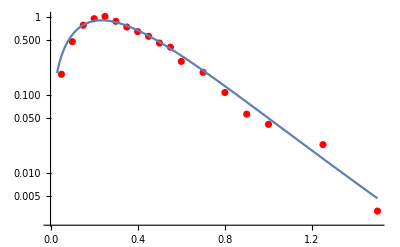

```mathematica
y163=Show[ListLogPlot[pt1,PlotStyle->Red],LogPlot[f[c,pt,1.042,T,µ,0.,0.13957018]/.{c->0.7337865232376415,T->0.1309383745297254,µ->0.6365665420622443},{pt,0.03,1.5}]]
```

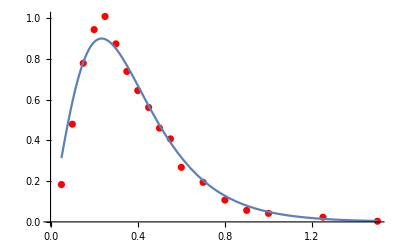

```mathematica
Show[ListPlot[pt1,PlotStyle->Red],Plot[f[c,pt,1.04,T,µ,0.,0.13957018]/.{c->0.4252184622325407,T->0.13325881043333251,µ->0.7080568979894174},{pt,0.05,1.5}]]
```

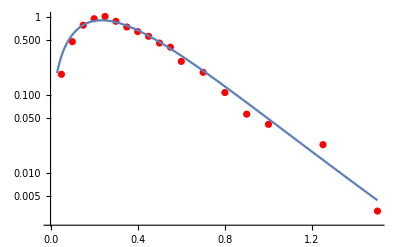

```mathematica
pt63=Show[ListLogPlot[pt1,PlotStyle->Red],LogPlot[f[c,pt,1.04,T,µ,0,0.13957018]/.{c->0.4252184622325407,T->0.13325881043333251,µ->0.7080568979894174},{pt,0.03,1.5}]]
```

```mathematica
pt1y2={{0.05,0.09927},{0.1,0.47149},{0.15,0.71274},{0.2,0.86242},{0.25,0.9637},{0.3,0.86979},{0.35,0.72327},{0.4,0.57446},{0.45,0.55643},{0.5,0.46663},{0.55,0.34765},{0.6,0.30308},{0.7,0.18683},{0.8,0.14013},{0.9,0.0769},{1,0.03567},{1.25,0.02002},{1.5,0.00403}}
```

{{0.05,0.09927},{0.1,0.47149},{0.15,0.71274},{0.2,0.86242},{0.25,0.9637},{0.3,0.86979},{0.35,0.72327},{0.4,0.57446},{0.45,0.55643},{0.5,0.46663},{0.55,0.34765},{0.6,0.30308},{0.7,0.18683},{0.8,0.14013},{0.9,0.0769},{1,0.03567},{1.25,0.02002},{1.5,0.00403}}

```mathematica
FindFit[pt1y2,f[c,pt,1.044
,T,µ,0.2,0.13957018],{c,T,µ},pt]
```

FindFit::nrlnum: The function value «1» is not a list of real numbers with dimensions {18} at {c,T,µ} = {0.478136,0.00452998,0.774179}.

{c→0.478136,T→0.00452998,µ→0.774179}

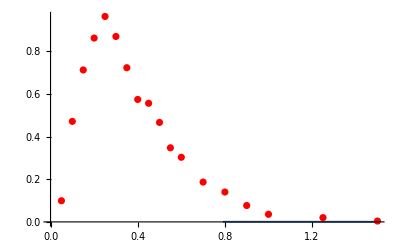

```mathematica
Show[ListPlot[pt1y2,PlotStyle->Red],Plot[f[c,pt,1.0435,T,µ,0.2,0.13957018]/.{c->0.4779444272782783,T->0.0043213216465509685,µ->0.7744873488895379},{pt,0.05,1.5}]]
```

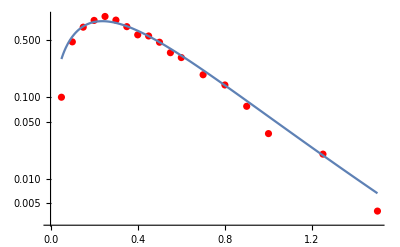

```mathematica
Show[ListLogPlot[pt1y2,PlotStyle->Red],LogPlot[f[c,pt,1.051,T,µ,0.25,0.13957018]/.{c->0.490311853750178,T->0.14313666140259337,µ->0.7114078374895708},{pt,0.05,1.5}]]
```

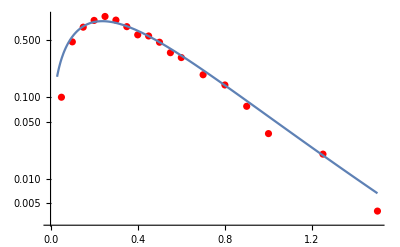

```mathematica
Show[ListLogPlot[pt1y2,PlotStyle->Red],LogPlot[f[c,pt,1.051,T,µ,0.25,0.13957018]/.{c->0.490311853750178,T->0.14313666140259337,µ->0.7114078374895708},{pt,0.03,1.5}]]
```

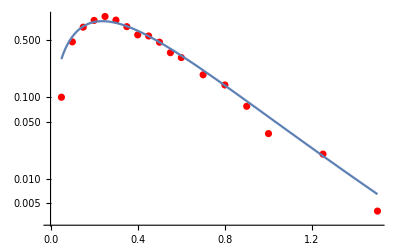

```mathematica
Show[ListLogPlot[pt1y2,PlotStyle->Red],LogPlot[f[c,pt,1.05,T,µ,0.25,0.13957018]/.{c->0.4955682280481965,T->0.14271353888212643,µ->0.7095582628732863},{pt,0.05,1.5}]]
```

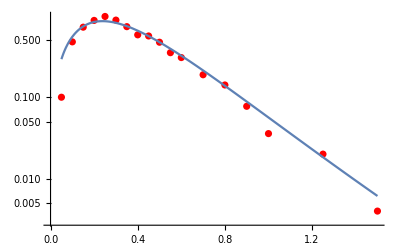

```mathematica
Show[ListLogPlot[pt1y2,PlotStyle->Red],LogPlot[f[c,pt,1.048,T,µ,0.25,0.13957018]/.{c->0.4574581062753354,T->0.14257195912554613,µ->0.7202989076931084},{pt,0.05,1.5}]]
```

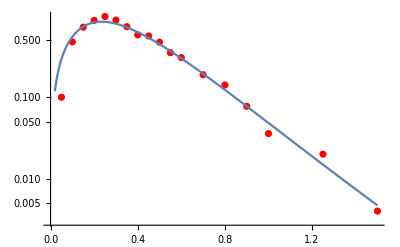

```mathematica
Show[ListLogPlot[pt1y2,PlotStyle->Red],LogPlot[f[c,pt,1.044,T,µ,0.2,0.13957018]/.{c->0.3857458,T->0.13782572,µ->0.7250299},{pt,0.02,1.5}]]
```

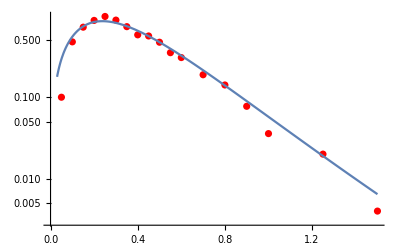

```mathematica
Show[ListLogPlot[pt1y2,PlotStyle->Red],LogPlot[f[c,pt,1.05,T,µ,0.25,0.13957018]/.{c->0.4955682280481965,T->0.14271353888212643,µ->0.7095582628732863},{pt,0.03,1.5}]]
```

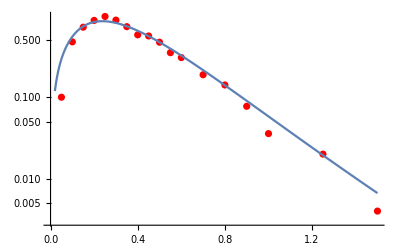

```mathematica
Show[ListLogPlot[pt1y2,PlotStyle->Red],LogPlot[f[c,pt,1.0512,T,µ,0.25,0.13957018]/.{c->0.6988729205788631,T->0.14063088426840142,µ->0.6611749420915872},{pt,0.02,1.5}]]
```

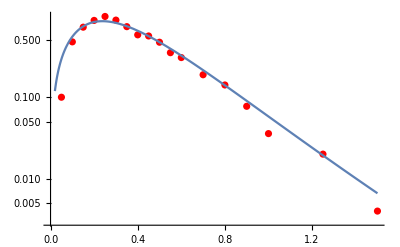

```mathematica
Show[ListLogPlot[pt1y2,PlotStyle->Red],LogPlot[f[c,pt,1.051,T,µ,0.25,0.13957018]/.{c->0.490311853750178,T->0.14313666140259337,µ->0.7114078374895708},{pt,0.02,1.5}]]
```

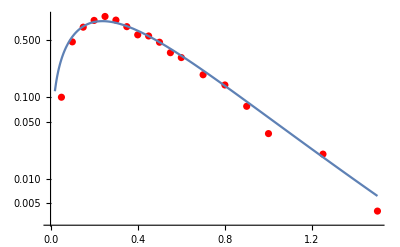

```mathematica
Show[ListLogPlot[pt1y2,PlotStyle->Red],LogPlot[f[c,pt,1.048,T,µ,0.25,0.13957018]/.{c->0.4574581062753354,T->0.14257195912554613,µ->0.7202989076931084},{pt,0.02,1.5}]]
```

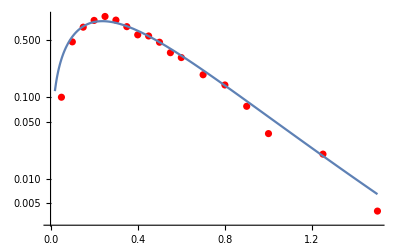

```mathematica
Show[ListLogPlot[pt1y2,PlotStyle->Red],LogPlot[f[c,pt,1.05,T,µ,0.25,0.13957018]/.{c->0.4955682280481965,T->0.14271353888212643,µ->0.7095582628732863},{pt,0.02,1.5}]]
```

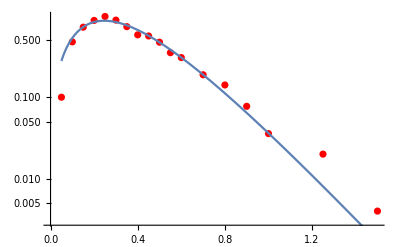

```mathematica
Show[ListLogPlot[pt1y2,PlotStyle->Red],LogPlot[f[c,pt,1.007,T,µ,0.3,0.13957018]/.{c->0.45990541144673314,T->0.1304116281760422,µ->0.7134305350680258},{pt,0.05,1.5}]]
```

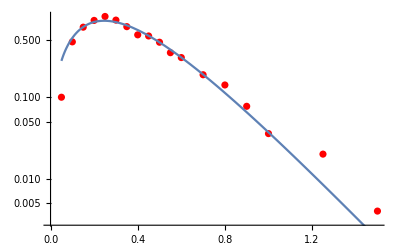

```mathematica
Show[ListLogPlot[pt1y2,PlotStyle->Red],LogPlot[f[c,pt,1.009,T,µ,0.3,0.13957018]/.{c->0.5179087465639438,T->0.13092024606339758,µ->0.698530462233025},{pt,0.05,1.5}]]
```

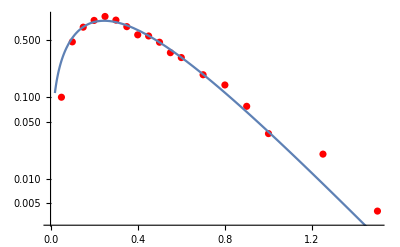

```mathematica
Show[ListLogPlot[pt1y2,PlotStyle->Red],LogPlot[f[c,pt,1.01,T,µ,0.3,0.13957018]/.{c->0.5177473702191621,T->0.1312302407334524,µ->0.6988637071344641},{pt,0.02,1.5}]]
```

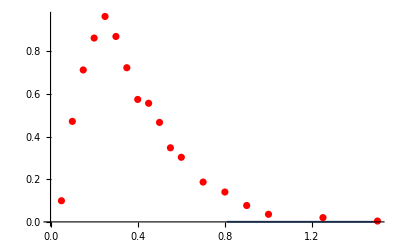

```mathematica
Show[ListPlot[pt1y2,PlotStyle->Red],Plot[f[c,pt,1.041,T,µ,0.2,0.13957018]/.{c->0.47698032686079267,T->0.003282230388092666,µ->0.7760373032976773},{pt,0.05,1.5}]]
```

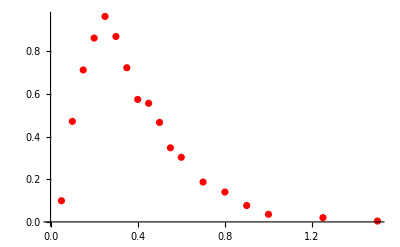

```mathematica
Show[ListPlot[pt1y2,PlotStyle->Red],Plot[f[pt,1.01,T,µ,0.2]/.{T->0.1266218333786964,µ->0.583128656762679},{pt,0.05,1.5}]]
```

```mathematica
pt1y3={{0.05,0.1066
},{0.1,0.53873
},{0.15,0.74674
},{0.2,0.89348
},{0.25,0.81617
},{0.3,0.78523
},{0.35,0.63538
},{0.4,0.6026
},{0.45,0.4986
},{0.5,0.3956
},{0.55,0.30077
},{0.6,0.24695
},{0.7,0.20177
},{0.8,0.1176
},{0.9,0.06453
},{1,0.03423
},{1.25,0.01611},{1.5,0.00284}}
```

{{0.05,0.1066},{0.1,0.53873},{0.15,0.74674},{0.2,0.89348},{0.25,0.81617},{0.3,0.78523},{0.35,0.63538},{0.4,0.6026},{0.45,0.4986},{0.5,0.3956},{0.55,0.30077},{0.6,0.24695},{0.7,0.20177},{0.8,0.1176},{0.9,0.06453},{1,0.03423},{1.25,0.01611},{1.5,0.00284}}

```mathematica
FindFit[pt1y3,f[c,pt,1.032,T,µ,0.5,0.13957018],{c,T,µ},pt]
```

{c→0.703167,T→0.139938,µ→0.680535}

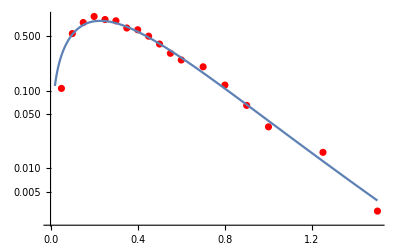

```mathematica
y363=Show[ListLogPlot[pt1y3,PlotStyle->Red],LogPlot[f[c,pt,1.045,T,µ,0.4,0.13957018]/.{c->0.48003167,T->0.140938,µ->0.710535},{pt,0.02,1.5}]]
```

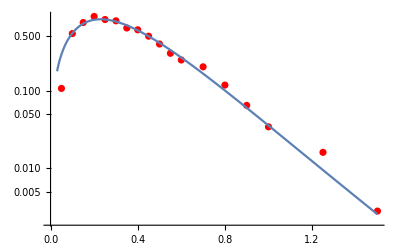

```mathematica
Show[ListLogPlot[pt1y3,PlotStyle->Red],LogPlot[f[c,pt,1.032,T,µ,0.4,0.13957018]/.{c->0.4432665602156018,T->0.1363404115930695,µ->0.7205475488409523},{pt,0.03,1.5}]]
```

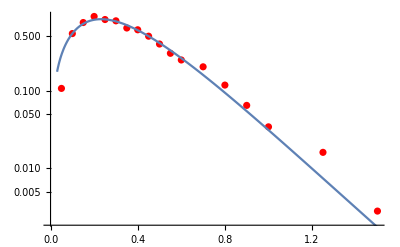

```mathematica
Show[ListLogPlot[pt1y3,PlotStyle->Red],LogPlot[f[c,pt,1.021,T,µ,0.4,0.13957018]/.{c->0.55034877516697,T->0.1320566607373824,µ->0.6882198879306008},{pt,0.03,1.5}]]
```

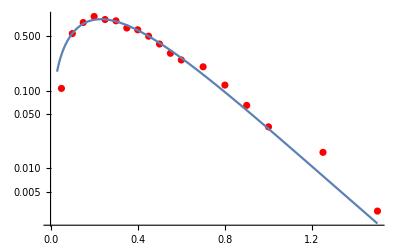

```mathematica
Show[ListLogPlot[pt1y3,PlotStyle->Red],LogPlot[f[c,pt,1.024,T,µ,0.4,0.13957018]/.{c->0.5486748950700997,T->0.13296983268458876,µ->0.6894194451032593},{pt,0.03,1.5}]]
```

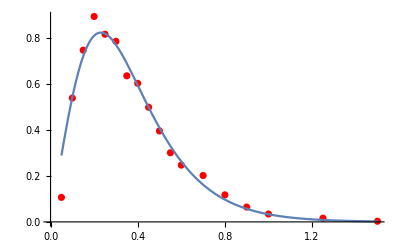

```mathematica
Show[ListPlot[pt1y3,PlotStyle->Red],Plot[f[c,pt,1.026,T,µ,0.4,0.13957018]/.{c->0.5475081855108451,T->0.13358381411414608,µ->0.6902370102273754},{pt,0.05,1.5}]]
```

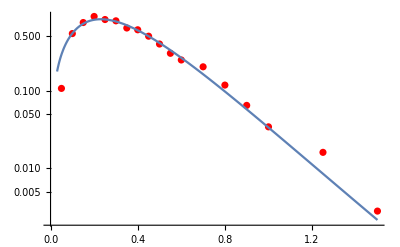

```mathematica
Show[ListLogPlot[pt1y3,PlotStyle->Red],LogPlot[f[c,pt,1.027,T,µ,0.4,0.13957018]/.{c->0.46514001026272167,T->0.13447912932728884,µ->0.7123819242818256},{pt,0.03,1.5}]]
```

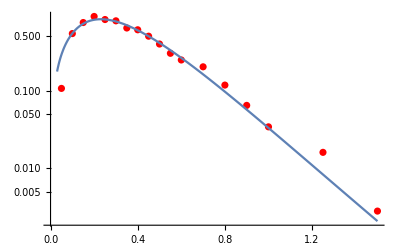

```mathematica
Show[ListLogPlot[pt1y3,PlotStyle->Red],LogPlot[f[c,pt,1.026,T,µ,0.4,0.13957018]/.{c->0.5475081855108451,T->0.13358381411414608,µ->0.6902370102273754},{pt,0.03,1.5}]]
```

```mathematica
pt1y2g=Show[ListLogPlot[pt1y3,PlotStyle->Red],LogPlot[f[c,pt,1.032,T,µ,0.4,0.13957018]/.{c->0.4432665602156018,T->0.1363404115930695,µ->0.7205475488409523},{pt,0.03,1.5}]]
```

-Graphics-

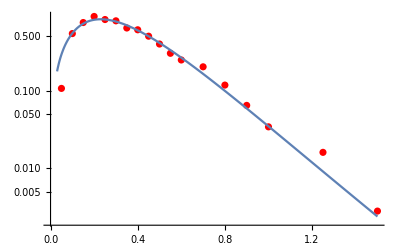

```mathematica
Show[ListLogPlot[pt1y3,PlotStyle->Red],LogPlot[f[c,pt,1.03,T,µ,0.4,0.13957018]/.{c->0.4476174345442409,T->0.13562363659893328,µ->0.7185475514430489},{pt,0.03,1.5}]]
```

```mathematica
pt1y4={{0.05,0.11354

},{0.1,0.42719
},{0.15,0.68126
},{0.2,0.77628
},{0.25,0.75983
},{0.3,0.69352
},{0.35,0.64963
},{0.4,0.50699
},{0.45,0.41596
},{0.5,0.3549
},{0.55,0.32978
},{0.6,0.24298
},{0.7,0.15673
},{0.8,0.09064

},{0.9,0.05337
},{1,0.02911
},{1.25,0.01597},{1.5,0.00232}}
```

{{0.05,0.11354},{0.1,0.42719},{0.15,0.68126},{0.2,0.77628},{0.25,0.75983},{0.3,0.69352},{0.35,0.64963},{0.4,0.50699},{0.45,0.41596},{0.5,0.3549},{0.55,0.32978},{0.6,0.24298},{0.7,0.15673},{0.8,0.09064},{0.9,0.05337},{1,0.02911},{1.25,0.01597},{1.5,0.00232}}

```mathematica
FindFit[pt1y4,f[c,pt,1.038,T,µ,0.6,0.13957018],{c,T,µ},pt]
```

{c→0.261911,T→0.155766,µ→0.848985}

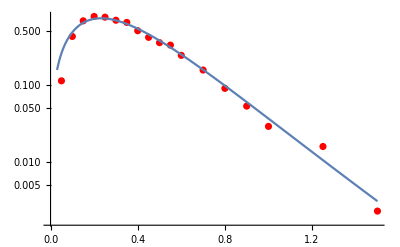

```mathematica
Show[ListLogPlot[pt1y4,PlotStyle->Red],LogPlot[f[c,pt,1.038,T,µ,0.6,0.13957018]/.{c->0.26191101762855235,T->0.15576555616424106,µ->0.8489853327213144},{pt,0.03,1.5}]]
```

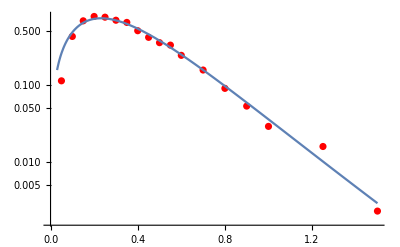

```mathematica
Show[ListLogPlot[pt1y4,PlotStyle->Red],LogPlot[f[c,pt,1.036,T,µ,0.6,0.13957018]/.{c->0.4831680591055609,T->0.15151968209623307,µ->0.7541640963804763},{pt,0.03,1.5}]]
```

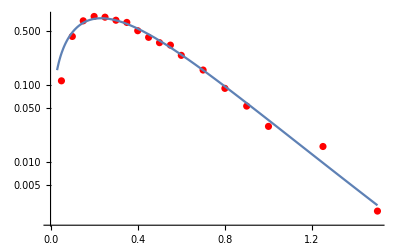

```mathematica
Show[ListLogPlot[pt1y4,PlotStyle->Red],LogPlot[f[c,pt,1.034,T,µ,0.6,0.13957018]/.{c->0.9370234070651723,T->0.14750013260927003,µ->0.6548233249482622},{pt,0.03,1.5}]]
```

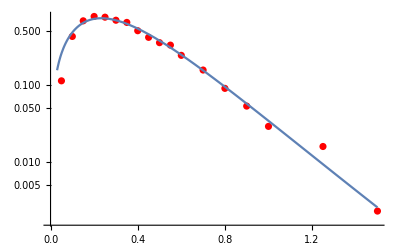

```mathematica
Show[ListLogPlot[pt1y4,PlotStyle->Red],LogPlot[f[c,pt,1.032,T,µ,0.6,0.13957018]/.{c->0.9384350213401139,T->0.1470450336429297,µ->0.6544321587480396},{pt,0.03,1.5}]]
```

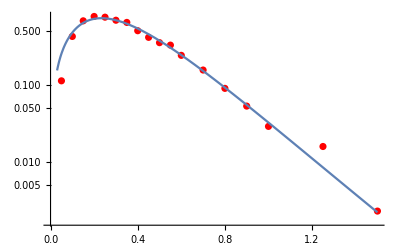

```mathematica
Show[ListLogPlot[pt1y4,PlotStyle->Red],LogPlot[f[c,pt,1.0275,T,µ,0.6,0.13957018]/.{c->0.4991155804539164,T->0.14860091337192313,µ->0.7470644469105285},{pt,0.03,1.5}]]
```

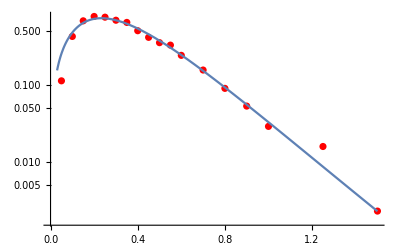

```mathematica
Show[ListLogPlot[pt1y4,PlotStyle->Red],LogPlot[f[c,pt,1.0285,T,µ,0.6,0.13957018]/.{c->0.4310694698280098,T->0.1495442370018848,µ->0.7691928197827876},{pt,0.03,1.5}]]
```

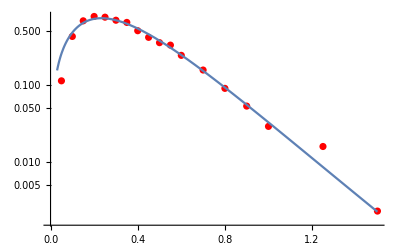

```mathematica
Show[ListLogPlot[pt1y4,PlotStyle->Red],LogPlot[f[c,pt,1.028,T,µ,0.6,0.13957018]/.{c->0.9465972139897513,T->0.14611860472819968,µ->0.6528280322913812},{pt,0.03,1.5}]]
```

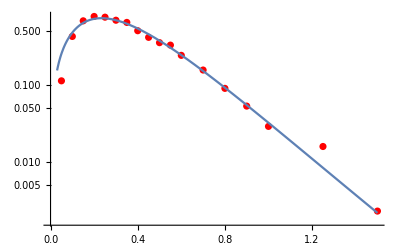

```mathematica
Show[ListLogPlot[pt1y4,PlotStyle->Red],LogPlot[f[c,pt,1.027,T,µ,0.6,0.13957018]/.{c->0.7980284397461097,T->0.1465721247571489,µ->0.6777118305095957},{pt,0.03,1.5}]]
```

```mathematica
pt1y5={{0.05,0.12887

},{0.1,0.40839
},{0.15,0.58562
},{0.2,0.60641
},{0.25,0.67261
},{0.3,0.61973
},{0.35,0.52341
},{0.4,0.44729
},{0.45,0.31733
},{0.5,0.28752
},{0.55,0.27691
},{0.6,0.22262
},{0.7,0.12563
},{0.8,0.06927
},{0.9,0.0444
},{1,0.01113
},{1.25,0.00771},{1.5,0.00147}}
```

{{0.05,0.12887},{0.1,0.40839},{0.15,0.58562},{0.2,0.60641},{0.25,0.67261},{0.3,0.61973},{0.35,0.52341},{0.4,0.44729},{0.45,0.31733},{0.5,0.28752},{0.55,0.27691},{0.6,0.22262},{0.7,0.12563},{0.8,0.06927},{0.9,0.0444},{1,0.01113},{1.25,0.00771},{1.5,0.00147}}

```mathematica
FindFit[pt1y5,f[c,pt,1.022,T,µ,0.8,0.13957018],{c,T,µ},pt]
```

{c→0.809342,T→0.159871,µ→0.710334}

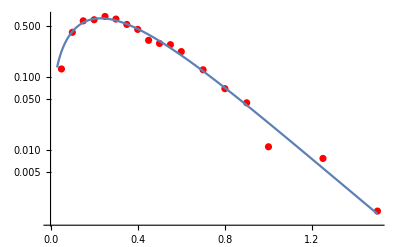

```mathematica
Show[ListLogPlot[pt1y5,PlotStyle->Red],LogPlot[f[c,pt,1.022,T,µ,0.8,0.13957018]/.{c->0.8093415847966909,T->0.1598706928141805,µ->0.7103338830766496},{pt,0.03,1.5}]]
```

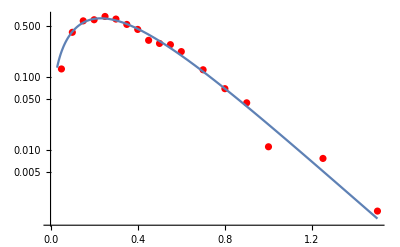

```mathematica
Show[ListLogPlot[pt1y5,PlotStyle->Red],LogPlot[f[c,pt,1.018,T,µ,0.8,0.13957018]/.{c->0.5568387607684782,T->0.16005238295798618,µ->0.7697246677199624},{pt,0.03,1.5}]]
```

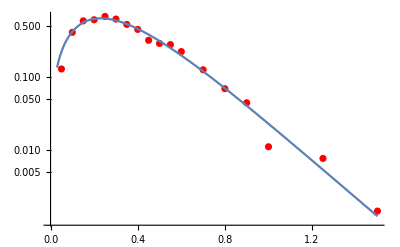

```mathematica
pt1y3g=Show[ListLogPlot[pt1y5,PlotStyle->Red],LogPlot[f[c,pt,1.02,T,µ,0.8,0.13957018]/.{c->0.8720301507548233,T->0.15918636817272566,µ->0.6983198443191151},{pt,0.03,1.5}]]
```

```mathematica
pt1y6={{0.05,0.05524

},{0.1,0.38215
},{0.15,0.53454
},{0.2,0.54919
},{0.25,0.56308
},{0.3,0.50709
},{0.35,0.43851
},{0.4,0.33312
},{0.45,0.28956
},{0.5,0.25645
},{0.55,0.17144
},{0.6,0.11678
},{0.7,0.0959
},{0.8,0.06222
},{0.9,0.02364
},{1,0.00701
},{1.25,0.00482},{1.5,0.00036}}
```

{{0.05,0.05524},{0.1,0.38215},{0.15,0.53454},{0.2,0.54919},{0.25,0.56308},{0.3,0.50709},{0.35,0.43851},{0.4,0.33312},{0.45,0.28956},{0.5,0.25645},{0.55,0.17144},{0.6,0.11678},{0.7,0.0959},{0.8,0.06222},{0.9,0.02364},{1,0.00701},{1.25,0.00482},{1.5,0.00036}}

```mathematica
FindFit[pt1y6,f[c,pt,1.0175,T,µ,1.0,0.13957018],{c,T,µ},pt]
```

{c→0.571762,T→0.173939,µ→0.808005}

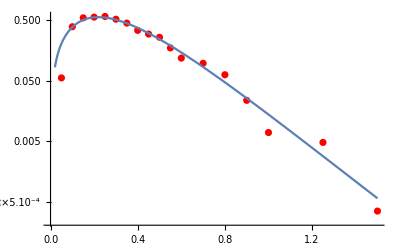

```mathematica
Show[ListLogPlot[pt1y6,PlotStyle->Red],LogPlot[f[c,pt,1.017,T,µ,1.,0.13957018]/.{c->0.5928981235124485,T->0.1736978634611121,µ->0.8016457187111155},{pt,0.02,1.5}]]
```

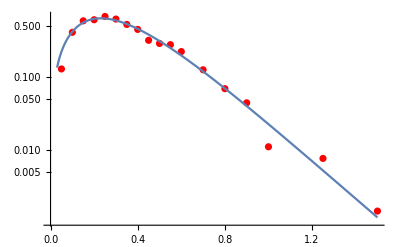

```mathematica
Show[ListLogPlot[pt1y5,PlotStyle->Red],LogPlot[f[c,pt,1.019,T,µ,1.,0.13957018]/.{c->0.5840534506202825,T->0.18432066905598551,µ->0.8530407309275276},{pt,0.03,1.5}]]
```

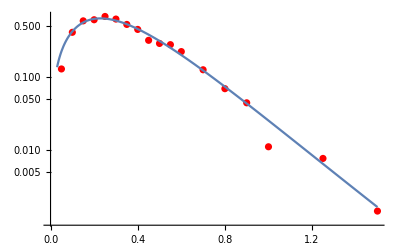

```mathematica
Show[ListLogPlot[pt1y5,PlotStyle->Red],LogPlot[f[c,pt,1.028,T,µ,1.,0.13957018]/.{c->0.5775746665408604,T->0.1870222662151892,µ->0.8562518473911066},{pt,0.03,1.5}]]
```

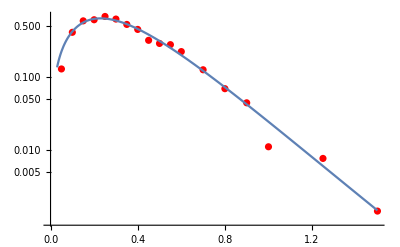

```mathematica
Show[ListLogPlot[pt1y5,PlotStyle->Red],LogPlot[f[c,pt,1.025,T,µ,1.,0.13957018]/.{c->0.9214209155946295,T->0.18396969177713265,µ->0.769434837140113},{pt,0.03,1.5}]]
```

```mathematica
Show[ListLogPlot[pt1y5,PlotStyle->Red],LogPlot[f[c,pt,1.022,T,µ,1.,0.13957018]/.{c->0.5824613986394895,T->0.18520865751445809,µ->0.8539213927387076},{pt,0.03,1.5}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt1y5,PlotStyle->Red],LogPlot[f[c,pt,1.02,T,µ,1.,0.13957018]/.{c->0.9255082683506042,T->0.1829205647154335,µ->0.7685693514075512},{pt,0.03,1.5}]]
```

-Graphics-

```mathematica
pt1y7={{0.05,0.13808

},{0.1,0.25155
},{0.15,0.43746
},{0.2,0.52065
},{0.25,0.48944
},{0.3,0.39177
},{0.35,0.28326
},{0.4,0.26572
},{0.45,0.20684
},{0.5,0.14086
},{0.55,0.13302
},{0.6,0.10065
},{0.7,0.06606
},{0.8,0.03526},{0.9,0.0112
},{1,0.00465
},{1.25,0.00063}}
```

{{0.05,0.13808},{0.1,0.25155},{0.15,0.43746},{0.2,0.52065},{0.25,0.48944},{0.3,0.39177},{0.35,0.28326},{0.4,0.26572},{0.45,0.20684},{0.5,0.14086},{0.55,0.13302},{0.6,0.10065},{0.7,0.06606},{0.8,0.03526},{0.9,0.0112},{1,0.00465},{1.25,0.00063}}

```mathematica
FindFit[pt1y7,f[c,pt,1.0101,T,µ,1.2,0.13957018],{c,T,µ},pt]
```

{c→0.556716,T→0.187388,µ→0.854542}

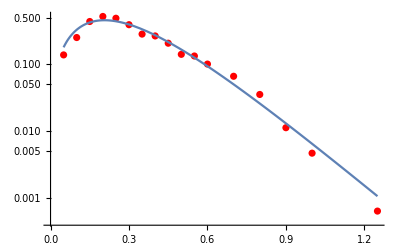

```mathematica
Show[ListLogPlot[pt1y7,PlotStyle->Red],LogPlot[f[c,pt,1.0101,T,µ,1.2,0.13957018]/.{c->0.5567164829552771,T->0.18738842121705787,µ->0.8545417061730067},{pt,0.05,1.25}]]
```

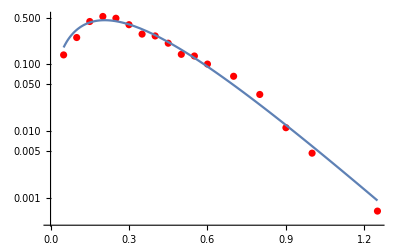

```mathematica
Show[ListLogPlot[pt1y7,PlotStyle->Red],LogPlot[f[c,pt,1.006,T,µ,1.2,0.13957018]/.{c->0.8928935940632803,T->0.18582675820020605,µ->0.7663779231361484},{pt,0.05,1.25}]]
```

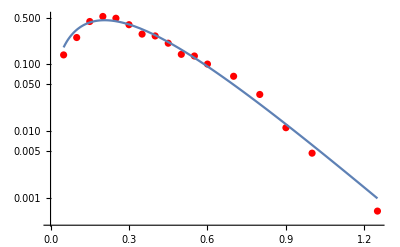

```mathematica
Show[ListLogPlot[pt1y7,PlotStyle->Red],LogPlot[f[c,pt,1.008,T,µ,1.2,0.13957018]/.{c->0.5635950667791989,T->0.18683970694638885,µ->0.852118160583512},{pt,0.05,1.25}]]
```

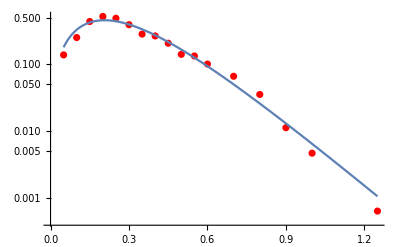

```mathematica
pt1y4g=Show[ListLogPlot[pt1y7,PlotStyle->Red],LogPlot[f[c,pt,1.01,T,µ,1.2,0.13957018]/.{c->0.5656894752002206,T->0.1873331797352,µ->0.8515400300672642},{pt,0.05,1.25}]]
```

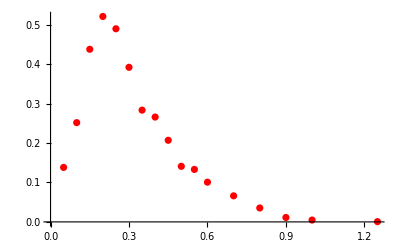

```mathematica
Show[ListPlot[pt1y7,PlotStyle->Red],Plot[f[pt,1.01,T,m,1.2,0.13957018]/.{T->0.18626895987030376,m->0.7451178861126251},{pt,0.05,1.25}]]
```

```mathematica
pt1y8={{0.05,0.08333

},{0.1,0.23574
},{0.15,0.34636
},{0.2,0.38181
},{0.25,0.38623
},{0.3,0.2834
},{0.35,0.22342
},{0.4,0.15521
},{0.45,0.12296
},{0.5,0.09594
},{0.55,0.0744
},{0.6,0.0319
},{0.7,0.02543
},{0.8,0.01674

},{0.9,0.00853
},{1,0.00201}}
```

{{0.05,0.08333},{0.1,0.23574},{0.15,0.34636},{0.2,0.38181},{0.25,0.38623},{0.3,0.2834},{0.35,0.22342},{0.4,0.15521},{0.45,0.12296},{0.5,0.09594},{0.55,0.0744},{0.6,0.0319},{0.7,0.02543},{0.8,0.01674},{0.9,0.00853},{1,0.00201}}

```mathematica
FindFit[pt1y8,f[c,pt,1.001,T,µ,1.4,0.13957018],{c,T,µ},pt]
```

{c→119.276,T→0.201684,µ→-0.195424}

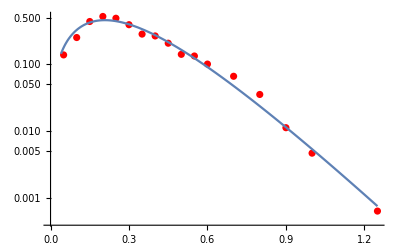

```mathematica
Show[ListLogPlot[pt1y7,PlotStyle->Red],LogPlot[f[c,pt,1.001,T,µ,1.4,0.13957018]/.{c->0.5924867625870202,T->0.21983090170623132,µ->0.9629002909764389},{pt,0.04,1.25}]]
```

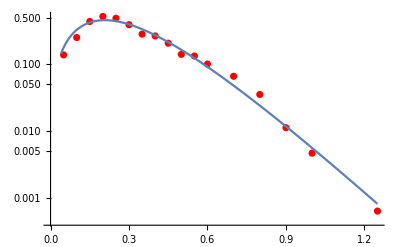

```mathematica
Show[ListLogPlot[pt1y7,PlotStyle->Red],LogPlot[f[c,pt,1.003,T,µ,1.4,0.13957018]/.{c->0.9578048595841337,T->0.22000502162074337,µ->0.8571734425670752},{pt,0.04,1.25}]]
```

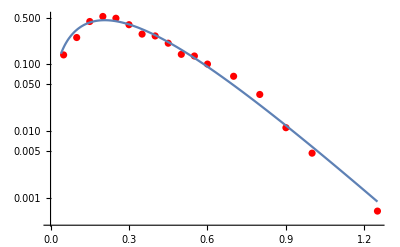

```mathematica
Show[ListLogPlot[pt1y7,PlotStyle->Red],LogPlot[f[c,pt,1.005,T,µ,1.4,0.13957018]/.{c->0.8941081801902749,T->0.2203607297731738,µ->0.8721702195106863},{pt,0.04,1.25}]]
```

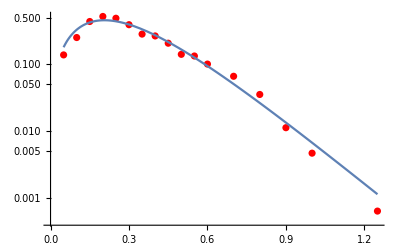

```mathematica
Show[ListLogPlot[pt1y7,PlotStyle->Red],LogPlot[f[c,pt,1.012,T,µ,1.4,0.13957018]/.{c->0.8858421423426818,T->0.22147368649022303,µ->0.8737101216892924},{pt,0.05,1.25}]]
```

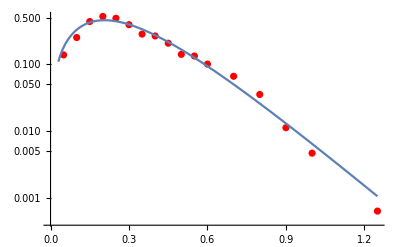

```mathematica
Show[ListLogPlot[pt1y7,PlotStyle->Red],LogPlot[f[c,pt,1.01,T,µ,1.4,0.13957018]/.{c->0.9352909893462437,T->0.22103815300287763,µ->0.8618466833993983},{pt,0.03,1.25}]]
```

```mathematica
pt1y9={{0.05,0.08704},{0.1,0.1871
},{0.15,0.29605
},{0.2,0.3019
},{0.25,0.29439
},{0.3,0.23287
},{0.35,0.17683
},{0.4,0.12207
},{0.45,0.06683
},{0.5,0.06188
},{0.55,0.04259
},{0.6,0.03621
},{0.7,0.01093
},{0.8,0.00474}}
```

{{0.05,0.08704},{0.1,0.1871},{0.15,0.29605},{0.2,0.3019},{0.25,0.29439},{0.3,0.23287},{0.35,0.17683},{0.4,0.12207},{0.45,0.06683},{0.5,0.06188},{0.55,0.04259},{0.6,0.03621},{0.7,0.01093},{0.8,0.00474}}

```mathematica
FindFit[pt1y9,f[c,pt,1.01,T,µ,1.6,0.13957018],{c,T,µ},pt]
```

{c→1.41042,T→0.231608,µ→0.738865}

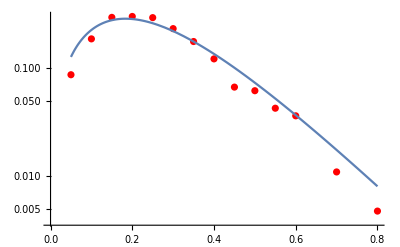

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.01,T,µ,1.6,0.13957018]/.{c->1.4104178238865304,T->0.23160768183681885,µ->0.7388647669505813},{pt,0.05,0.8}]]
```

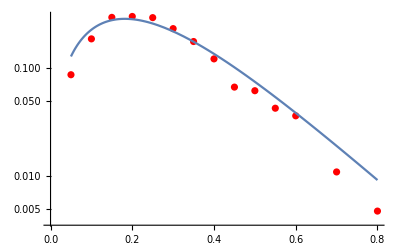

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.02,T,µ,1.6,0.13957018]/.{c->0.35927782864527746,T->0.23742105753536163,µ->1.0577052459128284},{pt,0.05,0.8}]]
```

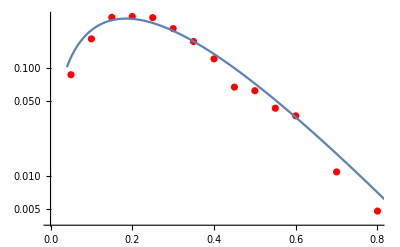

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.0008,T,µ,1.6,0.13957018]/.{c->0.846374347128557,T->0.23224853432440995,µ->0.8587462415603291},{pt,0.04,0.9}]]
```

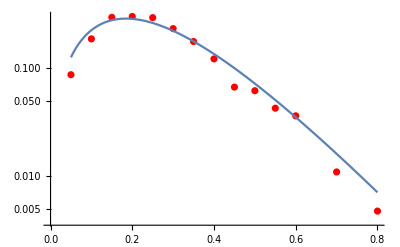

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.001,T,µ,1.6,0.13957018]/.{c->2.288683054170139,T->0.23202944028485484,µ->0.6277874258191372},{pt,0.05,0.8}]]
```

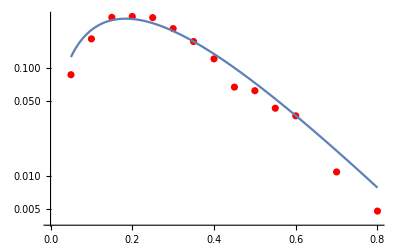

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.008,T,µ,1.6,0.13957018]/.{c->1.8382245806576536,T->0.2312357119676991,µ->0.6778272197104905},{pt,0.05,0.8}]]
```

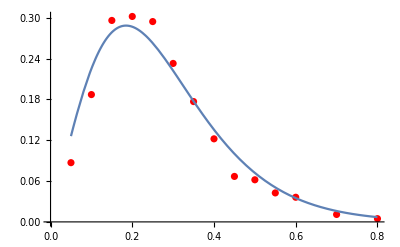

```mathematica
Show[ListPlot[pt1y9,PlotStyle->Red],Plot[f[c,pt,1.0003,T,µ,1.6,0.13957018]/.{c->0.8294303182039686,T->0.23222035327647153,µ->0.863512349259919},{pt,0.05,0.8}]]
```

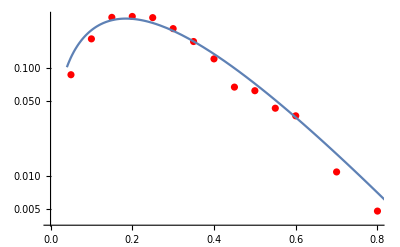

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.00045,T,µ,1.6,0.13957018]/.{c->2.4226159971459684,T->0.232117946238719,µ->0.6146326278694018},{pt,0.04,0.9}]]
```

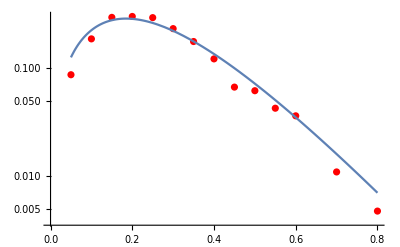

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.0004,T,µ,1.6,0.13957018]/.{c->0.7702389746453002,T->0.23223361805733653,µ->0.8806923990272455},{pt,0.05,0.8}]]
```

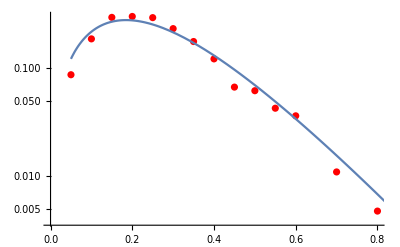

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.00045,T,µ,1.6,0.13957018]/.{c->1.003612,T->0.2322085142161991,µ->0.811801},{pt,0.05,0.9}]]
```

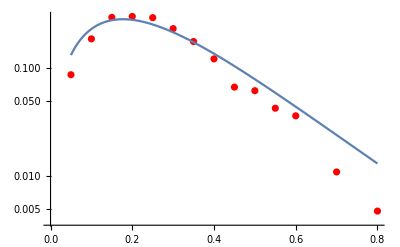

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.05,T,µ,1.6,0.13957018]/.{c->0.8256205136905138,T->0.23546814761937654,µ->0.8573241865559834},{pt,0.05,0.8}]]
```

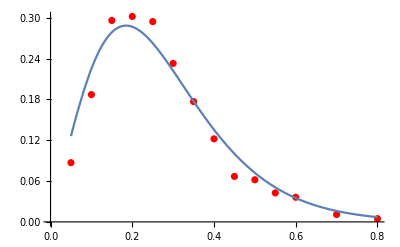

```mathematica
Show[ListPlot[pt1y9,PlotStyle->Red],Plot[f[c,pt,1.0007,T,µ,1.6,0.13957018]/.{c->166.24581018630872,T->0.2313857889065666,µ->-0.3652778493361626},{pt,0.05,0.8}]]
```

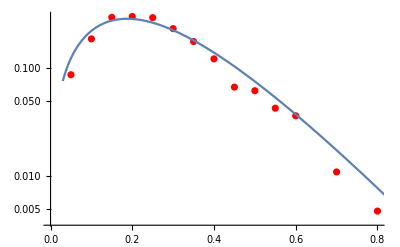

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.0007,T,µ,1.6,0.13957018]/.{c->135.246,T->0.23505386,µ->-0.33278},{pt,0.03,0.9}]]
```

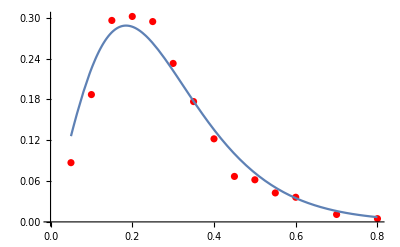

```mathematica
Show[ListPlot[pt1y9,PlotStyle->Red],Plot[f[c,pt,1.00009,T,µ,1.6,0.13957018]/.{c->126.68671723679425,T->0.23210186995582568,µ->-0.30390112523003937},{pt,0.05,0.8}]]
```

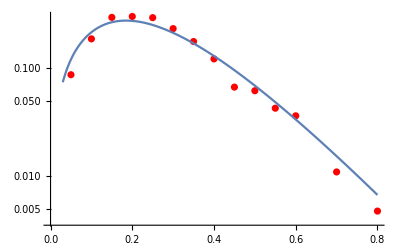

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.0002,T,µ,1.6,0.13957018]/.{c->1.87946,T->0.23217597699828968,µ->0.66359},{pt,0.03,0.8}]]
```

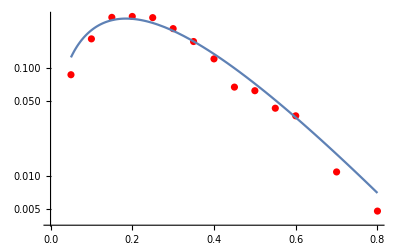

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.0001,T,µ,1.6,0.13957018]/.{c->123.78994551844642,T->0.23209137124091644,µ->-0.2985078396006619},{pt,0.05,0.8}]]
```

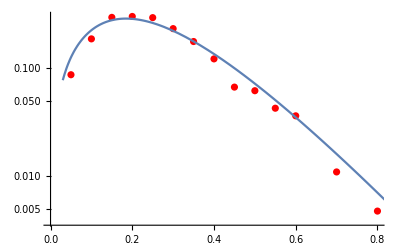

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.0005,T,µ,1.6,0.13957018]/.{c->114.20287703229175,T->0.23166195922133853,µ->-0.27885477316857865},{pt,0.03,0.9}]]
```

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.001,T,µ,1.6,0.13957018]/.{c->2.288683054170139,T->0.23202944028485484,µ->0.6277874258191372},{pt,0.05,0.8}]]
```

-Graphics-

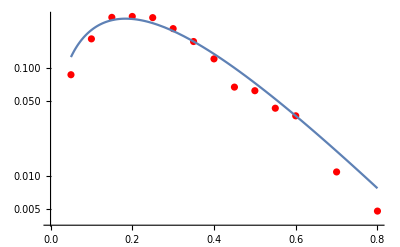

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.007,T,µ,1.6,0.13957018]/.{c->0.7639370537329024,T->0.23278259837661341,µ->0.881718012951544},{pt,0.05,0.8}]]
```

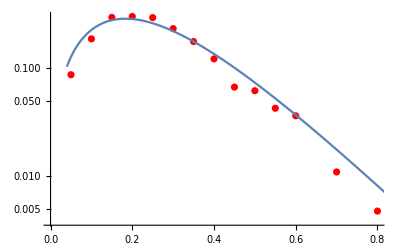

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.0109,T,µ,1.6,0.13957018]/.{c->1.8561268218676272,T->0.23086226940417215,µ->0.6752449702293657},{pt,0.04,0.9}]]
```

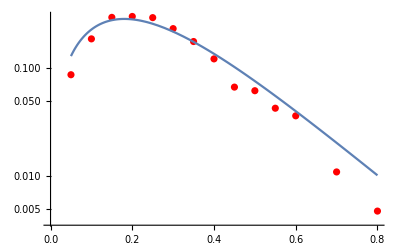

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.028,T,µ,1.6,0.13957018]/.{c->0.9288992917260418,T->0.23325427633587126,µ->0.8330932032942464},{pt,0.05,0.8}]]
```

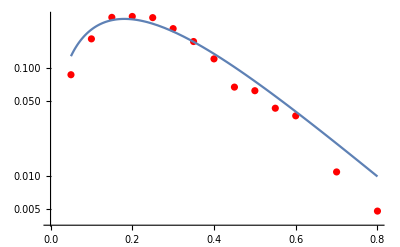

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.026,T,µ,1.6,0.13957018]/.{c->0.7467061147481949,T->0.23450636273684058,µ->0.8844528654564974},{pt,0.05,0.8}]]
```

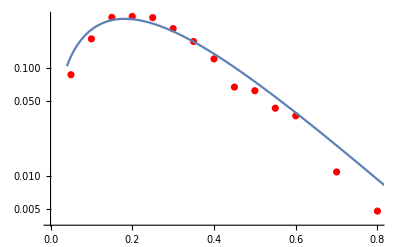

```mathematica
pt1y5g=Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.021,T,µ,1.6,0.13957018]/.{c->0.720859761360862,T->0.23423462641350967,µ->0.8933898249970841},{pt,0.04,0.9}]]
```

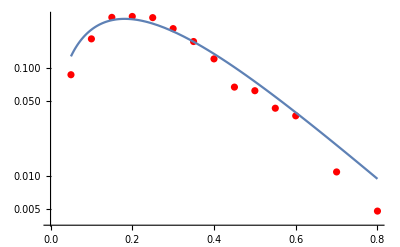

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.022,T,µ,1.6,0.13957018]/.{c->2.3978553764492463,T->0.2282169903041361,µ->0.6153068241324863},{pt,0.05,0.8}]]
```

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.02,T,µ,1.6,0.13957018]/.{c->0.35927782864527746,T->0.23742105753536163,µ->1.0577052459128284},{pt,0.05,0.8}]]
```

-Graphics-

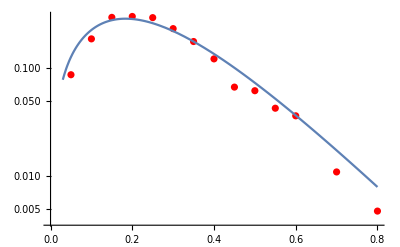

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.009,T,µ,1.6,0.13957018]/.{c->1.4190201486734957,T->0.23165430344314902,µ->0.7375988006653855},{pt,0.03,0.8}]]
```

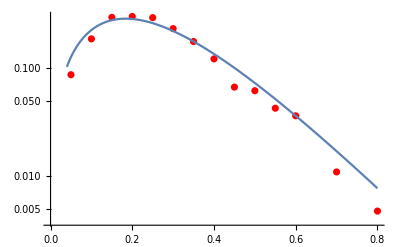

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.007,T,µ,1.6,0.13957018]/.{c->0.7639370537329024,T->0.23278259837661341,µ->0.881718012951544},{pt,0.04,0.8}]]
```

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.01,T,µ,1.6,0.13957018]/.{c->1.4104178238865304,T->0.23160768183681885,µ->0.7388647669505813},{pt,0.05,0.8}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.02,T,µ,1.6,0.13957018]/.{c->0.35927782864527746,T->0.23742105753536163,µ->1.0577052459128284},{pt,0.05,0.8}]]
```

-Graphics-

```mathematica
pt1y10={{0.05,0.06032
},{0.1,0.17112
},{0.15,0.24247
},{0.2,0.2545
},{0.25,0.17378
},{0.3,0.13229
},{0.35,0.09132
},{0.4,0.06788
},{0.45,0.04343
},{0.5,0.03366
},{0.55,0.02125
},{0.7,0.00409}}
```

{{0.05,0.06032},{0.1,0.17112},{0.15,0.24247},{0.2,0.2545},{0.25,0.17378},{0.3,0.13229},{0.35,0.09132},{0.4,0.06788},{0.45,0.04343},{0.5,0.03366},{0.55,0.02125},{0.7,0.00409}}

```mathematica
{{0.05,0.06032},{0.1,0.17112},{0.15,0.24247},{0.2,0.2545},{0.25,0.17378},{0.3,0.13229},{0.35,0.09132},{0.4,0.06788},{0.45,0.04343},{0.5,0.03366},{0.55,0.02125},{0.7,0.00409}}
```

{{0.05,0.06032},{0.1,0.17112},{0.15,0.24247},{0.2,0.2545},{0.25,0.17378},{0.3,0.13229},{0.35,0.09132},{0.4,0.06788},{0.45,0.04343},{0.5,0.03366},{0.55,0.02125},{0.7,0.00409}}

```mathematica
FindFit[pt1y10,f[c,pt,1.00041,T,µ,1.8,0.13957018],{c,T,µ},pt]
```

{c→0.992412,T→0.243304,µ→0.841972}

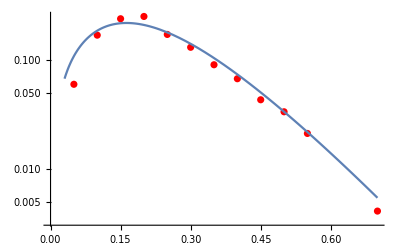

```mathematica
Show[ListLogPlot[pt1y10,PlotStyle->Red],LogPlot[f[c,pt,1.00041,T,µ,1.8,0.13957018]/.{c->0.9924117436863275,T->0.24330390612792946,µ->0.8419717575139625},{pt,0.03,0.7}]]
```

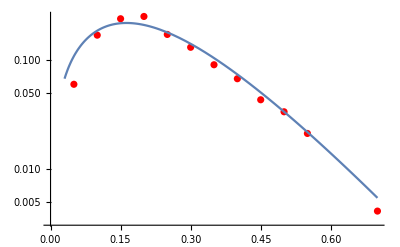

```mathematica
Show[ListLogPlot[pt1y10,PlotStyle->Red],LogPlot[f[c,pt,1.0003,T,µ,1.8,0.13957018]/.{c->0.5298567936114338,T->0.24335292245530118,µ->0.9946847261835813},{pt,0.03,0.7}]]
```

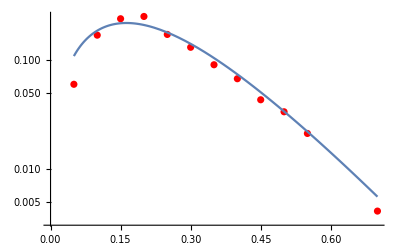

```mathematica
Show[ListLogPlot[pt1y10,PlotStyle->Red],LogPlot[f[c,pt,1.002,T,µ,1.8,0.13957018]/.{c->106.37196472149037,T->0.24099385207623947,µ->-0.2900790892716737},{pt,0.05,0.7}]]
```

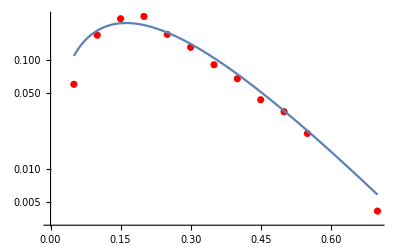

```mathematica
Show[ListLogPlot[pt1y10,PlotStyle->Red],LogPlot[f[c,pt,1.005,T,µ,1.8,0.13957018]/.{c->0.9973861068284462,T->0.24316396549928973,µ->0.8400950037965784},{pt,0.05,0.7}]]
```

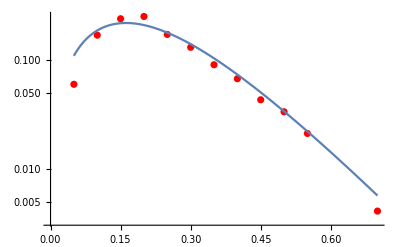

```mathematica
Show[ListLogPlot[pt1y10,PlotStyle->Red],LogPlot[f[c,pt,1.005,T,µ,1.8,0.13957018]/.{c->0.9267505908727566,T->0.24247710352817398,µ->0.8575097725969654},{pt,0.05,0.7}]]
```

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.007,T,µ,1.8,0.13957018]/.{c->0.353529421201218,T->0.2817987963735472,µ->1.2271257265497806},{pt,0.05,0.8}]]
```

-Graphics-

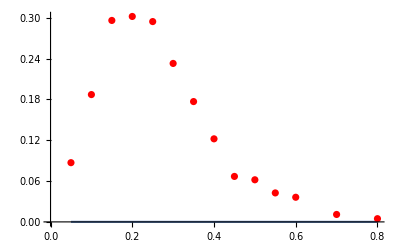

```mathematica
Show[ListPlot[pt1y9,PlotStyle->Red],Plot[f[c,pt,1.0006,T,µ,1.8,0.13957018]/.{c->117.38758077411899,T->0.2738447790621862,µ->-115.65839210719511},{pt,0.05,0.8}]]
```

```mathematica
Show[ListPlot[pt1y9,PlotStyle->Red],Plot[f[c,pt,1.0007,T,µ,1.8,0.13957018]/.{c->1.1540624771060601,T->0.27990168335506177,µ->0.8961893793076715},{pt,0.05,0.8}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt1y9,PlotStyle->Red],Plot[f[c,pt,1.0008,T,µ,1.8,0.13957018]/.{c->117.38488732873152,T->0.25033888184971076,µ->-115.65566295263095},{pt,0.05,0.8}]]
```

-Graphics-

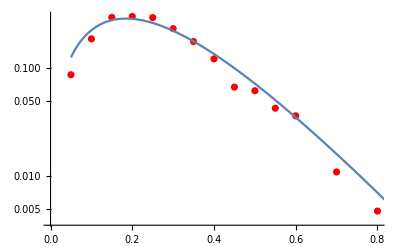

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.0005,T,µ,1.8,0.13957018]/.{c->1.0151609588879955,T->0.2799331867528091,µ->0.9321211191187952},{pt,0.05,0.9}]]
```

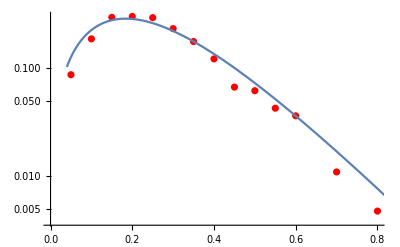

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.0065,T,µ,1.8,0.13957018]/.{c->1.0393616613823595,T->0.27969882634545823,µ->0.9244681013729683},{pt,0.04,0.9}]]
```

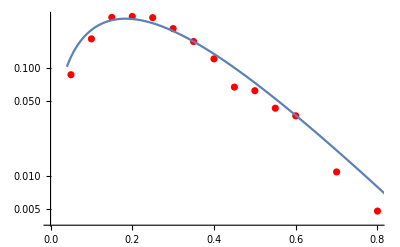

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.009,T,µ,1.8,0.13957018]/.{c->1.19972186617396,T->0.27924172558271254,µ->0.8839310907333465},{pt,0.04,0.9}]]
```

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.007,T,µ,1.8,0.13957018]/.{c->0.353529421201218,T->0.2817987963735472,µ->1.2271257265497806},{pt,0.04,0.8}]]
```

-Graphics-

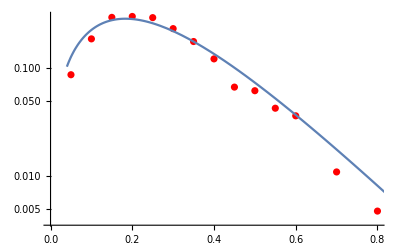

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.011,T,µ,1.8,0.13957018]/.{c->1.193177324936977,T->0.2791015087612885,µ->0.8851171201270605},{pt,0.04,0.9}]]
```

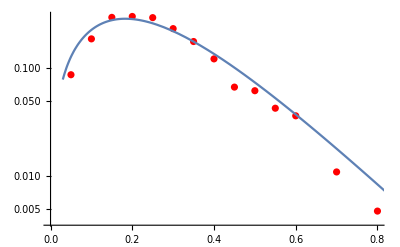

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.013,T,µ,1.8,0.13957018]/.{c->1.4947219562334255,T->0.2781317268374387,µ->0.822013553558829},{pt,0.03,0.9}]]
```

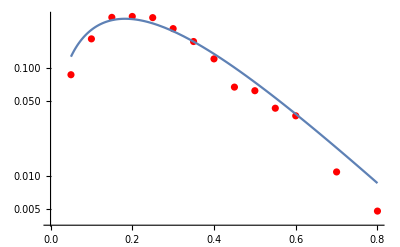

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.015,T,µ,1.8,0.13957018]/.{c->0.9010507738268393,T->0.27997060599136064,µ->0.9628839402742997},{pt,0.05,0.8}]]
```

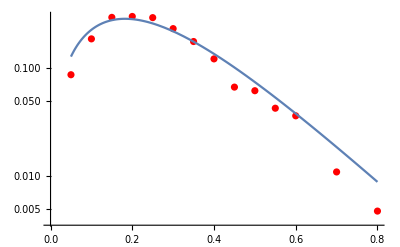

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.017,T,µ,1.8,0.13957018]/.{c->2.0059130618115857,T->0.2761901662547667,µ->0.739973339155949},{pt,0.05,0.8}]]
```

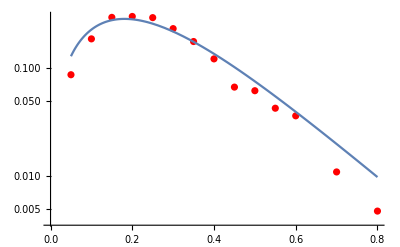

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.025,T,µ,1.8,0.13957018]/.{c->1.9239430677017473,T->0.2747248488173714,µ->0.7506466935646009},{pt,0.05,0.8}]]
```

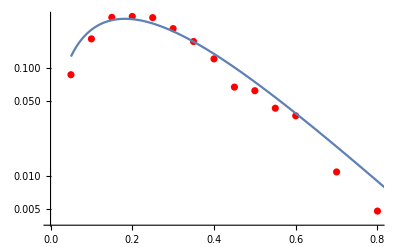

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.018,T,µ,1.8,0.13957018]/.{c->0.5699265430223482,T->0.28229272878613054,µ->1.0911064525327192},{pt,0.05,0.9}]]
```

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.02,T,µ,1.8,0.13957018]/.{c->1.1477537745289212,T->0.2786257661783393,µ->0.894372349081347},{pt,0.05,0.8}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt1y9,PlotStyle->Red],LogPlot[f[c,pt,1.015,T,µ,1.8,0.13957018]/.{c->0.9010507738268393,T->0.27997060599136064,µ->0.9628839402742997},{pt,0.05,0.8}]]
```

-Graphics-

```mathematica
pt2={{0.05,.21988},{0.1,.58023},{0.15,.92196},{0.2,1.09543},{0.25,1.08029},{0.3,1.037350},{0.35,0.88418},{0.4,0.77513},{0.45,0.67993},{0.5,0.51159},{0.55,0.39828},{0.6,0.34155},{0.7,0.23621},{0.8,0.154080},{0.9,0.09064},{1.0,0.06372},{1.25,0.02168},{1.5,0.00728}}
```

{{0.05,0.21988},{0.1,0.58023},{0.15,0.92196},{0.2,1.09543},{0.25,1.08029},{0.3,1.03735},{0.35,0.88418},{0.4,0.77513},{0.45,0.67993},{0.5,0.51159},{0.55,0.39828},{0.6,0.34155},{0.7,0.23621},{0.8,0.15408},{0.9,0.09064},{1.,0.06372},{1.25,0.02168},{1.5,0.00728}}

```mathematica
FindFit[pt2,f[c,pt,1.0515,T,µ,0,0.13957018],{c,T,µ},pt]
```

{c→0.477645,T→0.137938,µ→0.717856}

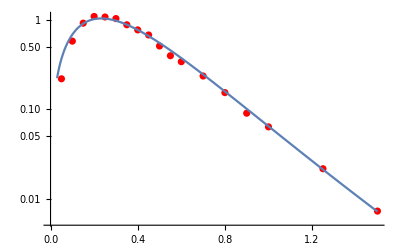

```mathematica
Show[ListLogPlot[pt2,PlotStyle->Red],LogPlot[f[c,pt,1.0515,T,µ,0,0.13957018]/.{c->0.47764450148796644,T->0.13793772046014233,µ->0.7178564663408552},{pt,0.03,1.5}]]
```

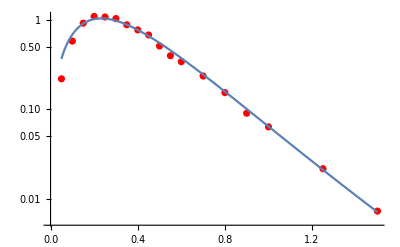

```mathematica
Show[ListLogPlot[pt2,PlotStyle->Red],LogPlot[f[c,pt,1.051,T,µ,0,0.13957018]/.{c->0.34842442148217667,T->0.1399854092409793,µ->0.7614570636386857},{pt,0.05,1.5}]]
```

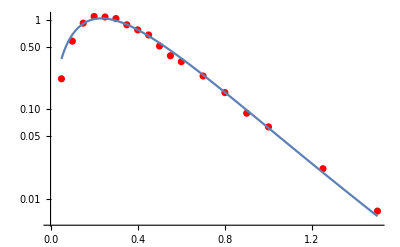

```mathematica
Show[ListLogPlot[pt2,PlotStyle->Red],LogPlot[f[c,pt,1.047,T,µ,0,0.13957018]/.{c->0.5294179802826126,T->0.13561207389494975,µ->0.7020378734930054},{pt,0.05,1.5}]]
```

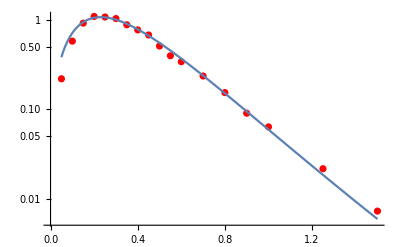

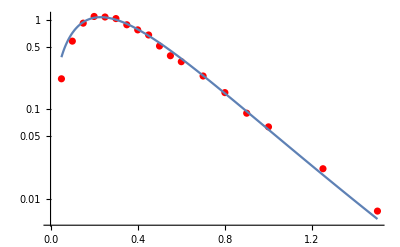

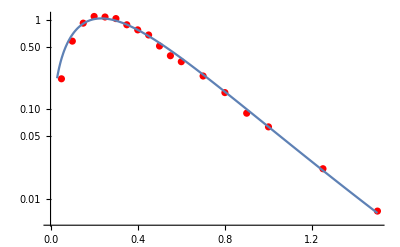

```mathematica
pt77=Show[ListLogPlot[pt2,PlotStyle->Red],LogPlot[f[c,pt,1.05,T,µ,0,0.13957018]/.{c->0.6758212396307578,T->0.13501605789371576,µ->0.6699775389856977},{pt,0.03,1.5}]]
```

```mathematica
Import["7pp.xlsx"]
```

{{{0.025,0.17843},{0.075,0.54225},{0.125,0.87953},{0.175,1.0148},{0.225,0.99349},{0.275,0.93572},{0.325,0.80337},{0.375,0.66787},{0.425,0.55509},{0.475,0.4746},{0.525,0.3996},{0.575,0.27952},{0.65,0.21471},{0.75,},{,0.13343},{0.85,0.08778},{0.95,0.0477},{1.125,0.01844},{1.375,0.00448}},{{0.025,0.15798},{0.075,0.47116},{0.125,0.68712},{0.175,0.83555},{0.225,0.83053},{0.275,0.77519},{0.325,0.62601},{0.375,0.55485},{0.425,0.43943},{0.475,0.36579},{0.525,0.31235},{0.575,0.24876},{0.65,0.17203},{0.75,},{,0.10122},{0.85,0.06521},{0.95,0.02896},{1.125,0.01272},{1.375,0.00312}},{{0.025,0.11903},{0.075,0.35156},{0.125,0.51305},{0.175,0.59681},{0.225,0.64145},{0.275,0.50977},{0.325,0.44216},{0.375,0.35244},{0.425,0.29825},{0.475,0.2264},{0.525,0.16845},{0.575,0.12721},{0.65,0.09546},{0.75,},{,0.05077},{0.85,0.02923},{0.95,0.01146},{1.125,0.0029}},{{0.025,0.09194},{0.075,0.25466},{0.125,0.36836},{0.175,0.38733},{0.225,0.35537},{0.275,0.3009},{0.325,0.21883},{0.375,0.19531},{0.425,0.14191},{0.475,0.1003},{0.525,0.08404},{0.575,0.05887},{0.65,0.03443},{0.75,},{,0.01657},{0.85,0.00427}},{{0.025,0.19869},{0.075,0.57846},{0.125,0.8697},{0.175,1.02689},{0.225,1.05151},{0.275,0.99351},{0.325,0.86177},{0.375,0.71881},{0.425,0.64902},{0.475,0.52855},{0.525,0.41673},{0.575,0.31395},{0.65,0.23847},{0.75,},{,0.14439},{0.85,0.101},{0.95,0.05153},{1.125,0.02157},{1.375,0.00662}},{{0.025,0.15745},{0.075,0.5027},{0.125,0.78569},{0.175,0.94457},{0.225,0.95169},{0.275,0.83373},{0.325,0.74783},{0.375,0.65275},{0.425,0.53818},{0.475,0.46065},{0.525,0.35282},{0.575,0.2922},{0.65,0.20457},{0.75,},{,0.12263},{0.85,0.06907},{0.95,0.04793},{1.125,0.01683},{1.375,0.00333},{,7.68462}},{{0.025,0.12095},{0.075,0.40723},{0.125,0.60071},{0.175,0.6938},{0.225,0.71533},{0.275,0.63926},{0.325,0.55411},{0.375,0.44507},{0.425,0.42239},{0.475,0.31041},{0.525,0.22678},{0.575,0.1906},{0.65,0.12458},{0.75,},{,0.07579},{0.85,0.04564},{0.95,0.02866},{1.125,0.00689},{1.375,0.00152},{,5.60972}},{{0.025,0.10337},{0.075,0.30392},{0.125,0.42291},{0.175,0.50205},{0.225,0.49242},{0.275,0.40698},{0.325,0.32359},{0.375,0.26292},{0.425,0.21477},{0.475,0.16616},{0.525,0.12123},{0.575,0.08585},{0.65,0.06558},{0.75,},{,0.02678},{0.85,0.0171},{0.95,0.00781},{1.125,0.00156},{1.375,0.},{,3.525}},{{0.025,0.08187},{0.075,0.21791},{0.125,0.30756},{0.175,0.31246},{0.225,0.27695},{0.275,0.21679},{0.325,0.15913},{0.375,0.12491},{0.425,0.09496},{0.475,0.05607},{0.525,0.03883},{0.575,0.02763},{0.65,0.01033},{0.75,},{,0.00371},{0.85,0.00106},{0.95,0.},{1.125,0.},{1.375,0.},{,1.93017}}}

```mathematica
{{{0.025,0.17843},{0.075,0.54225},{0.125,0.87953},{0.175,1.0148},{0.225,0.99349},{0.275,0.93572},{0.325,0.80337},{0.375,0.66787},{0.425,0.55509},{0.475,0.4746},{0.525,0.3996},{0.575,0.27952},{0.65,0.21471},{0.75,""},{"",0.13343},{0.85,0.08778},{0.95,0.0477},{1.125,0.01844},{1.375,0.00448}},{{0.025,0.15798},{0.075,0.47116},{0.125,0.68712},{0.175,0.83555},{0.225,0.83053},{0.275,0.77519},{0.325,0.62601},{0.375,0.55485},{0.425,0.43943},{0.475,0.36579},{0.525,0.31235},{0.575,0.24876},{0.65,0.17203},{0.75,""},{"",0.10122},{0.85,0.06521},{0.95,0.02896},{1.125,0.01272},{1.375,0.00312}},{{0.025,0.11903},{0.075,0.35156},{0.125,0.51305},{0.175,0.59681},{0.225,0.64145},{0.275,0.50977},{0.325,0.44216},{0.375,0.35244},{0.425,0.29825},{0.475,0.2264},{0.525,0.16845},{0.575,0.12721},{0.65,0.09546},{0.75,""},{"",0.05077},{0.85,0.02923},{0.95,0.01146},{1.125,0.0029}},{{0.025,0.09194},{0.075,0.25466},{0.125,0.36836},{0.175,0.38733},{0.225,0.35537},{0.275,0.3009},{0.325,0.21883},{0.375,0.19531},{0.425,0.14191},{0.475,0.1003},{0.525,0.08404},{0.575,0.05887},{0.65,0.03443},{0.75,""},{"",0.01657},{0.85,0.00427}},,,,,}
```

{{{0.025,0.17843},{0.075,0.54225},{0.125,0.87953},{0.175,1.0148},{0.225,0.99349},{0.275,0.93572},{0.325,0.80337},{0.375,0.66787},{0.425,0.55509},{0.475,0.4746},{0.525,0.3996},{0.575,0.27952},{0.65,0.21471},{0.75,},{,0.13343},{0.85,0.08778},{0.95,0.0477},{1.125,0.01844},{1.375,0.00448}},{{0.025,0.15798},{0.075,0.47116},{0.125,0.68712},{0.175,0.83555},{0.225,0.83053},{0.275,0.77519},{0.325,0.62601},{0.375,0.55485},{0.425,0.43943},{0.475,0.36579},{0.525,0.31235},{0.575,0.24876},{0.65,0.17203},{0.75,},{,0.10122},{0.85,0.06521},{0.95,0.02896},{1.125,0.01272},{1.375,0.00312}},{{0.025,0.11903},{0.075,0.35156},{0.125,0.51305},{0.175,0.59681},{0.225,0.64145},{0.275,0.50977},{0.325,0.44216},{0.375,0.35244},{0.425,0.29825},{0.475,0.2264},{0.525,0.16845},{0.575,0.12721},{0.65,0.09546},{0.75,},{,0.05077},{0.85,0.02923},{0.95,0.01146},{1.125,0.0029}},{{0.025,0.09194},{0.075,0.25466},{0.125,0.36836},{0.175,0.38733},{0.225,0.35537},{0.275,0.3009},{0.325,0.21883},{0.375,0.19531},{0.425,0.14191},{0.475,0.1003},{0.525,0.08404},{0.575,0.05887},{0.65,0.03443},{0.75,},{,0.01657},{0.85,0.00427}},Null,Null,Null,Null,Null}

```mathematica
pt2y02={{0.025,0.19869},{0.075,0.57846},{0.125,0.8697},{0.175,1.02689},{0.225,1.05151},{0.275,0.99351},{0.325,0.86177},{0.375,0.71881},{0.425,0.64902},{0.475,0.52855},{0.525,0.41673},{0.575,0.31395},{0.65,0.23847},{0.75,0.14439},{0.85,0.101},{0.95,0.05153},{1.125,0.02157},{1.375,0.00662}}
```

{{0.025,0.19869},{0.075,0.57846},{0.125,0.8697},{0.175,1.02689},{0.225,1.05151},{0.275,0.99351},{0.325,0.86177},{0.375,0.71881},{0.425,0.64902},{0.475,0.52855},{0.525,0.41673},{0.575,0.31395},{0.65,0.23847},{0.75,0.14439},{0.85,0.101},{0.95,0.05153},{1.125,0.02157},{1.375,0.00662}}

```mathematica
FindFit[pt2y02,f[c,pt,1.046,T,µ,0.2,0.13957018],{c,T,µ},pt]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{c→0.324755,T→0.129003,µ→0.738047}

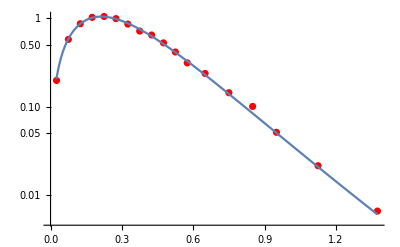

```mathematica
Show[ListLogPlot[pt2y02,PlotStyle->Red],LogPlot[f[c,pt,1.047,T,µ,0.2,0.13957018]/.{c->0.34622762853235534,T->0.12901744525596248,µ->0.7303046910277672},{pt,0.025,1.375}]]
```

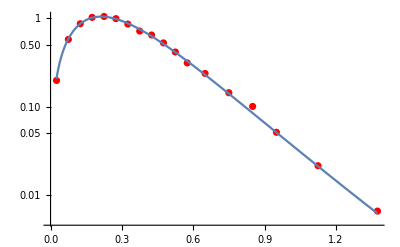

```mathematica
Show[ListLogPlot[pt2y02,PlotStyle->Red],LogPlot[f[c,pt,1.048,T,µ,0.2,0.13957018]/.{c->0.38780911106019683,T->0.12870961303344366,µ->0.7161725870708421},{pt,0.025,1.375}]]
```

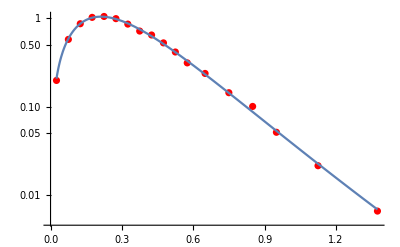

```mathematica
Show[ListLogPlot[pt2y02,PlotStyle->Red],LogPlot[f[c,pt,1.052,T,µ,0.2,0.13957018]/.{c->0.3901434980692861,T->0.13019253206697015,µ->0.7172471021123743},{pt,0.025,1.375}]]
```

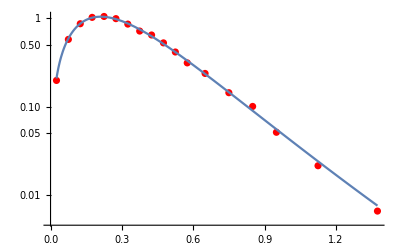

```mathematica
Show[ListLogPlot[pt2y02,PlotStyle->Red],LogPlot[f[c,pt,1.056,T,µ,0.2,0.13957018]/.{c->0.31963063554075677,T->0.1332094076483407,µ->0.7455159431436694},{pt,0.025,1.375}]]
```

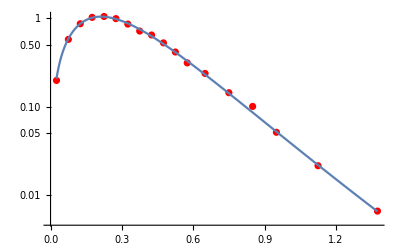

```mathematica
Show[ListLogPlot[pt2y02,PlotStyle->Red],LogPlot[f[c,pt,1.05,T,µ,0.2,0.13957018]/.{c->0.3223245008305637,T->0.13067198244545666,µ->0.7411556981047489},{pt,0.025,1.375}]]
```

```mathematica
pt2y2={{0.025,0.17843},{0.075,0.54225},{0.125,0.87953},{0.175,1.0148},{0.225,0.99349},{0.275,0.93572},{0.325,0.80337},{0.375,0.66787},{0.425,0.55509},{0.475,0.4746},{0.525,0.3996},{0.575,0.27952},{0.65,0.21471},{0.75,0.13343},{0.85,0.08778},{0.95,0.0477},{1.125,0.01844},{1.375,0.00448}}
```

{{0.025,0.17843},{0.075,0.54225},{0.125,0.87953},{0.175,1.0148},{0.225,0.99349},{0.275,0.93572},{0.325,0.80337},{0.375,0.66787},{0.425,0.55509},{0.475,0.4746},{0.525,0.3996},{0.575,0.27952},{0.65,0.21471},{0.75,0.13343},{0.85,0.08778},{0.95,0.0477},{1.125,0.01844},{1.375,0.00448}}

```mathematica
FindFit[pt2y2,f[c,pt,1.0475
,T,µ,0.4,0.13957018],{c,T,µ},pt]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{c→0.77954,T→0.127267,µ→0.641076}

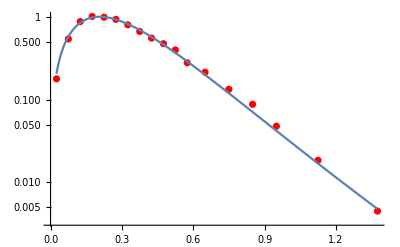

```mathematica
Show[ListLogPlot[pt2y2,PlotStyle->Red],LogPlot[f[c,pt,1.0475,T,µ,0.4,0.13957018]/.{c->0.7795399839431747,T->0.12726691847386074,µ->0.6410755876839003},{pt,0.025,1.375}]]
```

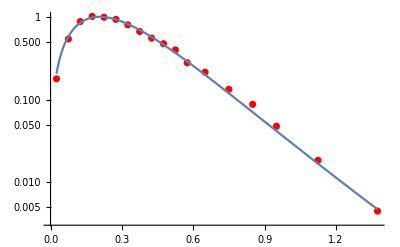

```mathematica
Show[ListLogPlot[pt2y2,PlotStyle->Red],LogPlot[f[c,pt,1.0472,T,µ,0.4,0.13957018]/.{c->0.46840413637274536,T->0.13027804324951556,µ->0.7065768428219452},{pt,0.025,1.375}]]
```

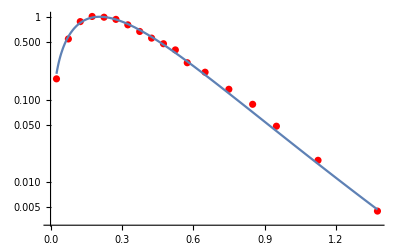

```mathematica
Show[ListLogPlot[pt2y2,PlotStyle->Red],LogPlot[f[c,pt,1.0469,T,µ,0.4,0.13957018]/.{c->0.6529472809230229,T->0.12816027053032944,µ->0.663557614295982},{pt,0.025,1.375}]]
```

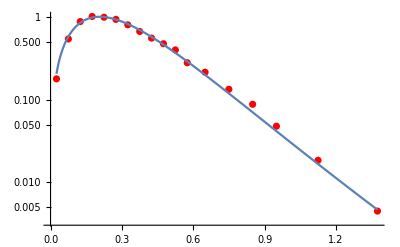

```mathematica
Show[ListLogPlot[pt2y2,PlotStyle->Red],LogPlot[f[c,pt,1.0467,T,µ,0.4,0.13957018]/.{c->0.20584839623024304,T->0.13519469446580182,µ->0.815433266325666},{pt,0.025,1.375}]]
```

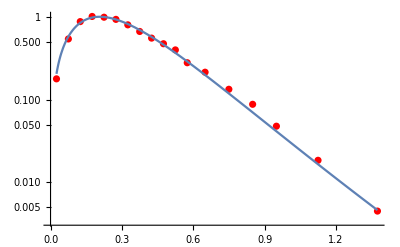

```mathematica
Show[ListLogPlot[pt2y2,PlotStyle->Red],LogPlot[f[c,pt,1.0463,T,µ,0.4,0.13957018]/.{c->0.4612165348219493,T->0.1300546119099347,µ->0.7082407645609129},{pt,0.025,1.375}]]
```

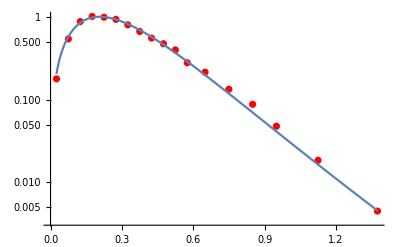

```mathematica
Show[ListLogPlot[pt2y2,PlotStyle->Red],LogPlot[f[c,pt,1.0459,T,µ,0.4,0.13957018]/.{c->0.8199170892579624,T->0.12652744911303063,µ->0.6343193090444088},{pt,0.025,1.375}]]
```

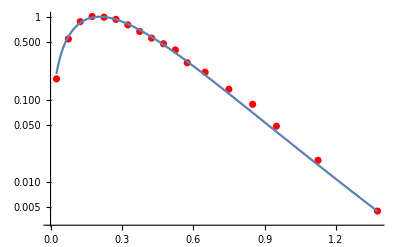

```mathematica
Show[ListLogPlot[pt2y2,PlotStyle->Red],LogPlot[f[c,pt,1.0453,T,µ,0.4,0.13957018]/.{c->0.47002926803372846,T->0.12959042083084574,µ->0.7053971125593256},{pt,0.025,1.375}]]
```

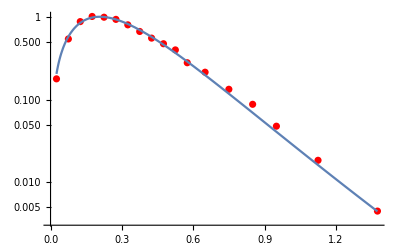

```mathematica
Show[ListLogPlot[pt2y2,PlotStyle->Red],LogPlot[f[c,pt,1.0451,T,µ,0.4,0.13957018]/.{c->0.8217408096098189,T->0.12629807748351177,µ->0.6338703748866874},{pt,0.025,1.375}]]
```

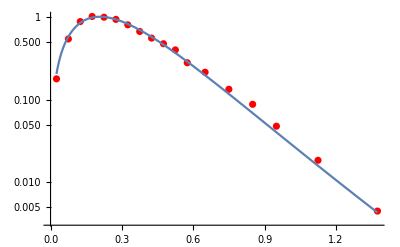

```mathematica
Show[ListLogPlot[pt2y2,PlotStyle->Red],LogPlot[f[c,pt,1.044,T,µ,0.4,0.13957018]/.{c->0.4729658927374292,T->0.1291011062304602,µ->0.704095836500786},{pt,0.025,1.375}]]
```

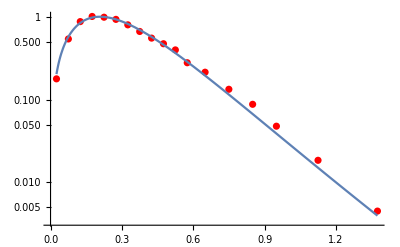

```mathematica
Show[ListLogPlot[pt2y2,PlotStyle->Red],LogPlot[f[c,pt,1.041,T,µ,0.4,0.13957018]/.{c->0.6611358702332905,T->0.12631577268730856,µ->0.660359982315542},{pt,0.025,1.375}]]
```

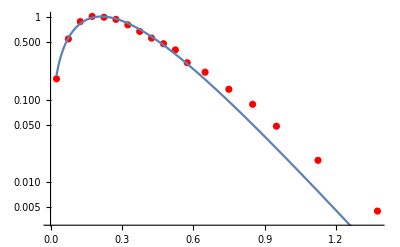

```mathematica
Show[ListLogPlot[pt2y2,PlotStyle->Red],LogPlot[f[c,pt,1.01,T,µ,0.4,0.13957018]/.{c->0.996230298558583,T->0.11693575819552283,µ->0.6041264921220956},{pt,0.025,1.375}]]
```

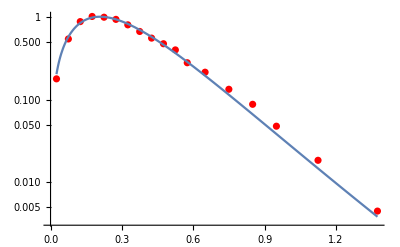

```mathematica
Show[ListLogPlot[pt2y2,PlotStyle->Red],LogPlot[f[c,pt,1.04,T,µ,0.4,0.13957018]/.{c->0.7989842306803091,T->0.12506727736728598,µ->0.6363145837353018},{pt,0.025,1.375}]]
```

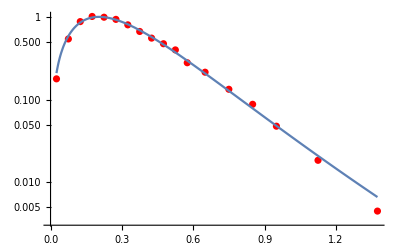

```mathematica
Show[ListLogPlot[pt2y2,PlotStyle->Red],LogPlot[f[c,pt,1.06,T,µ,0.4,0.13957018]/.{c->0.4644716608235632,T->0.13493260453081357,µ->0.7127016549693713},{pt,0.025,1.375}]]
```

```mathematica
Show[ListLogPlot[pt2y2,PlotStyle->Red],LogPlot[f[c,pt,1.08,T,µ,0.4,0.13957018]/.{c->0.5005072067889612,T->0.14160380322631064,µ->0.7101702331466375},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y2,PlotStyle->Red],LogPlot[f[c,pt,1.1,T,µ,0.4,0.13957018]/.{c->0.6329141208924947,T->0.14580911516645284,µ->0.6833221090821235},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt2y2g=Show[ListLogPlot[pt2y2,PlotStyle->Red],LogPlot[f[c,pt,1.0515,T,µ,0.4,0.13957018]/.{c->0.45822416838849644,T->0.13195024218380041,µ->0.7111376043378469},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt2y06={{0.025,0.15745},{0.075,0.5027},{0.125,0.78569},{0.175,0.94457},{0.225,0.95169},{0.275,0.83373},{0.325,0.74783},{0.375,0.65275},{0.425,0.53818},{0.475,0.46065},{0.525,0.35282},{0.575,0.2922},{0.65,0.20457},{0.75,0.12263},{0.85,0.06907},{0.95,0.04793},{1.125,0.01683},{1.375,0.00333}}
```

{{0.025,0.15745},{0.075,0.5027},{0.125,0.78569},{0.175,0.94457},{0.225,0.95169},{0.275,0.83373},{0.325,0.74783},{0.375,0.65275},{0.425,0.53818},{0.475,0.46065},{0.525,0.35282},{0.575,0.2922},{0.65,0.20457},{0.75,0.12263},{0.85,0.06907},{0.95,0.04793},{1.125,0.01683},{1.375,0.00333}}

```mathematica
FindFit[pt2y06,f[c,pt,1.03,T,µ,0.6,0.13957018],{c,T,µ},pt]
```

{c→0.567012,T→0.137029,µ→0.725306}

```mathematica
Show[ListLogPlot[pt2y06,PlotStyle->Red],LogPlot[f[c,pt,1.04,T,µ,0.6,0.13957018]/.{c->0.5640395758196476,T->0.14026715386714092,µ->0.7288869937265499},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y06,PlotStyle->Red],LogPlot[f[c,pt,1.035,T,µ,0.6,0.13957018]/.{c->0.5638161684588243,T->0.13865125076569915,µ->0.727506440836582},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y06,PlotStyle->Red],LogPlot[f[c,pt,1.03,T,µ,0.6,0.13957018]/.{c->0.5670115833527749,T->0.13702894957977868,µ->0.7253063902450796},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt2y3={{0.025,0.15798},{0.075,0.47116},{0.125,0.68712},{0.175,0.83555},{0.225,0.83053},{0.275,0.77519},{0.325,0.62601},{0.375,0.55485},{0.425,0.43943},{0.475,0.36579},{0.525,0.31235},{0.575,0.24876},{0.65,0.17203},{0.75,0.10122},{0.85,0.06521},{0.95,0.02896},{1.125,0.01272},{1.375,0.00312}}
```

{{0.025,0.15798},{0.075,0.47116},{0.125,0.68712},{0.175,0.83555},{0.225,0.83053},{0.275,0.77519},{0.325,0.62601},{0.375,0.55485},{0.425,0.43943},{0.475,0.36579},{0.525,0.31235},{0.575,0.24876},{0.65,0.17203},{0.75,0.10122},{0.85,0.06521},{0.95,0.02896},{1.125,0.01272},{1.375,0.00312}}

```mathematica
FindFit[pt2y3,f[c,pt,1.032,T,µ,0.8,0.13957018],{c,T,µ},pt]
```

FindFit::nrlnum: The function value {-0.15798+0. ⅈ,-0.47116+0. ⅈ,-0.68712+0. ⅈ,-0.83555+0. ⅈ,-0.83053+0. ⅈ,-0.77519+0. ⅈ,-0.62601+0. ⅈ,-0.55485+0. ⅈ,-0.439429+0. ⅈ,-0.365783+0. ⅈ,-0.312298+0. ⅈ,-0.248337+0. ⅈ,-0.159522+0. ⅈ,1.89555+0. ⅈ,756.698+0. ⅈ,1.02134×10^6+0. ⅈ,1.04376×10^14+0. ⅈ,-2.03452×10^42+2.03452×10^42 ⅈ} is not a list of real numbers with dimensions {18} at {c,T,µ} = {0.446386,-0.0267941,0.974299}.

{c→0.446386,T→-0.0267941,µ→0.974299}

```mathematica
Show[ListLogPlot[pt2y3,PlotStyle->Red],LogPlot[f[c,pt,1.037,T,µ,0.8,0.13957018]/.{c->0.53064,T->0.15293241203294905,µ->0.789643},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt2y3,PlotStyle->Red],Plot[f[c,pt,1.029,T,µ,0.8,0.13957018]/.{c->0.5141420918022167,T->0.14962803261341326,µ->0.7838744091899617},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y3,PlotStyle->Red],LogPlot[f[c,pt,1.025,T,µ,0.8,0.13957018]/.{c->0.15339378205943688,T->0.1528647765296425,µ->0.9649031920997865},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt2y3g=Show[ListLogPlot[pt2y3,PlotStyle->Red],LogPlot[f[c,pt,1.03,T,µ,0.8,0.13957018]/.{c->0.3315142674069422,T->0.15194618469733515,µ->0.8503897873306356},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y3,PlotStyle->Red],LogPlot[f[c,pt,1.01,T,µ,0.8,0.13957018]/.{c->0.7865075049907984,T->0.1428704593214639,µ->0.7178705245043434},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt2y10={{0.025,0.12095},{0.075,0.40723},{0.125,0.60071},{0.175,0.6938},{0.225,0.71533},{0.275,0.63926},{0.325,0.55411},{0.375,0.44507},{0.425,0.42239},{0.475,0.31041},{0.525,0.22678},{0.575,0.1906},{0.65,0.12458},{0.75,0.07579},{0.85,0.04564},{0.95,0.02866},{1.125,0.00689},{1.375,0.00152}}
```

{{0.025,0.12095},{0.075,0.40723},{0.125,0.60071},{0.175,0.6938},{0.225,0.71533},{0.275,0.63926},{0.325,0.55411},{0.375,0.44507},{0.425,0.42239},{0.475,0.31041},{0.525,0.22678},{0.575,0.1906},{0.65,0.12458},{0.75,0.07579},{0.85,0.04564},{0.95,0.02866},{1.125,0.00689},{1.375,0.00152}}

```mathematica
FindFit[pt2y10,f[c,pt,1.0345,T,µ,1.0,0.13957018],{c,T,µ},pt]
```

{c→0.715669,T→0.169093,µ→0.792196}

```mathematica
Show[ListLogPlot[pt2y10,PlotStyle->Red],LogPlot[f[c,pt,1.0345,T,µ,1.,0.13957018]/.{c->0.7156686373541779,T->0.16909269890391976,µ->0.7921961661659975},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y10,PlotStyle->Red],LogPlot[f[c,pt,1.037,T,µ,1.,0.13957018]/.{c->0.24125972858568173,T->0.17673136002364362,µ->0.9808200198607453},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y10,PlotStyle->Red],LogPlot[f[c,pt,1.035,T,µ,1.,0.13957018]/.{c->1.3462874889510899,T->0.16552485221212013,µ->0.6864917868218359},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y10,PlotStyle->Red],LogPlot[f[c,pt,1.028,T,µ,1.,0.13957018]/.{c->0.522282108935635,T->0.1688471980176884,µ->0.8444478263857036},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y10,PlotStyle->Red],LogPlot[f[c,pt,1.026,T,µ,1.,0.13957018]/.{c->0.28632047627879087,T->0.1708579216656496,µ->0.9459516198722093},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y10,PlotStyle->Red],LogPlot[f[c,pt,1.024,T,µ,1.,0.13957018]/.{c->1.1077881509272636,T->0.16457526131402792,µ->0.7187792818183485},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y10,PlotStyle->Red],LogPlot[f[c,pt,1.019,T,µ,1.,0.13957018]/.{c->1.1189445525876274,T->0.1636064593039299,µ->0.7170903904139692},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y10,PlotStyle->Red],LogPlot[f[c,pt,1.013,T,µ,1.,0.13957018]/.{c->0.2915350369768339,T->0.1653650941368469,µ->0.9375183767314644},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y10,PlotStyle->Red],LogPlot[f[c,pt,1.005,T,µ,1.,0.13957018]/.{c->0.9740121721679107,T->0.16114646557093149,µ->0.7393094852235673},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y10,PlotStyle->Red],LogPlot[f[c,pt,1.015,T,µ,1.,0.13957018]/.{c->0.967665546617041,T->0.16322239714288111,µ->0.7407393206950809},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt2y4={{0.025,0.11903},{0.075,0.35156},{0.125,0.51305},{0.175,0.59681},{0.225,0.64145},{0.275,0.50977},{0.325,0.44216},{0.375,0.35244},{0.425,0.29825},{0.475,0.2264},{0.525,0.16845},{0.575,0.12721},{0.65,0.09546},{0.75,0.05077},{0.85,0.02923},{0.95,0.01146},{1.125,0.0029}}
```

{{0.025,0.11903},{0.075,0.35156},{0.125,0.51305},{0.175,0.59681},{0.225,0.64145},{0.275,0.50977},{0.325,0.44216},{0.375,0.35244},{0.425,0.29825},{0.475,0.2264},{0.525,0.16845},{0.575,0.12721},{0.65,0.09546},{0.75,0.05077},{0.85,0.02923},{0.95,0.01146},{1.125,0.0029}}

```mathematica
FindFit[pt2y4,f[c,pt,1.01852,T,µ,1.2,0.13957018],{c,T,µ},pt]
```

FindFit::nrlnum: The function value {3.6277×10^80+4.92331×10^78 ⅈ,7.478×10^80+1.01487×10^79 ⅈ,6.39985×10^80+8.68551×10^78 ⅈ,3.8055×10^80+5.16461×10^78 ⅈ,1.85586×10^80+2.51866×10^78 ⅈ,8.06816×10^79+1.09496×10^78 ⅈ,«6»,6.04323×10^76+8.20153×10^74 ⅈ,8.91274×10^75+1.20959×10^74 ⅈ,1.3712×10^75+1.86091×10^73 ⅈ,2.21091×10^74+3.00052×10^72 ⅈ,1.01991×10^73+1.38416×10^71 ⅈ} is not a list of real numbers with dimensions {17} at {c,T,µ} = {108.868,-1.929,-107.234}.

{c→108.868,T→-1.929,µ→-107.234}

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0158,T,µ,1.2,0.13957018]/.{c->0.6301819678934231,T->0.18068201927709912,µ->0.8635942012044611},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0156,T,µ,1.2,0.13957018]/.{c->0.7141627270551523,T->0.18027637311016081,µ->0.8410012133559372},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0152,T,µ,1.2,0.13957018]/.{c->0.9825550006824485,T->0.1793070330912181,µ->0.7836319886079454},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0146,T,µ,1.2,0.13957018]/.{c->0.9624474308654819,T->0.17924972446704399,µ->0.7873440643763727},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0142,T,µ,1.2,0.13957018]/.{c->0.6808748395661637,T->0.1800567255457377,µ->0.8495116049070145},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0138,T,µ,1.2,0.13957018]/.{c->0.7172322580279004,T->0.1798265866262623,µ->0.8401254714056181},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0132,T,µ,1.2,0.13957018]/.{c->0.7173171980940283,T->0.17968063484443506,µ->0.8400699324464183},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0131,T,µ,1.2,0.13957018]/.{c->0.9761857590164592,T->0.17893263705723814,µ->0.7848174274023341},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0129,T,µ,1.2,0.13957018]/.{c->0.9489455144319656,T->0.17896066203627506,µ->0.7898831577161988},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0125,T,µ,1.2,0.13957018]/.{c->0.8041741261300952,T->0.1792545628255777,µ->0.819526916171002},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.012,T,µ,1.2,0.13957018]/.{c->0.8167376988641588,T->0.1791104755309668,µ->0.8167347190779588},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.009,T,µ,1.2,0.13957018]/.{c->0.6812767349933309,T->0.17874726125842216,µ->0.8490415307733579},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0158,T,µ,1.2,0.13957018]/.{c->0.6301819678934231,T->0.18068201927709912,µ->0.8635942012044611},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0149,T,µ,1.2,0.13957018]/.{c->0.8208699640062631,T->0.1797321572183102,µ->0.8159062418914966},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt2y4,PlotStyle->Red],Plot[f[c,pt,1.0149,T,µ,1.2,0.13957018]/.{c->0.8208699640062631,T->0.1797321572183102,µ->0.8159062418914966},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0145,T,µ,1.2,0.13957018]/.{c->0.7278263885073258,T->0.1799584208956533,µ->0.8375264219803721},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0142,T,µ,1.2,0.13957018]/.{c->0.6808748395661637,T->0.1800567255457377,µ->0.8495116049070145},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0138,T,µ,1.2,0.13957018]/.{c->0.7172322580279004,T->0.1798265866262623,µ->0.8401254714056181},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0133,T,µ,1.2,0.13957018]/.{c->0.8180640883645246,T->0.17939106751913977,µ->0.8164789953646211},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0131,T,µ,1.2,0.13957018]/.{c->0.9761857590164592,T->0.17893263705723814,µ->0.7848174274023341},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.01295,T,µ,1.2,0.13957018]/.{c->0.5829256012158004,T->0.18010319286072346,µ->0.8773694600047667},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0126,T,µ,1.2,0.13957018]/.{c->0.7144796418732782,T->0.1795440621542494,µ->0.840747285384398},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0125,T,µ,1.2,0.13957018]/.{c->0.8041741261300952,T->0.1792545628255777,µ->0.819526916171002},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.011,T,µ,1.2,0.13957018]/.{c->0.9765495816617535,T->0.1785406496785474,µ->0.784769419038762},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0095,T,µ,1.2,0.13957018]/.{c->0.7140287133346984,T->0.17879283737466148,µ->0.8406795800502164},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0085,T,µ,1.2,0.13957018]/.{c->0.670991842924934,T->0.17864509925091743,µ->0.8517237516667896},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.00335,T,µ,1.2,0.13957018]/.{c->0.8565061253261889,T->0.17720106125958315,µ->0.8080685207772834},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0075,T,µ,1.2,0.13957018]/.{c->0.8413322081013338,T->0.17808967584454388,µ->0.8113263495333337},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.0095,T,µ,1.2,0.13957018]/.{c->0.7140287133346984,T->0.17879283737466148,µ->0.8406795800502164},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
pt2y4g=Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.009,T,µ,1.2,0.13957018]/.{c->0.6812767349933309,T->0.17874726125842216,µ->0.8490415307733579},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.007,T,µ,1.2,0.13957018]/.{c->0.8055995650651998,T->0.17803773762909636,µ->0.8190412170523335},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.005,T,µ,1.2,0.13957018]/.{c->0.8237839798325489,T->0.177578943351741,µ->0.8150150815774752},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y4,PlotStyle->Red],LogPlot[f[c,pt,1.001,T,µ,1.2,0.13957018]/.{c->0.6687363140728121,T->0.17675702768903426,µ->0.8517621509589484},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
pt2y14={{0.025,0.10337},{0.075,0.30392},{0.125,0.42291},{0.175,0.50205},{0.225,0.49242},{0.275,0.40698},{0.325,0.32359},{0.375,0.26292},{0.425,0.21477},{0.475,0.16616},{0.525,0.12123},{0.575,0.08585},{0.65,0.06558},{0.75,0.02678},{0.85,0.0171},{0.95,0.00781},{1.125,0.00156}}
```

{{0.025,0.10337},{0.075,0.30392},{0.125,0.42291},{0.175,0.50205},{0.225,0.49242},{0.275,0.40698},{0.325,0.32359},{0.375,0.26292},{0.425,0.21477},{0.475,0.16616},{0.525,0.12123},{0.575,0.08585},{0.65,0.06558},{0.75,0.02678},{0.85,0.0171},{0.95,0.00781},{1.125,0.00156}}

```mathematica
FindFit[pt2y14,f[c,pt,1.0155,T,µ,1.4,0.13957018],{c,T,µ},pt]
```

FindFit::nrlnum: The function value {-9.59509×10^39-1.89199×10^41 ⅈ,-2.88213×10^40-5.68308×10^41 ⅈ,-4.69632×10^40-9.26035×10^41 ⅈ,-6.18415×10^40-1.21941×10^42 ⅈ,-7.19901×10^40-1.41952×10^42 ⅈ,-7.71747×10^40-1.52176×10^42 ⅈ,«6»,-4.05422×10^40-7.99425×10^41 ⅈ,-2.91285×10^40-5.74366×10^41 ⅈ,-2.02876×10^40-4.00036×10^41 ⅈ,-1.3809×10^40-2.7229×10^41 ⅈ,-6.77321×10^39-1.33556×10^41 ⅈ} is not a list of real numbers with dimensions {17} at {c,T,µ} = {114.296,-1.42523,-112.675}.

{c→114.296,T→-1.42523,µ→-112.675}

```mathematica
Show[ListLogPlot[pt2y14,PlotStyle->Red],LogPlot[f[c,pt,1.01125,T,µ,1.4,0.13957018]/.{c->1.0087457580812638,T->0.1999466142221448,µ->0.8268431498903761},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y14,PlotStyle->Red],LogPlot[f[c,pt,1.027,T,µ,1.4,0.13957018]/.{c->0.998868,T->0.19990911,µ->0.848479},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y14,PlotStyle->Red],LogPlot[f[c,pt,1.012,T,µ,1.4,0.13957018]/.{c->0.9518814484120066,T->0.20018916065264972,µ->0.8383999415730636},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y14,PlotStyle->Red],LogPlot[f[c,pt,1.007,T,µ,1.4,0.13957018]/.{c->0.617817265265202,T->0.20004815778136448,µ->0.9250597413144611},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y14,PlotStyle->Red],LogPlot[f[c,pt,1.005,T,µ,1.4,0.13957018]/.{c->0.615978038655341,T->0.19958027078735896,µ->0.925615148285574},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt2y14,PlotStyle->Red],Plot[f[c,pt,1.01425,T,µ,1.4,0.13957018]/.{c->0.9140229225683875,T->0.20064150927091762,µ->0.8463945652136784},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y14,PlotStyle->Red],LogPlot[f[c,pt,1.0142,T,µ,1.4,0.13957018]/.{c->1.0397562184496012,T->0.20026675750759015,µ->0.8205623143844225},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y14,PlotStyle->Red],LogPlot[f[c,pt,1.0141,T,µ,1.4,0.13957018]/.{c->1.2496562028039302,T->0.19973505158749755,µ->0.7837946983127543},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt2y14,PlotStyle->Red],Plot[f[c,pt,1.0139,T,µ,1.4,0.13957018]/.{c->0.9109386091853854,T->0.2005956966574539,µ->0.847093204768573},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y14,PlotStyle->Red],LogPlot[f[c,pt,1.0138,T,µ,1.4,0.13957018]/.{c->0.6141366533172935,T->0.20167413005640353,µ->0.9263947732106551},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y14,PlotStyle->Red],LogPlot[f[c,pt,1.0132,T,µ,1.4,0.13957018]/.{c->0.893856398972119,T->0.2005348921988175,µ->0.8509296954215338},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y14,PlotStyle->Red],LogPlot[f[c,pt,1.0127,T,µ,1.4,0.13957018]/.{c->0.6906527409892079,T->0.20111144194057406,µ->0.9027406173417638},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y14,PlotStyle->Red],LogPlot[f[c,pt,1.0142,T,µ,1.4,0.13957018]/.{c->1.0397562184496012,T->0.20026675750759015,µ->0.8205623143844225},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt2y14,PlotStyle->Red],Plot[f[c,pt,1.0125,T,µ,1.4,0.13957018]/.{c->1.1454444472129277,T->0.19980101100017308,µ->0.8013401098177148},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y14,PlotStyle->Red],LogPlot[f[c,pt,1.014,T,µ,1.4,0.13957018]/.{c->0.8188678545101415,T->0.20091102909574002,µ->0.8684790426974097},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y14,PlotStyle->Red],LogPlot[f[c,pt,1.012,T,µ,1.4,0.13957018]/.{c->0.9518814484120066,T->0.20018916065264972,µ->0.8383999415730636},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y14,PlotStyle->Red],LogPlot[f[c,pt,1.007,T,µ,1.4,0.13957018]/.{c->0.617817265265202,T->0.20004815778136448,µ->0.9250597413144611},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y14,PlotStyle->Red],LogPlot[f[c,pt,1.005,T,µ,1.4,0.13957018]/.{c->0.615978038655341,T->0.19958027078735896,µ->0.925615148285574},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y14,PlotStyle->Red],LogPlot[f[c,pt,1.0002,T,µ,1.4,0.13957018]/.{c->1.0183400828513252,T->0.19843198729454806,µ->0.8257539183491212},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
pt2y5={{0.025,0.09194},{0.075,0.25466},{0.125,0.36836},{0.175,0.38733},{0.225,0.35537},{0.275,0.3009},{0.325,0.21883},{0.375,0.19531},{0.425,0.14191},{0.475,0.1003},{0.525,0.08404},{0.575,0.05887},{0.65,0.03443},{0.75,0.01657},{0.85,0.00427}}
```

{{0.025,0.09194},{0.075,0.25466},{0.125,0.36836},{0.175,0.38733},{0.225,0.35537},{0.275,0.3009},{0.325,0.21883},{0.375,0.19531},{0.425,0.14191},{0.475,0.1003},{0.525,0.08404},{0.575,0.05887},{0.65,0.03443},{0.75,0.01657},{0.85,0.00427}}

```mathematica
FindFit[pt2y5,f[c,pt,1.022,T,µ,1.6,0.13957018],{c,T,µ},pt]
```

{c→0.651751,T→0.223077,µ→0.96315}

```mathematica
Show[ListLogPlot[pt2y5,PlotStyle->Red],LogPlot[f[c,pt,1.022,T,µ,1.6,0.13957018]/.{c->0.6517510281062562,T->0.22307684257461588,µ->0.9631501974201829},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y5,PlotStyle->Red],LogPlot[f[c,pt,1.025,T,µ,1.6,0.13957018]/.{c->0.6518437453412463,T->0.22360360082627087,µ->0.9629130586957368},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y5,PlotStyle->Red],LogPlot[f[c,pt,1.02,T,µ,1.6,0.13957018]/.{c->0.5715696031578664,T->0.2233114525782923,µ->0.9925628843664792},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y5,PlotStyle->Red],LogPlot[f[c,pt,1.01,T,µ,1.6,0.13957018]/.{c->1.25428505357866,T->0.21953847010244268,µ->0.8197546857172241},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt2y5,PlotStyle->Red],Plot[f[c,pt,1.002,T,µ,1.6,0.13957018]/.{c->0.6499294544013099,T->0.21959607844841297,µ->0.9650759913300705},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y5,PlotStyle->Red],LogPlot[f[c,pt,1.005,T,µ,1.6,0.13957018]/.{c->1.2049110130536962,T->0.219438059699071,µ->0.8292193445908249},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y5,PlotStyle->Red],LogPlot[f[c,pt,1.0002,T,µ,1.6,0.13957018]/.{c->0.5717637350842636,T->0.21929014755990622,µ->0.9932872992117341},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y5,PlotStyle->Red],LogPlot[f[c,pt,1.0007,T,µ,1.6,0.13957018]/.{c->1.0489754555330575,T->0.2192975251613574,µ->0.8601606625909141},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y5,PlotStyle->Red],LogPlot[f[c,pt,1.006,T,µ,1.6,0.13957018]/.{c->1.0719173958960135,T->0.21962980871224394,µ->0.8547688514822742},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt2y5,PlotStyle->Red],Plot[f[c,pt,1.001,T,µ,1.6,0.13957018]/.{c->0.6699682317422789,T->0.21941627337400102,µ->0.958475466193296},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y5,PlotStyle->Red],LogPlot[f[c,pt,1.005,T,µ,1.6,0.13957018]/.{c->1.2049110130536962,T->0.219438059699071,µ->0.8292193445908249},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y5,PlotStyle->Red],LogPlot[f[c,pt,1.01,T,µ,1.6,0.13957018]/.{c->1.25428505357866,T->0.21953847010244268,µ->0.8197546857172241},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
pt2y5g=Show[ListLogPlot[pt2y5,PlotStyle->Red],LogPlot[f[c,pt,1.02,T,µ,1.6,0.13957018]/.{c->0.5715696031578664,T->0.2233114525782923,µ->0.9925628843664792},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y5,PlotStyle->Red],LogPlot[f[c,pt,1.04,T,µ,1.6,0.13957018]/.{c->0.5697566667880688,T->0.22748341604463998,µ->0.9923875027424703},{pt,0.025,0.95}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y5,PlotStyle->Red],LogPlot[f[c,pt,1.009,T,µ,1.6,0.13957018]/.{c->1.0716614187556037,T->0.21982063195606708,µ->0.8544513679645798},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
pt2y18={{0.025,0.08187},{0.075,0.21791},{0.125,0.30756},{0.175,0.31246},{0.225,0.27695},{0.275,0.21679},{0.325,0.15913},{0.375,0.12491},{0.425,0.09496},{0.475,0.05607},{0.525,0.03883},{0.575,0.02763},{0.65,0.01033},{0.75,0.00371},{0.85,0.00106}}
```

{{0.025,0.08187},{0.075,0.21791},{0.125,0.30756},{0.175,0.31246},{0.225,0.27695},{0.275,0.21679},{0.325,0.15913},{0.375,0.12491},{0.425,0.09496},{0.475,0.05607},{0.525,0.03883},{0.575,0.02763},{0.65,0.01033},{0.75,0.00371},{0.85,0.00106}}

```mathematica
FindFit[pt2y18,f[c,pt,1.07,T,µ,1.8,0.13957018],{c,T,µ},pt]
```

FindFit::nrlnum: The function value {-0.08187-2.06266×10^-19 ⅈ,-0.21791-1.70366×10^-18 ⅈ,-0.30756-1.86609×10^-17 ⅈ,-0.31246-3.82685×10^-16 ⅈ,-0.27695-1.85499×10^-14 ⅈ,-0.21679-3.67975×10^-12 ⅈ,-0.15913-1.48891×10^-8 ⅈ,19.4518-24.5485 ⅈ,-0.094805+0. ⅈ,-0.05607+0. ⅈ,-0.03883+0. ⅈ,-0.02763+0. ⅈ,-0.01033+0. ⅈ,-0.00371+0. ⅈ,-0.00106+0. ⅈ} is not a list of real numbers with dimensions {15} at {c,T,µ} = {0.74887,0.0041479,1.3459}.

{c→0.74887,T→0.0041479,µ→1.3459}

```mathematica
Show[ListLogPlot[pt2y18,PlotStyle->Red],LogPlot[f[c,pt,1.002,T,µ,1.8,0.13957018]/.{c->0.7048438615136573,T->0.23907216927971042,µ->1.0034160567763408},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y18,PlotStyle->Red],LogPlot[f[c,pt,1.004,T,µ,1.8,0.13957018]/.{c->0.7124122100359118,T->0.23926880038251855,µ->1.0006082443415052},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y18,PlotStyle->Red],LogPlot[f[c,pt,1.006,T,µ,1.8,0.13957018]/.{c->1.1548216648657974,T->0.23877758366756777,µ->0.8848449175294315},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y18,PlotStyle->Red],LogPlot[f[c,pt,1.0006,T,µ,1.8,0.13957018]/.{c->1.2078268362648454,T->0.23885023124364754,µ->0.8749259089642875},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y18,PlotStyle->Red],LogPlot[f[c,pt,1.00006,T,µ,1.8,0.13957018]/.{c->120.3433414546724,T->0.2387979575229522,µ->-0.22398185193170966},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y18,PlotStyle->Red],LogPlot[f[c,pt,1.00007,T,µ,1.8,0.13957018]/.{c->132.40045443288213,T->0.23878512050140505,µ->-0.24675668022096328},{pt,0.025,0.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y18,PlotStyle->Red],LogPlot[f[c,pt,1.00008,T,µ,1.8,0.13957018]/.{c->1.3893676507654789,T->0.23886012745016486,µ->0.8415536569479382},{pt,0.025,0.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y18,PlotStyle->Red],LogPlot[f[c,pt,1.0001,T,µ,1.8,0.13957018]/.{c->0.6688958763576812,T->0.23887700065203019,µ->1.0161591379425232},{pt,0.025,0.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y18,PlotStyle->Red],LogPlot[f[c,pt,1.005,T,µ,1.8,0.13957018]/.{c->0.6534863996084516,T->0.23947305539210406,µ->1.021150942524671},{pt,0.025,0.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y18,PlotStyle->Red],LogPlot[f[c,pt,1.0005,T,µ,1.8,0.13957018]/.{c->136.0589045930453,T->0.23828922621495152,µ->-0.25213157375991624},{pt,0.025,0.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y18,PlotStyle->Red],LogPlot[f[c,pt,1.001,T,µ,1.8,0.13957018]/.{c->125.6710365186152,T->0.23773330254573524,µ->-0.23193545321463402},{pt,0.025,0.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y18,PlotStyle->Red],LogPlot[f[c,pt,1.003,T,µ,1.8,0.13957018]/.{c->0.7210912249567444,T->0.239159232119208,µ->0.9978396194979944},{pt,0.025,0.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y18,PlotStyle->Red],LogPlot[f[c,pt,1.007,T,µ,1.8,0.13957018]/.{c->1.0308508114833828,T->0.23895275404508126,µ->0.9118207305394361},{pt,0.025,0.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt2y18,PlotStyle->Red],LogPlot[f[c,pt,1.005,T,µ,1.8,0.13957018]/.{c->0.6534863996084516,T->0.23947305539210406,µ->1.021150942524671},{pt,0.025,0.9}]]
```

-Graphics-

```mathematica
pt3={{0.05,0.23572},{0.1,0.64598},{0.15,0.98299},{0.2,1.14491},{0.25,1.13361},{0.3,1.06402},{0.35,0.96565},{0.4,0.81597},{0.45,0.67832},{0.5,0.57606},{0.55,0.43244},{0.6,0.36918},{0.7,0.26302},{0.8,0.17415},{0.9,0.09728},{1.0,0.05727},{1.25,0.0279},{1.5,0.0058}}
```

{{0.05,0.23572},{0.1,0.64598},{0.15,0.98299},{0.2,1.14491},{0.25,1.13361},{0.3,1.06402},{0.35,0.96565},{0.4,0.81597},{0.45,0.67832},{0.5,0.57606},{0.55,0.43244},{0.6,0.36918},{0.7,0.26302},{0.8,0.17415},{0.9,0.09728},{1.,0.05727},{1.25,0.0279},{1.5,0.0058}}

```mathematica
FindFit[pt3,f[c,pt,1.0535,T,µ,0,0.13957018],{c,T,µ},pt]
```

{c→0.473836,T→0.139292,µ→0.728014}

```mathematica
Show[ListLogPlot[pt3,PlotStyle->Red],LogPlot[f[c,pt,1.0532,T,µ,0,0.13957018]/.{c->0.6293814174337714,T->0.13709129797170078,µ->0.6886731214208043},{pt,0.05,1.5}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3,PlotStyle->Red],LogPlot[f[c,pt,1.0527,T,µ,0,0.13957018]/.{c->0.38392762944196207,T->0.14053559123795945,µ->0.7570772081762661},{pt,0.05,1.5}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3,PlotStyle->Red],LogPlot[f[c,pt,1.0525,T,µ,0,0.13957018]/.{c->0.6294835018246823,T->0.13685329233687185,µ->0.6884222032517945},{pt,0.05,1.5}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3,PlotStyle->Red],LogPlot[f[c,pt,1.05,T,µ,0,0.13957018]/.{c->0.47466837338885387,T->0.13794409240135455,µ->0.7262731323589343},{pt,0.05,1.5}]]
```

-Graphics-

```mathematica
pt88=Show[ListLogPlot[pt3,PlotStyle->Red],LogPlot[f[c,pt,1.0515,T,µ,0,0.13957018]/.{c->0.7309604991483414,T->0.1354689255230495,µ->0.6677706286634969},{pt,0.03,1.5}]]
```

-Graphics-

```mathematica
Import["8pp.xlsx"]
```

{{{0.025,0.19514},{0.075,0.61309},{0.125,0.91434},{0.175,1.06845},{0.225,1.10136},{0.275,1.02677},{0.325,0.87523},{0.375,0.78008},{0.425,0.60855},{0.475,0.54555},{0.525,0.40878},{0.575,0.3171},{0.65,0.24995},{0.75,0.14375},{0.85,0.0966},{0.95,0.05634},{,},{1.125,0.02418},{,},{1.375,0.0062}},{{0.025,0.16013},{0.075,0.50551},{0.125,0.76371},{0.175,0.90637},{0.225,0.89778},{0.275,0.86599},{0.325,0.76484},{0.375,0.62101},{0.425,0.51623},{0.475,0.41325},{0.525,0.36033},{0.575,0.25617},{0.65,0.19923},{0.75,0.11054},{0.85,0.06663},{0.95,0.03775},{,},{1.125,0.01692},{,},{1.375,0.00301}},{{0.025,0.13819},{0.075,0.3696},{0.125,0.59395},{0.175,0.6811},{0.225,0.69893},{0.275,0.60946},{0.325,0.50777},{0.375,0.4328},{0.425,0.34978},{0.475,0.27972},{0.525,0.21462},{0.575,0.19384},{0.65,0.12257},{0.75,0.0652},{0.85,0.03744},{0.95,0.01857},{,},{1.125,0.00577},{,},{1.375,0.00062}},{{0.025,0.09351},{0.075,0.28279},{0.125,0.42578},{0.175,0.45274},{0.225,0.42188},{0.275,0.37412},{0.325,0.29418},{0.375,0.24523},{0.425,0.17641},{0.475,0.13423},{0.525,0.09873},{0.575,0.07894},{0.65,0.04864},{0.75,0.02013},{0.85,0.00976},{0.95,0.00349},{,},{1.125,0.00108},{,}},{{0.025,0.2318},{0.075,0.61484},{0.125,0.95183},{0.175,1.12543},{0.225,1.1504},{0.275,1.01765},{0.325,0.90589},{0.375,0.82244},{0.425,0.6503},{0.475,0.53471},{0.525,0.44805},{0.575,0.35252},{0.65,0.26192},{0.75,0.16498},{0.85,0.10298},{0.95,0.06727},{,},{1.125,0.02666},{,},{1.375,0.00638}},{{0.025,0.18008},{0.075,0.56135},{0.125,0.8638},{0.175,1.02957},{0.225,1.00834},{0.275,0.94139},{0.325,0.82906},{0.375,0.69144},{0.425,0.59556},{0.475,0.49074},{0.525,0.39852},{0.575,0.30155},{0.65,0.21576},{0.75,0.12969},{0.85,0.08259},{0.95,0.04384},{,},{1.125,0.02026},{,},{1.375,0.00463}},{{0.025,0.13918},{0.075,0.44388},{0.125,0.67713},{0.175,0.81889},{0.225,0.79774},{0.275,0.72231},{0.325,0.59205},{0.375,0.52329},{0.425,0.44804},{0.475,0.35443},{0.525,0.28476},{0.575,0.22151},{0.65,0.14728},{0.75,0.08833},{0.85,0.04966},{0.95,0.02838},{,},{1.125,0.01016},{,},{1.375,0.00156}},{{0.025,0.1193},{0.075,0.33263},{0.125,0.50522},{0.175,0.58756},{0.225,0.56765},{0.275,0.49216},{0.325,0.39556},{0.375,0.32298},{0.425,0.26645},{0.475,0.19572},{0.525,0.15757},{0.575,0.12425},{0.65,0.07902},{0.75,0.04861},{0.85,0.01792},{0.95,0.0112},{,},{1.125,0.00242},{,}},{{0.025,0.09133},{0.075,0.24896},{0.125,0.35405},{0.175,0.36028},{0.225,0.3187},{0.275,0.26828},{0.325,0.22446},{0.375,0.14861},{0.425,0.11303},{0.475,0.08512},{0.525,0.06314},{0.575,0.04382},{0.65,0.0228},{0.75,0.00939},{0.85,0.00334}}}

```mathematica
{{{0.025,0.19514},{0.075,0.61309},{0.125,0.91434},{0.175,1.06845},{0.225,1.10136},{0.275,1.02677},{0.325,0.87523},{0.375,0.78008},{0.425,0.60855},{0.475,0.54555},{0.525,0.40878},{0.575,0.3171},{0.65,0.24995},{0.75,0.14375},{0.85,0.0966},{0.95,0.05634},{"",""},{1.125,0.02418},{"",""},{1.375,0.0062}},{{0.025,0.16013},{0.075,0.50551},{0.125,0.76371},{0.175,0.90637},{0.225,0.89778},{0.275,0.86599},{0.325,0.76484},{0.375,0.62101},{0.425,0.51623},{0.475,0.41325},{0.525,0.36033},{0.575,0.25617},{0.65,0.19923},{0.75,0.11054},{0.85,0.06663},{0.95,0.03775},{"",""},{1.125,0.01692},{"",""},{1.375,0.00301}},{{0.025,0.13819},{0.075,0.3696},{0.125,0.59395},{0.175,0.6811},{0.225,0.69893},{0.275,0.60946},{0.325,0.50777},{0.375,0.4328},{0.425,0.34978},{0.475,0.27972},{0.525,0.21462},{0.575,0.19384},{0.65,0.12257},{0.75,0.0652},{0.85,0.03744},{0.95,0.01857},{"",""},{1.125,0.00577},{"",""},{1.375,0.00062}},{{0.025,0.09351},{0.075,0.28279},{0.125,0.42578},{0.175,0.45274},{0.225,0.42188},{0.275,0.37412},{0.325,0.29418},{0.375,0.24523},{0.425,0.17641},{0.475,0.13423},{0.525,0.09873},{0.575,0.07894},{0.65,0.04864},{0.75,0.02013},{0.85,0.00976},{0.95,0.00349},{"",""},{1.125,0.00108},{"",""}},,,,{"",""}},}
```

```mathematica
pt3y02={{0.025,0.2318},{0.075,0.61484},{0.125,0.95183},{0.175,1.12543},{0.225,1.1504},{0.275,1.01765},{0.325,0.90589},{0.375,0.82244},{0.425,0.6503},{0.475,0.53471},{0.525,0.44805},{0.575,0.35252},{0.65,0.26192},{0.75,0.16498},{0.85,0.10298},{0.95,0.06727},{1.125,0.02666},{1.375,0.00638}}
```

{{0.025,0.2318},{0.075,0.61484},{0.125,0.95183},{0.175,1.12543},{0.225,1.1504},{0.275,1.01765},{0.325,0.90589},{0.375,0.82244},{0.425,0.6503},{0.475,0.53471},{0.525,0.44805},{0.575,0.35252},{0.65,0.26192},{0.75,0.16498},{0.85,0.10298},{0.95,0.06727},{1.125,0.02666},{1.375,0.00638}}

```mathematica
FindFit[pt3y02,f[c,pt,1.052,T,µ,0.2,0.13957018],{c,T,µ},pt]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{c→0.270725,T→0.131998,µ→0.770543}

```mathematica
Show[ListLogPlot[pt3y02,PlotStyle->Red],LogPlot[f[c,pt,1.052,T,µ,0.2,0.13957018]/.{c->0.27072486614874597,T->0.1319977163011839,µ->0.7705427605438483},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y02,PlotStyle->Red],LogPlot[f[c,pt,1.0516,T,µ,0.2,0.13957018]/.{c->0.30404063782348445,T->0.1310316727598261,µ->0.7550306917788654},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y02,PlotStyle->Red],LogPlot[f[c,pt,1.0515,T,µ,0.2,0.13957018]/.{c->0.41537754694711815,T->0.12890066618121823,µ->0.7144257141138675},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y02,PlotStyle->Red],LogPlot[f[c,pt,1.0505,T,µ,0.2,0.13957018]/.{c->0.28641902879737086,T->0.1309545490293913,µ->0.7621821000121699},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y02,PlotStyle->Red],LogPlot[f[c,pt,1.0506,T,µ,0.2,0.13957018]/.{c->0.5551671894425961,T->0.12668404395667085,µ->0.6769833763574733},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y02,PlotStyle->Red],LogPlot[f[c,pt,1.0508,T,µ,0.2,0.13957018]/.{c->0.6346249443926464,T->0.1258934250430448,µ->0.6601588810772712},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y02,PlotStyle->Red],LogPlot[f[c,pt,1.0509,T,µ,0.2,0.13957018]/.{c->0.3851458699217366,T->0.12916747614400362,µ->0.7238857686011523},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y02,PlotStyle->Red],LogPlot[f[c,pt,1.049,T,µ,0.2,0.13957018]/.{c->0.2444102888670018,T->0.13131752088530135,µ->0.7819993892599141},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y02,PlotStyle->Red],LogPlot[f[c,pt,1.048,T,µ,0.2,0.13957018]/.{c->0.2791382833588151,T->0.1300275724850292,µ->0.7639799205309831},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y02,PlotStyle->Red],LogPlot[f[c,pt,1.043,T,µ,0.2,0.13957018]/.{c->0.48259277250653676,T->0.124885614762884,µ->0.6916725997598294},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y02,PlotStyle->Red],LogPlot[f[c,pt,1.047,T,µ,0.2,0.13957018]/.{c->0.3363137615880921,T->0.12846122676488375,µ->0.7393096993055495},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y02,PlotStyle->Red],LogPlot[f[c,pt,1.05,T,µ,0.2,0.13957018]/.{c->0.2518878992142937,T->0.13157880229404562,µ->0.7787217497350617},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt3y06={{0.025,0.18008},{0.075,0.56135},{0.125,0.8638},{0.175,1.02957},{0.225,1.00834},{0.275,0.94139},{0.325,0.82906},{0.375,0.69144},{0.425,0.59556},{0.475,0.49074},{0.525,0.39852},{0.575,0.30155},{0.65,0.21576},{0.75,0.12969},{0.85,0.08259},{0.95,0.04384},{1.125,0.02026},{1.375,0.00463}}
```

{{0.025,0.18008},{0.075,0.56135},{0.125,0.8638},{0.175,1.02957},{0.225,1.00834},{0.275,0.94139},{0.325,0.82906},{0.375,0.69144},{0.425,0.59556},{0.475,0.49074},{0.525,0.39852},{0.575,0.30155},{0.65,0.21576},{0.75,0.12969},{0.85,0.08259},{0.95,0.04384},{1.125,0.02026},{1.375,0.00463}}

```mathematica
FindFit[pt3y06,f[c,pt,1.04,T,µ,0.6,0.13957018],{c,T,µ},pt]
```

{c→0.713059,T→0.138877,µ→0.707008}

```mathematica
Show[ListLogPlot[pt3y06,PlotStyle->Red],LogPlot[f[c,pt,1.046,T,µ,0.6,0.13957018]/.{c->0.619171419207529,T->0.1416204841337992,µ->0.7283941374970786},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y06,PlotStyle->Red],LogPlot[f[c,pt,1.052,T,µ,0.6,0.13957018]/.{c->0.47614770640722737,T->0.14558052808061045,µ->0.7681106866886073},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y06,PlotStyle->Red],LogPlot[f[c,pt,1.046,T,µ,0.6,0.13957018]/.{c->0.619171419207529,T->0.1416204841337992,µ->0.7283941374970786},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y06,PlotStyle->Red],LogPlot[f[c,pt,1.043,T,µ,0.6,0.13957018]/.{c->1.0564481282598288,T->0.13744412084924224,µ->0.6532457090451259},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y06,PlotStyle->Red],LogPlot[f[c,pt,1.042,T,µ,0.6,0.13957018]/.{c->1.2066408956012675,T->0.13643512570871696,µ->0.6349241719053171},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y06,PlotStyle->Red],LogPlot[f[c,pt,1.033,T,µ,0.6,0.13957018]/.{c->0.6624393735141361,T->0.1371084023545847,µ->0.7154057533044259},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y06,PlotStyle->Red],LogPlot[f[c,pt,1.035,T,µ,0.6,0.13957018]/.{c->1.1927666341729373,T->0.1349211539819581,µ->0.6357609003011935},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y06,PlotStyle->Red],LogPlot[f[c,pt,1.04,T,µ,0.6,0.13957018]/.{c->0.7130588791536813,T->0.13887665512472006,µ->0.7070076180991606},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y06,PlotStyle->Red],LogPlot[f[c,pt,1.055,T,µ,0.6,0.13957018]/.{c->0.45857793611352654,T->0.1470167585561873,µ->0.7747880927724882},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y06,PlotStyle->Red],LogPlot[f[c,pt,1.055,T,µ,0.6,0.13957018]/.{c->0.6353198553323424,T->0.14607082867520332,µ->0.7287117854360774},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt3y10={{0.025,0.13918},{0.075,0.44388},{0.125,0.67713},{0.175,0.81889},{0.225,0.79774},{0.275,0.72231},{0.325,0.59205},{0.375,0.52329},{0.425,0.44804},{0.475,0.35443},{0.525,0.28476},{0.575,0.22151},{0.65,0.14728},{0.75,0.08833},{0.85,0.04966},{0.95,0.02838},{1.125,0.01016},{1.375,0.00156}}
```

{{0.025,0.13918},{0.075,0.44388},{0.125,0.67713},{0.175,0.81889},{0.225,0.79774},{0.275,0.72231},{0.325,0.59205},{0.375,0.52329},{0.425,0.44804},{0.475,0.35443},{0.525,0.28476},{0.575,0.22151},{0.65,0.14728},{0.75,0.08833},{0.85,0.04966},{0.95,0.02838},{1.125,0.01016},{1.375,0.00156}}

```mathematica
FindFit[pt3y10,f[c,pt,1.0315,T,µ,1.0,0.13957018],{c,T,µ},pt]
```

{c→1.04862,T→0.166947,µ→0.748294}

```mathematica
Show[ListLogPlot[pt3y10,PlotStyle->Red],LogPlot[f[c,pt,1.0315,T,µ,1.,0.13957018]/.{c->1.0486204188794876,T->0.1669473818744738,µ->0.748294038269883},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y10,PlotStyle->Red],LogPlot[f[c,pt,1.0345,T,µ,1.,0.13957018]/.{c->1.0512705917044054,T->0.167596474442085,µ->0.7480099777005406},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y10,PlotStyle->Red],LogPlot[f[c,pt,1.035,T,µ,1.,0.13957018]/.{c->0.5405052103761119,T->0.1716578090797133,µ->0.8609090537324093},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y10,PlotStyle->Red],LogPlot[f[c,pt,1.037,T,µ,1.,0.13957018]/.{c->0.8786706565164532,T->0.16927009475800986,µ->0.7783810753353443},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y10,PlotStyle->Red],LogPlot[f[c,pt,1.0385,T,µ,1.,0.13957018]/.{c->1.015226141290225,T->0.16871043169284117,µ->0.7540740443725302},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y10,PlotStyle->Red],LogPlot[f[c,pt,1.037,T,µ,1.,0.13957018]/.{c->0.8786706565164532,T->0.16927009475800986,µ->0.7783810753353443},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y10,PlotStyle->Red],LogPlot[f[c,pt,1.035,T,µ,1.,0.13957018]/.{c->0.5405052103761119,T->0.1716578090797133,µ->0.8609090537324093},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y10,PlotStyle->Red],LogPlot[f[c,pt,1.015,T,µ,1.,0.13957018]/.{c->1.065264080593284,T->0.16330844894099306,µ->0.7449468658092615},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt3y14={{0.025,0.1193},{0.075,0.33263},{0.125,0.50522},{0.175,0.58756},{0.225,0.56765},{0.275,0.49216},{0.325,0.39556},{0.375,0.32298},{0.425,0.26645},{0.475,0.19572},{0.525,0.15757},{0.575,0.12425},{0.65,0.07902},{0.75,0.04861},{0.85,0.01792},{0.95,0.0112},{1.125,0.00242}}
```

{{0.025,0.1193},{0.075,0.33263},{0.125,0.50522},{0.175,0.58756},{0.225,0.56765},{0.275,0.49216},{0.325,0.39556},{0.375,0.32298},{0.425,0.26645},{0.475,0.19572},{0.525,0.15757},{0.575,0.12425},{0.65,0.07902},{0.75,0.04861},{0.85,0.01792},{0.95,0.0112},{1.125,0.00242}}

```mathematica
FindFit[pt3y14,f[c,pt,1.04,T,µ,1.4,0.13957018],{c,T,µ},pt]
```

FindFit::nrlnum: The function value {-0.1193-7.60201×10^-32 ⅈ,-0.33263-7.77255×10^-31 ⅈ,-0.50522-1.20546×10^-29 ⅈ,-0.58756-3.56129×10^-28 ⅈ,-0.56765-2.12859×10^-26 ⅈ,-0.49216-3.05966×10^-24 ⅈ,-0.39556-1.53228×10^-21 ⅈ,-0.323063-5.86464×10^-18 ⅈ,-«19»-«1»,-1.10248×10^12-«20» ⅈ,1.33067×10^16+0. ⅈ,526.577+0. ⅈ,-0.0790118+0. ⅈ,-0.04861+0. ⅈ,-0.01792+0. ⅈ,-0.0112+0. ⅈ,-0.00242+0. ⅈ} is not a list of real numbers with dimensions {17} at {c,T,µ} = {0.479005,0.0078569,1.32251}.

{c→0.479005,T→0.0078569,µ→1.32251}

```mathematica
Show[ListLogPlot[pt3y14,PlotStyle->Red],LogPlot[f[c,pt,1.035,T,µ,1.4,0.13957018]/.{c->1.200780565607477,T->0.20587105342040174,µ->0.8323042120501388},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y14,PlotStyle->Red],LogPlot[f[c,pt,1.01285,T,µ,1.4,0.13957018]/.{c->1.2105645038537467,T->0.20580343863057302,µ->0.8306620637221964},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y14,PlotStyle->Red],LogPlot[f[c,pt,1.0126,T,µ,1.4,0.13957018]/.{c->1.0038829394229298,T->0.20625685794230994,µ->0.8692504500001826},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y14,PlotStyle->Red],LogPlot[f[c,pt,1.0125,T,µ,1.4,0.13957018]/.{c->1.7786630394063294,T->0.2047706299687323,µ->0.7517099876138981},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y14,PlotStyle->Red],LogPlot[f[c,pt,1.003,T,µ,1.4,0.13957018]/.{c->1.6722185611188563,T->0.20432735384826958,µ->0.7654055074064514},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt3y14,PlotStyle->Red],Plot[f[c,pt,1.0009,T,µ,1.4,0.13957018]/.{c->114.52874126685549,T->0.11444247300324617,µ->-112.77731420949182},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y14,PlotStyle->Red],LogPlot[f[c,pt,1.0007,T,µ,1.4,0.13957018]/.{c->1.0378385525298832,T->0.20425030919826304,µ->0.8630704435339173},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt3y14,PlotStyle->Red],Plot[f[c,pt,1.0003,T,µ,1.4,0.13957018]/.{c->114.53552336990523,T->0.18329454404108758,µ->-112.78420168057676},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y14,PlotStyle->Red],LogPlot[f[c,pt,1.0001,T,µ,1.4,0.13957018]/.{c->0.8731961720028355,T->0.2041575205673012,µ->0.8983687368034504},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt3y14,PlotStyle->Red],Plot[f[c,pt,1.0005,T,µ,1.4,0.13957018]/.{c->114.53326363053557,T->0.1603429434727437,µ->-112.78190681144852},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y14,PlotStyle->Red],LogPlot[f[c,pt,1.001,T,µ,1.4,0.13957018]/.{c->1.0454187658549365,T->0.204296998062529,µ->0.8615669765635354},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y14,PlotStyle->Red],LogPlot[f[c,pt,1.005,T,µ,1.4,0.13957018]/.{c->1.2154137133837049,T->0.20478018889406835,µ->0.8304720648955021},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
pt3y18={{0.025,0.09133},{0.075,0.24896},{0.125,0.35405},{0.175,0.36028},{0.225,0.3187},{0.275,0.26828},{0.325,0.22446},{0.375,0.14861},{0.425,0.11303},{0.475,0.08512},{0.525,0.06314},{0.575,0.04382},{0.65,0.0228},{0.75,0.00939},{0.85,0.00334}}
```

{{0.025,0.09133},{0.075,0.24896},{0.125,0.35405},{0.175,0.36028},{0.225,0.3187},{0.275,0.26828},{0.325,0.22446},{0.375,0.14861},{0.425,0.11303},{0.475,0.08512},{0.525,0.06314},{0.575,0.04382},{0.65,0.0228},{0.75,0.00939},{0.85,0.00334}}

```mathematica
FindFit[pt3y18,f[c,pt,1.0146,T,µ,1.8,0.13957018],{c,T,µ},pt]
```

{c→0.90504,T→0.252789,µ→0.993539}

```mathematica
Show[ListLogPlot[pt3y18,PlotStyle->Red],LogPlot[f[c,pt,1.0146,T,µ,1.8,0.13957018]/.{c->0.9050395949913443,T->0.25278850066050296,µ->0.9935394079369222},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y18,PlotStyle->Red],LogPlot[f[c,pt,1.0145,T,µ,1.8,0.13957018]/.{c->1.1842760101883885,T->0.2517981778442125,µ->0.9257116011398843},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y18,PlotStyle->Red],LogPlot[f[c,pt,1.014,T,µ,1.8,0.13957018]/.{c->1.212800058421791,T->0.2517152630795708,µ->0.9197988394643415},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y18,PlotStyle->Red],LogPlot[f[c,pt,1.0135,T,µ,1.8,0.13957018]/.{c->0.6923216087923687,T->0.25363161738099793,µ->1.061536172221157},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y18,PlotStyle->Red],LogPlot[f[c,pt,1.0132,T,µ,1.8,0.13957018]/.{c->0.9693548005000814,T->0.25246718860806155,µ->0.9764084369527307},{pt,0.025,0.85}]]
```

-Graphics-

```mathematica
pt3y2={{0.025,0.19514},{0.075,0.61309},{0.125,0.91434},{0.175,1.06845},{0.225,1.10136},{0.275,1.02677},{0.325,0.87523},{0.375,0.78008},{0.425,0.60855},{0.475,0.54555},{0.525,0.40878},{0.575,0.3171},{0.65,0.24995},{0.75,0.14375},{0.85,0.0966},{0.95,0.05634},{1.125,0.02418},{1.375,0.0062}}
```

{{0.025,0.19514},{0.075,0.61309},{0.125,0.91434},{0.175,1.06845},{0.225,1.10136},{0.275,1.02677},{0.325,0.87523},{0.375,0.78008},{0.425,0.60855},{0.475,0.54555},{0.525,0.40878},{0.575,0.3171},{0.65,0.24995},{0.75,0.14375},{0.85,0.0966},{0.95,0.05634},{1.125,0.02418},{1.375,0.0062}}

```mathematica
FindFit[pt3y2,f[c,pt,1.01,T,µ,0.4,0.13957018],{c,T,µ},pt]
```

{c→0.345486,T→0.120303,µ→0.746053}

```mathematica
Show[ListLogPlot[pt3y2,PlotStyle->Red],LogPlot[f[c,pt,1.01,T,µ,0.4,0.13957018]/.{c->0.34548552982643993,T->0.12030349550591739,µ->0.7460526496580341},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y2,PlotStyle->Red],LogPlot[f[c,pt,1.04,T,µ,0.4,0.13957018]/.{c->0.6024635338321862,T->0.12897996544251153,µ->0.6887464263520421},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt3y2g=Show[ListLogPlot[pt3y2,PlotStyle->Red],LogPlot[f[c,pt,1.063,T,µ,0.4,0.13957018]/.{c->0.389475,T->0.13921013676447647,µ->0.745208},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y2,PlotStyle->Red],LogPlot[f[c,pt,1.08,T,µ,0.4,0.13957018]/.{c->0.5737512617835805,T->0.14314731768967154,µ->0.7089718395894049},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y2,PlotStyle->Red],LogPlot[f[c,pt,1.1,T,µ,0.4,0.13957018]/.{c->0.7117281927412975,T->0.1474439952346608,µ->0.6841473356178152},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt3y3={{0.025,0.16013},{0.075,0.50551},{0.125,0.76371},{0.175,0.90637},{0.225,0.89778},{0.275,0.86599},{0.325,0.76484},{0.375,0.62101},{0.425,0.51623},{0.475,0.41325},{0.525,0.36033},{0.575,0.25617},{0.65,0.19923},{0.75,0.11054},{0.85,0.06663},{0.95,0.03775},{1.125,0.01692},{1.375,0.00301}}
```

{{0.025,0.16013},{0.075,0.50551},{0.125,0.76371},{0.175,0.90637},{0.225,0.89778},{0.275,0.86599},{0.325,0.76484},{0.375,0.62101},{0.425,0.51623},{0.475,0.41325},{0.525,0.36033},{0.575,0.25617},{0.65,0.19923},{0.75,0.11054},{0.85,0.06663},{0.95,0.03775},{1.125,0.01692},{1.375,0.00301}}

```mathematica
FindFit[pt3y3,f[c,pt,1.0125,T,µ,0.8,0.13957018],{c,T,µ},pt]
```

FindFit::nrlnum: The function value {-2.78199×10^61+2.42388×10^49 ⅈ,-1.0474×10^62+9.12576×10^49 ⅈ,-2.52623×10^62+2.20104×10^50 ⅈ,-5.45518×10^62+4.75297×10^50 ⅈ,-1.10614×10^63+9.63754×10^50 ⅈ,-2.14192×10^63+1.8662×10^51 ⅈ,«7»,-3.83333×10^65+3.33989×10^53 ⅈ,-1.01648×10^66+8.85631×10^53 ⅈ,-2.6479×10^66+2.30705×10^54 ⅈ,-1.37369×10^67+1.19686×10^55 ⅈ,-1.39145×10^68+1.21234×10^56 ⅈ} is not a list of real numbers with dimensions {18} at {c,T,µ} = {-104.789,1.1356,106.4}.

{c→-104.789,T→1.1356,µ→106.4}

```mathematica
pt3y3g=Show[ListLogPlot[pt3y3,PlotStyle->Red],LogPlot[f[c,pt,1.055,T,µ,0.8,0.13957018]/.{c->0.6988,T->0.1510428,µ->0.7481},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt3y3,PlotStyle->Red],Plot[f[c,pt,1.01,T,µ,0.8,0.13957018]/.{c->0.6418950129156629,T->0.1462499905431285,µ->0.7700459858607873},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y3,PlotStyle->Red],LogPlot[f[c,pt,1.003,T,µ,0.8,0.13957018]/.{c->0.5345647677156219,T->0.14423639437172903,µ->0.7948593818955054},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y3,PlotStyle->Red],LogPlot[f[c,pt,1.01,T,µ,0.8,0.13957018]/.{c->0.6418950129156629,T->0.1462499905431285,µ->0.7700459858607873},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt3y4={{0.025,0.13819},{0.075,0.3696},{0.125,0.59395},{0.175,0.6811},{0.225,0.69893},{0.275,0.60946},{0.325,0.50777},{0.375,0.4328},{0.425,0.34978},{0.475,0.27972},{0.525,0.21462},{0.575,0.19384},{0.65,0.12257},{0.75,0.0652},{0.85,0.03744},{0.95,0.01857},{1.125,0.00577},{1.375,0.00062}}
```

{{0.025,0.13819},{0.075,0.3696},{0.125,0.59395},{0.175,0.6811},{0.225,0.69893},{0.275,0.60946},{0.325,0.50777},{0.375,0.4328},{0.425,0.34978},{0.475,0.27972},{0.525,0.21462},{0.575,0.19384},{0.65,0.12257},{0.75,0.0652},{0.85,0.03744},{0.95,0.01857},{1.125,0.00577},{1.375,0.00062}}

```mathematica
FindFit[pt3y4,f[c,pt,1.017,T,µ,1.2,0.13957018],{c,T,µ},pt]
```

{c→0.953639,T→0.187027,µ→0.825643}

```mathematica
Show[ListLogPlot[pt3y4,PlotStyle->Red],LogPlot[f[c,pt,1.017,T,µ,1.2,0.13957018]/.{c->0.9536386942847591,T->0.18702738718415146,µ->0.8256434548861499},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y4,PlotStyle->Red],LogPlot[f[c,pt,1.015,T,µ,1.2,0.13957018]/.{c->0.8892690763305913,T->0.18679777746088527,µ->0.8386672120171259},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt3y4,PlotStyle->Red],LogPlot[f[c,pt,1.005,T,µ,1.2,0.13957018]/.{c->0.9710316236677871,T->0.18447393629666717,µ->0.8221579696206975},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt3y4g=Show[ListLogPlot[pt3y4,PlotStyle->Red],LogPlot[f[c,pt,1.01,T,µ,1.2,0.13957018]/.{c->0.6700733726924286,T->0.18619911260034566,µ->0.8911511745296941},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt3y4,PlotStyle->Red],Plot[f[c,pt,1.02,T,µ,1.2,0.13957018]/.{c->0.8857238959825368,T->0.187944765535388,µ->0.8395530292173561},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt3y4,PlotStyle->Red],Plot[f[c,pt,1.03,T,µ,1.2,0.13957018]/.{c->0.62756210787722,T->0.19221442990323337,µ->0.9057110668747245},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt3y5={{0.025,0.09351},{0.075,0.28279},{0.125,0.42578},{0.175,0.45274},{0.225,0.42188},{0.275,0.37412},{0.325,0.29418},{0.375,0.24523},{0.425,0.17641},{0.475,0.13423},{0.525,0.09873},{0.575,0.07894},{0.65,0.04864},{0.75,0.02013},{0.85,0.00976},{0.95,0.00349},{1.125,0.00108}}
```

{{0.025,0.09351},{0.075,0.28279},{0.125,0.42578},{0.175,0.45274},{0.225,0.42188},{0.275,0.37412},{0.325,0.29418},{0.375,0.24523},{0.425,0.17641},{0.475,0.13423},{0.525,0.09873},{0.575,0.07894},{0.65,0.04864},{0.75,0.02013},{0.85,0.00976},{0.95,0.00349},{1.125,0.00108}}

```mathematica
FindFit[pt3y5,f[c,pt,1.007,T,µ,1.6,0.13957018],{c,T,µ},pt]
```

FindFit::nrlnum: The function value {-0.09351+0. ⅈ,-0.28279+0. ⅈ,-0.42578+0. ⅈ,-0.45274+0. ⅈ,-0.42188+0. ⅈ,-0.37412+0. ⅈ,-0.29418+0. ⅈ,-0.24523+0. ⅈ,-0.17641+0. ⅈ,-0.134225+0. ⅈ,3.76787×10^14+0. ⅈ,1.10444×10^44+0. ⅈ,3.63705×10^196+0. ⅈ,-1.1795×10^36-5.68017×10^35 ⅈ,-0.00976-2.64265×10^-10 ⅈ,-0.00349-3.19337×10^-36 ⅈ,-0.00108-2.80547×10^-65 ⅈ} is not a list of real numbers with dimensions {17} at {c,T,µ} = {0.828336,-0.00294116,1.31104}.

{c→0.828336,T→-0.00294116,µ→1.31104}

```mathematica
Show[ListLogPlot[pt3y5,PlotStyle->Red],LogPlot[f[c,pt,1.0155,T,µ,1.6,0.13957018]/.{c->1.0303950322127133,T->0.2350112,µ->0.89914226},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
pt3y5g=Show[ListPlot[pt3y5,PlotStyle->Red],Plot[f[c,pt,1.0006,T,µ,1.6,0.13957018]/.{c->0.741532931353368,T->0.2301471217730045,µ->0.989943624951475},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt3y5,PlotStyle->Red],Plot[f[c,pt,1.0002,T,µ,1.6,0.13957018]/.{c->1.0446550463381254,T->0.23006168963278845,µ->0.9111226154182049},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt3y5,PlotStyle->Red],Plot[f[c,pt,1.0005,T,µ,1.6,0.13957018]/.{c->0.6668262013482454,T->0.23014192313148962,µ->1.0143890286889596},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
pt4={{0.05,0.25043},{0.1,0.7206},{0.15,1.13881},{0.2,1.34107},{0.25,1.31541},{0.3,1.25047},{0.35,1.09683},{0.4,0.91637},{0.45,0.80248},{0.5,0.64927},{0.55,0.5111},{0.6,0.43881},{0.7,0.30744},{0.8,0.20007},{0.9,0.12982},{1.0,0.0791},{1.25,0.03549},{1.5,0.00951}}
```

{{0.05,0.25043},{0.1,0.7206},{0.15,1.13881},{0.2,1.34107},{0.25,1.31541},{0.3,1.25047},{0.35,1.09683},{0.4,0.91637},{0.45,0.80248},{0.5,0.64927},{0.55,0.5111},{0.6,0.43881},{0.7,0.30744},{0.8,0.20007},{0.9,0.12982},{1.,0.0791},{1.25,0.03549},{1.5,0.00951}}

```mathematica
FindFit[pt4,f[c,pt,1.075,T,µ,0,0.13957018],{c,T,µ},pt]
```

{c→0.409935,T→0.15156,µ→0.782279}

```mathematica
Show[ListLogPlot[pt4,PlotStyle->Red],LogPlot[f[c,pt,1.075,T,µ,0,0.13957018]/.{c->0.40993521111691233,T->0.15155972200794124,µ->0.7822792158039887},{pt,0.05,1.5}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4,PlotStyle->Red],LogPlot[f[c,pt,1.065,T,µ,0,0.13957018]/.{c->0.5689422211459735,T->0.14390855107206352,µ->0.7288923173052635},{pt,0.05,1.5}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4,PlotStyle->Red],LogPlot[f[c,pt,1.0645,T,µ,0,0.13957018]/.{c->0.7085078627676513,T->0.14169356220002102,µ->0.6973724194538147},{pt,0.05,1.5}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4,PlotStyle->Red],LogPlot[f[c,pt,1.0635,T,µ,0,0.13957018]/.{c->0.6828839289668865,T->0.14167033808756238,µ->0.7022394015547265},{pt,0.05,1.5}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4,PlotStyle->Red],LogPlot[f[c,pt,1.0625,T,µ,0,0.13957018]/.{c->0.42783972891564037,T->0.14550149535694903,µ->0.7689298132279907},{pt,0.05,1.5}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4,PlotStyle->Red],LogPlot[f[c,pt,1.0614,T,µ,0,0.13957018]/.{c->0.537088674281963,T->0.1430100247213169,µ->0.735581405969883},{pt,0.05,1.5}]]
```

-Graphics-

```mathematica
pt12=Show[ListLogPlot[pt4,PlotStyle->Red],LogPlot[f[c,pt,1.061,T,µ,0,0.13957018]/.{c->0.5667233126641582,T->0.1423838294376393,µ->0.7277425642667343},{pt,0.03,1.5}]]
```

-Graphics-

```mathematica
Import["12pp.xlsx"]
```

{{{0.025,0.24954},{0.075,0.70949},{0.125,1.09245},{0.175,1.25717},{0.225,1.27103},{0.275,1.18366},{0.325,1.0425},{0.375,0.89842},{0.425,0.76491},{0.475,0.61849},{0.525,0.5197},{0.575,0.40861},{0.65,0.29397},{0.75,0.18366},{0.85,0.10677},{0.95,0.07634},{1.125,0.03247},{1.375,0.00789}},{{0.025,0.22515},{0.075,0.61753},{0.125,0.9293},{0.175,1.12142},{0.225,1.12131},{0.275,1.03009},{0.325,0.95683},{0.375,0.76791},{0.425,0.64617},{0.475,0.52325},{0.525,0.40617},{0.575,0.33398},{0.65,0.24324},{0.75,0.1502},{0.85,0.09528},{0.95,0.05134},{1.125,0.02113},{1.375,0.00457}},{{0.025,0.1552},{0.075,0.49657},{0.125,0.75502},{0.175,0.88033},{0.225,0.89538},{0.275,0.80766},{0.325,0.70419},{0.375,0.58821},{0.425,0.48515},{0.475,0.39975},{0.525,0.3071},{0.575,0.25502},{0.65,0.18362},{0.75,0.10843},{0.85,0.05947},{0.95,0.03234},{1.125,0.01166},{1.375,0.00234}},{{0.025,0.13895},{0.075,0.37701},{0.125,0.57873},{0.175,0.64688},{0.225,0.61722},{0.275,0.52268},{0.325,0.4676},{0.375,0.3967},{0.425,0.32221},{0.475,0.25794},{0.525,0.22366},{0.575,0.1702},{0.65,0.10622},{0.75,0.05671},{0.85,0.03179},{0.95,0.01414},{1.125,0.00449},{1.375,0.00025}},{{0.025,0.25443},{0.075,0.72497},{0.125,1.08132},{0.175,1.26466},{0.225,1.31752},{0.275,1.22467},{0.325,1.08368},{0.375,0.91722},{0.425,0.77282},{0.475,0.64658},{0.525,0.51542},{0.575,0.40219},{0.65,0.30852},{0.75,0.19545},{0.85,0.12383},{0.95,0.07763},{1.125,0.03362},{1.375,0.01097}},{{0.025,0.23241},{0.075,0.6745},{0.125,1.00608},{0.175,1.18763},{0.225,1.1633},{0.275,1.09695},{0.325,0.96199},{0.375,0.85575},{0.425,0.67752},{0.475,0.56618},{0.525,0.46128},{0.575,0.3809},{0.65,0.2716},{0.75,0.1719},{0.85,0.105},{0.95,0.05769},{1.125,0.02679},{1.375,0.007}},{{0.025,0.18195},{0.075,0.56394},{0.125,0.82843},{0.175,1.00647},{0.225,1.03122},{0.275,0.95233},{0.325,0.83571},{0.375,0.69526},{0.425,0.57566},{0.475,0.46868},{0.525,0.39442},{0.575,0.31028},{0.65,0.20968},{0.75,0.13407},{0.85,0.08084},{0.95,0.04673},{1.125,0.01817},{1.375,0.00433}},{{0.025,0.13766},{0.075,0.44182},{0.125,0.67718},{0.175,0.7679},{0.225,0.74724},{0.275,0.69572},{0.325,0.59997},{0.375,0.50289},{0.425,0.4156},{0.475,0.31957},{0.525,0.27593},{0.575,0.20967},{0.65,0.14479},{0.75,0.09009},{0.85,0.04486},{0.95,0.02435},{1.125,0.00679},{1.375,0.00124}},{{0.025,0.12187},{0.075,0.30633},{0.125,0.46389},{0.175,0.53995},{0.225,0.4924},{0.275,0.42877},{0.325,0.36817},{0.375,0.29723},{0.425,0.22665},{0.475,0.2044},{0.525,0.14101},{0.575,0.11233},{0.65,0.06515},{0.75,0.03229},{0.85,0.01602},{0.95,0.01019},{1.125,0.00154},{1.375,0.}}}

```mathematica
{{{0.025,0.24954},{0.075,0.70949},{0.125,1.09245},{0.175,1.25717},{0.225,1.27103},{0.275,1.18366},{0.325,1.0425},{0.375,0.89842},{0.425,0.76491},{0.475,0.61849},{0.525,0.5197},{0.575,0.40861},{0.65,0.29397},{0.75,0.18366},{0.85,0.10677},{0.95,0.07634},{1.125,0.03247},{1.375,0.00789}},{{0.025,0.22515},{0.075,0.61753},{0.125,0.9293},{0.175,1.12142},{0.225,1.12131},{0.275,1.03009},{0.325,0.95683},{0.375,0.76791},{0.425,0.64617},{0.475,0.52325},{0.525,0.40617},{0.575,0.33398},{0.65,0.24324},{0.75,0.1502},{0.85,0.09528},{0.95,0.05134},{1.125,0.02113},{1.375,0.00457}},{{0.025,0.1552},{0.075,0.49657},{0.125,0.75502},{0.175,0.88033},{0.225,0.89538},{0.275,0.80766},{0.325,0.70419},{0.375,0.58821},{0.425,0.48515},{0.475,0.39975},{0.525,0.3071},{0.575,0.25502},{0.65,0.18362},{0.75,0.10843},{0.85,0.05947},{0.95,0.03234},{1.125,0.01166},{1.375,0.00234}},{{0.025,0.13895},{0.075,0.37701},{0.125,0.57873},{0.175,0.64688},{0.225,0.61722},{0.275,0.52268},{0.325,0.4676},{0.375,0.3967},{0.425,0.32221},{0.475,0.25794},{0.525,0.22366},{0.575,0.1702},{0.65,0.10622},{0.75,0.05671},{0.85,0.03179},{0.95,0.01414},{1.125,0.00449},{1.375,0.00025}},,,,,}
```

{{{0.025,0.24954},{0.075,0.70949},{0.125,1.09245},{0.175,1.25717},{0.225,1.27103},{0.275,1.18366},{0.325,1.0425},{0.375,0.89842},{0.425,0.76491},{0.475,0.61849},{0.525,0.5197},{0.575,0.40861},{0.65,0.29397},{0.75,0.18366},{0.85,0.10677},{0.95,0.07634},{1.125,0.03247},{1.375,0.00789}},{{0.025,0.22515},{0.075,0.61753},{0.125,0.9293},{0.175,1.12142},{0.225,1.12131},{0.275,1.03009},{0.325,0.95683},{0.375,0.76791},{0.425,0.64617},{0.475,0.52325},{0.525,0.40617},{0.575,0.33398},{0.65,0.24324},{0.75,0.1502},{0.85,0.09528},{0.95,0.05134},{1.125,0.02113},{1.375,0.00457}},{{0.025,0.1552},{0.075,0.49657},{0.125,0.75502},{0.175,0.88033},{0.225,0.89538},{0.275,0.80766},{0.325,0.70419},{0.375,0.58821},{0.425,0.48515},{0.475,0.39975},{0.525,0.3071},{0.575,0.25502},{0.65,0.18362},{0.75,0.10843},{0.85,0.05947},{0.95,0.03234},{1.125,0.01166},{1.375,0.00234}},{{0.025,0.13895},{0.075,0.37701},{0.125,0.57873},{0.175,0.64688},{0.225,0.61722},{0.275,0.52268},{0.325,0.4676},{0.375,0.3967},{0.425,0.32221},{0.475,0.25794},{0.525,0.22366},{0.575,0.1702},{0.65,0.10622},{0.75,0.05671},{0.85,0.03179},{0.95,0.01414},{1.125,0.00449},{1.375,0.00025}},Null,Null,Null,Null,Null}

```mathematica
pt4y02={{0.025,0.25443},{0.075,0.72497},{0.125,1.08132},{0.175,1.26466},{0.225,1.31752},{0.275,1.22467},{0.325,1.08368},{0.375,0.91722},{0.425,0.77282},{0.475,0.64658},{0.525,0.51542},{0.575,0.40219},{0.65,0.30852},{0.75,0.19545},{0.85,0.12383},{0.95,0.07763},{1.125,0.03362},{1.375,0.01097}}
```

{{0.025,0.25443},{0.075,0.72497},{0.125,1.08132},{0.175,1.26466},{0.225,1.31752},{0.275,1.22467},{0.325,1.08368},{0.375,0.91722},{0.425,0.77282},{0.475,0.64658},{0.525,0.51542},{0.575,0.40219},{0.65,0.30852},{0.75,0.19545},{0.85,0.12383},{0.95,0.07763},{1.125,0.03362},{1.375,0.01097}}

```mathematica
FindFit[pt4y02,f[c,pt,1.06,T,µ,0.2,0.13957018],{c,T,µ},pt]
```

{c→0.292738,T→0.137539,µ→0.7899}

```mathematica
Show[ListLogPlot[pt4y02,PlotStyle->Red],LogPlot[f[c,pt,1.06,T,µ,0.2,0.13957018]/.{c->0.292737564193425,T->0.13753912475456864,µ->0.7899001802008292},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt4y06={{0.025,0.23241},{0.075,0.6745},{0.125,1.00608},{0.175,1.18763},{0.225,1.1633},{0.275,1.09695},{0.325,0.96199},{0.375,0.85575},{0.425,0.67752},{0.475,0.56618},{0.525,0.46128},{0.575,0.3809},{0.65,0.2716},{0.75,0.1719},{0.85,0.105},{0.95,0.05769},{1.125,0.02679},{1.375,0.007}}
```

{{0.025,0.23241},{0.075,0.6745},{0.125,1.00608},{0.175,1.18763},{0.225,1.1633},{0.275,1.09695},{0.325,0.96199},{0.375,0.85575},{0.425,0.67752},{0.475,0.56618},{0.525,0.46128},{0.575,0.3809},{0.65,0.2716},{0.75,0.1719},{0.85,0.105},{0.95,0.05769},{1.125,0.02679},{1.375,0.007}}

```mathematica
FindFit[pt4y06,f[c,pt,1.0535,T,µ,0.6,0.13957018],{c,T,µ},pt]
```

{c→0.452983,T→0.14876,µ→0.802034}

```mathematica
Show[ListLogPlot[pt4y06,PlotStyle->Red],LogPlot[f[c,pt,1.0535,T,µ,0.6,0.13957018]/.{c->0.45298345665915957,T->0.14875969456651905,µ->0.8020342587895067},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y06,PlotStyle->Red],LogPlot[f[c,pt,1.07,T,µ,0.6,0.13957018]/.{c->0.6977894789063622,T->0.1510854031470102,µ->0.7435349509009859},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y06,PlotStyle->Red],LogPlot[f[c,pt,1.06,T,µ,0.6,0.13957018]/.{c->0.5321698579763765,T->0.15000817154755167,µ->0.780785074907816},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt4y10={{0.025,0.18195},{0.075,0.56394},{0.125,0.82843},{0.175,1.00647},{0.225,1.03122},{0.275,0.95233},{0.325,0.83571},{0.375,0.69526},{0.425,0.57566},{0.475,0.46868},{0.525,0.39442},{0.575,0.31028},{0.65,0.20968},{0.75,0.13407},{0.85,0.08084},{0.95,0.04673},{1.125,0.01817},{1.375,0.00433}}
```

{{0.025,0.18195},{0.075,0.56394},{0.125,0.82843},{0.175,1.00647},{0.225,1.03122},{0.275,0.95233},{0.325,0.83571},{0.375,0.69526},{0.425,0.57566},{0.475,0.46868},{0.525,0.39442},{0.575,0.31028},{0.65,0.20968},{0.75,0.13407},{0.85,0.08084},{0.95,0.04673},{1.125,0.01817},{1.375,0.00433}}

```mathematica
FindFit[pt4y10,f[c,pt,1.0495,T,µ,1.0,0.13957018],{c,T,µ},pt]
```

{c→1.06178,T→0.17898,µ→0.803022}

```mathematica
Show[ListLogPlot[pt4y10,PlotStyle->Red],LogPlot[f[c,pt,1.0495,T,µ,1.,0.13957018]/.{c->1.0617802952798592,T->0.1789795777075963,µ->0.8030222513665782},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y10,PlotStyle->Red],LogPlot[f[c,pt,1.049,T,µ,1.,0.13957018]/.{c->0.26305452233883914,T->0.191499182069951,µ->1.0612501778764227},{pt,0.025,1.38}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y10,PlotStyle->Red],LogPlot[f[c,pt,1.041,T,µ,1.,0.13957018]/.{c->0.8050539119909428,T->0.180096,µ->0.842633},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y10,PlotStyle->Red],LogPlot[f[c,pt,1.05,T,µ,1.,0.13957018]/.{c->0.4202764568261383,T->0.18761107452437184,µ->0.9729797991239681},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt4y14={{0.025,0.13766},{0.075,0.44182},{0.125,0.67718},{0.175,0.7679},{0.225,0.74724},{0.275,0.69572},{0.325,0.59997},{0.375,0.50289},{0.425,0.4156},{0.475,0.31957},{0.525,0.27593},{0.575,0.20967},{0.65,0.14479},{0.75,0.09009},{0.85,0.04486},{0.95,0.02435},{1.125,0.00679},{1.375,0.00124}}
```

{{0.025,0.13766},{0.075,0.44182},{0.125,0.67718},{0.175,0.7679},{0.225,0.74724},{0.275,0.69572},{0.325,0.59997},{0.375,0.50289},{0.425,0.4156},{0.475,0.31957},{0.525,0.27593},{0.575,0.20967},{0.65,0.14479},{0.75,0.09009},{0.85,0.04486},{0.95,0.02435},{1.125,0.00679},{1.375,0.00124}}

```mathematica
FindFit[pt4y14,f[c,pt,1.0149,T,µ,1.4,0.13957018],{c,T,µ},pt]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{c→0.817706,T→0.225577,µ→1.01138}

```mathematica
Show[ListLogPlot[pt4y14,PlotStyle->Red],LogPlot[f[c,pt,1.03,T,µ,1.4,0.13957018]/.{c->0.8177064587230163,T->0.225577,µ->1.0113781126873105},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y14,PlotStyle->Red],LogPlot[f[c,pt,1.0149,T,µ,1.4,0.13957018]/.{c->0.8177064587230163,T->0.2255768239446732,µ->1.0113781126873105},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y14,PlotStyle->Red],LogPlot[f[c,pt,1.0147,T,µ,1.4,0.13957018]/.{c->1.1529463829894948,T->0.2243864070325368,µ->0.934083702016366},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y14,PlotStyle->Red],LogPlot[f[c,pt,1.0145,T,µ,1.4,0.13957018]/.{c->0.7688850312582334,T->0.2256696255384481,µ->1.0252518090088045},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y14,PlotStyle->Red],LogPlot[f[c,pt,1.0141,T,µ,1.4,0.13957018]/.{c->0.8150030087988862,T->0.22537029847400622,µ->1.0120988710575962},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y14,PlotStyle->Red],LogPlot[f[c,pt,1.0139,T,µ,1.4,0.13957018]/.{c->1.12636330830289,T->0.22430484763142783,µ->0.9393532993973936},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y14,PlotStyle->Red],LogPlot[f[c,pt,1.013,T,µ,1.4,0.13957018]/.{c->1.090216555381958,T->0.22422172786634434,µ->0.9467040390892291},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y14,PlotStyle->Red],LogPlot[f[c,pt,1.0125,T,µ,1.4,0.13957018]/.{c->0.7795625417203277,T->0.225060701792817,µ->1.0220492169096376},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y14,PlotStyle->Red],LogPlot[f[c,pt,1.014,T,µ,1.4,0.13957018]/.{c->1.0906278401771647,T->0.2244259309319259,µ->0.9465829854047941},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y14,PlotStyle->Red],LogPlot[f[c,pt,1.012,T,µ,1.4,0.13957018]/.{c->1.0914898588409276,T->0.22401341483755147,µ->0.9464787486599077},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y14,PlotStyle->Red],LogPlot[f[c,pt,1.007,T,µ,1.4,0.13957018]/.{c->0.8068088364715981,T->0.2234642865486357,µ->1.0141199988796763},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y14,PlotStyle->Red],LogPlot[f[c,pt,1.0005,T,µ,1.4,0.13957018]/.{c->0.9886340401724962,T->0.22168320568333427,µ->0.9688233220128094},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt4y18={{0.025,0.12187},{0.075,0.30633},{0.125,0.46389},{0.175,0.53995},{0.225,0.4924},{0.275,0.42877},{0.325,0.36817},{0.375,0.29723},{0.425,0.22665},{0.475,0.2044},{0.525,0.14101},{0.575,0.11233},{0.65,0.06515},{0.75,0.03229},{0.85,0.01602},{0.95,0.01019},{1.125,0.00154}}
```

{{0.025,0.12187},{0.075,0.30633},{0.125,0.46389},{0.175,0.53995},{0.225,0.4924},{0.275,0.42877},{0.325,0.36817},{0.375,0.29723},{0.425,0.22665},{0.475,0.2044},{0.525,0.14101},{0.575,0.11233},{0.65,0.06515},{0.75,0.03229},{0.85,0.01602},{0.95,0.01019},{1.125,0.00154}}

```mathematica
FindFit[pt4y18,f[c,pt,1.022,T,µ,1.8,0.13957018],{c,T,µ},pt]
```

{c→0.87534,T→0.297033,µ→1.15472}

```mathematica
Show[ListLogPlot[pt4y18,PlotStyle->Red],LogPlot[f[c,pt,1.022,T,µ,1.8,0.13957018]/.{c->0.8753400327843173,T->0.29703288886431495,µ->1.1547150174528984},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y18,PlotStyle->Red],LogPlot[f[c,pt,1.017,T,µ,1.8,0.13957018]/.{c->1.6319932295354365,T->0.2932200908527808,µ->0.9718276905547709},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y18,PlotStyle->Red],LogPlot[f[c,pt,1.02,T,µ,1.8,0.13957018]/.{c->0.9967358181860394,T->0.29598633526465984,µ->1.116522737756809},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y18,PlotStyle->Red],LogPlot[f[c,pt,1.055,T,µ,1.8,0.13957018]/.{c->1.1744559281217333,T->0.2968168492248213,µ->1.061606337441607},{pt,0.025,1.125}]]
```

-Graphics-

```mathematica
pt4y2={{0.025,0.24954},{0.075,0.70949},{0.125,1.09245},{0.175,1.25717},{0.225,1.27103},{0.275,1.18366},{0.325,1.0425},{0.375,0.89842},{0.425,0.76491},{0.475,0.61849},{0.525,0.5197},{0.575,0.40861},{0.65,0.29397},{0.75,0.18366},{0.85,0.10677},{0.95,0.07634},{1.125,0.03247},{1.375,0.00789}}
```

{{0.025,0.24954},{0.075,0.70949},{0.125,1.09245},{0.175,1.25717},{0.225,1.27103},{0.275,1.18366},{0.325,1.0425},{0.375,0.89842},{0.425,0.76491},{0.475,0.61849},{0.525,0.5197},{0.575,0.40861},{0.65,0.29397},{0.75,0.18366},{0.85,0.10677},{0.95,0.07634},{1.125,0.03247},{1.375,0.00789}}

```mathematica
FindFit[pt4y2,f[c,pt,1.055,T,µ,0.4,0.13957018],{c,T,µ},pt]
```

{c→0.271294,T→0.142453,µ→0.830269}

```mathematica
pt4y2g=Show[ListLogPlot[pt4y2,PlotStyle->Red],LogPlot[f[c,pt,1.055,T,µ,0.4,0.13957018]/.{c->0.2712936739868157,T->0.142453238163359,µ->0.8302691254715349},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y2,PlotStyle->Red],LogPlot[f[c,pt,1.04,T,µ,0.4,0.13957018]/.{c->0.287537912988116,T->0.13497316853364322,µ->0.8118194001256289},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y2,PlotStyle->Red],LogPlot[f[c,pt,1.06,T,µ,0.4,0.13957018]/.{c->0.27370175215421927,T->0.14484896625254776,µ->0.8326039442419527},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y2,PlotStyle->Red],LogPlot[f[c,pt,1.08,T,µ,0.4,0.13957018]/.{c->0.2901248261791176,T->0.1544238814813553,µ->0.8383902921065275},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y2,PlotStyle->Red],LogPlot[f[c,pt,1.1,T,µ,0.4,0.13957018]/.{c->0.38307296040540856,T->0.16068294758357543,µ->0.8079933713735087},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt4y3={{0.025,0.22515},{0.075,0.61753},{0.125,0.9293},{0.175,1.12142},{0.225,1.12131},{0.275,1.03009},{0.325,0.95683},{0.375,0.76791},{0.425,0.64617},{0.475,0.52325},{0.525,0.40617},{0.575,0.33398},{0.65,0.24324},{0.75,0.1502},{0.85,0.09528},{0.95,0.05134},{1.125,0.02113},{1.375,0.00457}}
```

{{0.025,0.22515},{0.075,0.61753},{0.125,0.9293},{0.175,1.12142},{0.225,1.12131},{0.275,1.03009},{0.325,0.95683},{0.375,0.76791},{0.425,0.64617},{0.475,0.52325},{0.525,0.40617},{0.575,0.33398},{0.65,0.24324},{0.75,0.1502},{0.85,0.09528},{0.95,0.05134},{1.125,0.02113},{1.375,0.00457}}

```mathematica
FindFit[pt4y3,f[c,pt,1.043,T,µ,0.8,0.13957018],{c,T,µ},pt]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{c→0.554287,T→0.159316,µ→0.834642}

```mathematica
Show[ListLogPlot[pt4y3,PlotStyle->Red],LogPlot[f[c,pt,1.043,T,µ,0.8,0.13957018]/.{c->0.554287379588119,T->0.15931606165851903,µ->0.8346421745606192},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y3,PlotStyle->Red],LogPlot[f[c,pt,1.041,T,µ,0.8,0.13957018]/.{c->0.7051143916603319,T->0.15699168909707514,µ->0.7959518427804425},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt4y3,PlotStyle->Red],Plot[f[c,pt,1.038,T,µ,0.8,0.13957018]/.{c->0.5912448940495962,T->0.1570185180532699,µ->0.8227009467266333},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y3,PlotStyle->Red],LogPlot[f[c,pt,1.036,T,µ,0.8,0.13957018]/.{c->0.563235121466119,T->0.15655551864726514,µ->0.8296268312491792},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y3,PlotStyle->Red],LogPlot[f[c,pt,1.033,T,µ,0.8,0.13957018]/.{c->0.6101003969920632,T->0.15502358550301795,µ->0.816171164863921},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y3,PlotStyle->Red],LogPlot[f[c,pt,1.032,T,µ,0.8,0.13957018]/.{c->0.5659824610429763,T->0.15503649542019254,µ->0.8274749313966815},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y3,PlotStyle->Red],LogPlot[f[c,pt,1.03,T,µ,0.8,0.13957018]/.{c->0.6472327076290144,T->0.1536763664645483,µ->0.806126724966368},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y3,PlotStyle->Red],LogPlot[f[c,pt,1.06,T,µ,0.8,0.13957018]/.{c->0.5521266378900677,T->0.16603091424188887,µ->0.8414865185240009},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y3,PlotStyle->Red],LogPlot[f[c,pt,1.067,T,µ,0.8,0.13957018]/.{c->0.547937957931704,T->0.16895173206269612,µ->0.8453789277181911},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y3,PlotStyle->Red],LogPlot[f[c,pt,1.062,T,µ,0.8,0.13957018]/.{c->0.6380979666845183,T->0.16534573442605907,µ->0.8181929209508114},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt4y3g=Show[ListLogPlot[pt4y3,PlotStyle->Red],LogPlot[f[c,pt,1.059,T,µ,0.8,0.13957018]/.{c->0.5477090059039404,T->0.16570837544716022,µ->0.8424471888473891},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y3,PlotStyle->Red],LogPlot[f[c,pt,1.056,T,µ,0.8,0.13957018]/.{c->0.5554527079132473,T->0.16437716411940664,µ->0.8390214497833478},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y3,PlotStyle->Red],LogPlot[f[c,pt,1.055,T,µ,0.8,0.13957018]/.{c->0.5509636964270563,T->0.16405427395802505,µ->0.83998666245608},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y3,PlotStyle->Red],LogPlot[f[c,pt,1.01,T,µ,0.8,0.13957018]/.{c->0.5608081611798402,T->0.14709777401216176,µ->0.8213225129631373},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y3,PlotStyle->Red],LogPlot[f[c,pt,1.02,T,µ,0.8,0.13957018]/.{c->0.7139424177883879,T->0.1499486540431405,µ->0.7884473645746413},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y3,PlotStyle->Red],LogPlot[f[c,pt,1.06,T,µ,0.8,0.13957018]/.{c->0.5521266378900677,T->0.16603091424188887,µ->0.8414865185240009},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y3,PlotStyle->Red],LogPlot[f[c,pt,1.08,T,µ,0.8,0.13957018]/.{c->0.6971503621735321,T->0.17103698602388964,µ->0.8087365371765963},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y3,PlotStyle->Red],LogPlot[f[c,pt,1.075,T,µ,0.8,0.13957018]/.{c->0.5427477013483814,T->0.1723854868524596,µ->0.8500541285518345},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt4y4={{0.025,0.1552},{0.075,0.49657},{0.125,0.75502},{0.175,0.88033},{0.225,0.89538},{0.275,0.80766},{0.325,0.70419},{0.375,0.58821},{0.425,0.48515},{0.475,0.39975},{0.525,0.3071},{0.575,0.25502},{0.65,0.18362},{0.75,0.10843},{0.85,0.05947},{0.95,0.03234},{1.125,0.01166},{1.375,0.00234}}
```

{{0.025,0.1552},{0.075,0.49657},{0.125,0.75502},{0.175,0.88033},{0.225,0.89538},{0.275,0.80766},{0.325,0.70419},{0.375,0.58821},{0.425,0.48515},{0.475,0.39975},{0.525,0.3071},{0.575,0.25502},{0.65,0.18362},{0.75,0.10843},{0.85,0.05947},{0.95,0.03234},{1.125,0.01166},{1.375,0.00234}}

```mathematica
FindFit[pt4y4,f[c,pt,1.021,T,µ,1.2,0.13957018],{c,T,µ},pt]
```

FindFit::nrlnum: The function value {4.01152×10^97+0. ⅈ,5.71886×10^98+0. ⅈ,1.55289×10^100+0. ⅈ,8.85679×10^101+0. ⅈ,9.91708×10^103+0. ⅈ,2.2094×10^106+0. ⅈ,1.07933×10^109+0. ⅈ,1.39464×10^112+0. ⅈ,«3»,6.41301×10^133+0. ⅈ,9.61449×10^157+0. ⅈ,6.51358×10^143+1.65963×10^144 ⅈ,6.5726×10^124+1.67467×10^125 ⅈ,1.35082×10^115+3.44184×10^115 ⅈ,5.97823×10^104+1.52323×10^105 ⅈ,4.13961×10^95+1.05476×10^96 ⅈ} is not a list of real numbers with dimensions {18} at {c,T,µ} = {114.324,-2.38668,-112.388}.

{c→114.324,T→-2.38668,µ→-112.388}

```mathematica
Show[ListLogPlot[pt4y4,PlotStyle->Red],LogPlot[f[c,pt,1.029,T,µ,1.2,0.13957018]/.{c->1.13304,T->0.19724,µ->0.86982},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt4y4,PlotStyle->Red],Plot[f[c,pt,1.005,T,µ,1.2,0.13957018]/.{c->1.0833607977347752,T->0.19100673606071128,µ->0.8645046531843875},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt4y4g=Show[ListPlot[pt4y4,PlotStyle->Red],Plot[f[c,pt,1.01,T,µ,1.2,0.13957018]/.{c->0.9704150216952819,T->0.19239458667316886,µ->0.8858513848775433},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt4y5={{0.025,0.13895},{0.075,0.37701},{0.125,0.57873},{0.175,0.64688},{0.225,0.61722},{0.275,0.52268},{0.325,0.4676},{0.375,0.3967},{0.425,0.32221},{0.475,0.25794},{0.525,0.22366},{0.575,0.1702},{0.65,0.10622},{0.75,0.05671},{0.85,0.03179},{0.95,0.01414},{1.125,0.00449},{1.375,0.00025}}
```

{{0.025,0.13895},{0.075,0.37701},{0.125,0.57873},{0.175,0.64688},{0.225,0.61722},{0.275,0.52268},{0.325,0.4676},{0.375,0.3967},{0.425,0.32221},{0.475,0.25794},{0.525,0.22366},{0.575,0.1702},{0.65,0.10622},{0.75,0.05671},{0.85,0.03179},{0.95,0.01414},{1.125,0.00449},{1.375,0.00025}}

```mathematica
FindFit[pt4y5,f[c,pt,1.015,T,µ,1.6,0.13957018],{c,T,µ},pt]
```

{c→1.25757,T→0.257549,µ→0.983245}

```mathematica
pt4y5g=Show[ListLogPlot[pt4y5,PlotStyle->Red],LogPlot[f[c,pt,1.012,T,µ,1.6,0.13957018]/.{c->1.7525757,T->0.270549,µ->0.8003245},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt4y5,PlotStyle->Red],LogPlot[f[c,pt,1.01,T,µ,1.6,0.13957018]/.{c->1.216309,T->0.2603359777038854,µ->0.989462},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt5={{0.05,0.29647},{0.1,0.81834},{0.15,1.25625},{0.2,1.49673},{0.25,1.47687},{0.3,1.35908},{0.35,1.24198},{0.4,1.06668},{0.45,0.86586},{0.5,0.72441},{0.55,0.60363},{0.6,0.4646},{0.7,0.36041},{0.8,0.21478},{0.9,0.1385},{1.0,0.08551},{1.25,0.04121},{1.5,0.01302}}
```

{{0.05,0.29647},{0.1,0.81834},{0.15,1.25625},{0.2,1.49673},{0.25,1.47687},{0.3,1.35908},{0.35,1.24198},{0.4,1.06668},{0.45,0.86586},{0.5,0.72441},{0.55,0.60363},{0.6,0.4646},{0.7,0.36041},{0.8,0.21478},{0.9,0.1385},{1.,0.08551},{1.25,0.04121},{1.5,0.01302}}

```mathematica
FindFit[pt5,f[c,pt,1.078,T,µ,0,0.13957018],{c,T,µ},pt]
```

{c→0.401196,T→0.154647,µ→0.80475}

```mathematica
Show[ListLogPlot[pt5,PlotStyle->Red],LogPlot[f[c,pt,1.078,T,µ,0,0.13957018]/.{c->0.4011963948049995,T->0.15464736890807987,µ->0.8047502946857991},{pt,0.05,1.5}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5,PlotStyle->Red],LogPlot[f[c,pt,1.074,T,µ,0,0.13957018]/.{c->0.40454807536872683,T->0.15260235831369745,µ->0.8009292011947006},{pt,0.05,1.5}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5,PlotStyle->Red],LogPlot[f[c,pt,1.05,T,µ,0,0.13957018]/.{c->0.511679,T->0.144172,µ->0.76402},{pt,0.03,1.5}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5,PlotStyle->Red],LogPlot[f[c,pt,1.068,T,µ,0,0.13957018]/.{c->0.40993790900177784,T->0.14959603459676263,µ->0.7951846590983587},{pt,0.05,1.5}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5,PlotStyle->Red],LogPlot[f[c,pt,1.075,T,µ,0,0.13957018]/.{c->0.4212913103484483,T->0.1526213328849793,µ->0.7953621687981532},{pt,0.05,1.5}]]
```

-Graphics-

```mathematica
pt17=Show[ListLogPlot[pt5,PlotStyle->Red],LogPlot[f[c,pt,1.065,T,µ,0,0.13957018]/.{c->0.410108,T->0.148184,µ->0.793277},{pt,0.03,1.5}]]
```

-Graphics-

```mathematica
Import["17pp.xlsx"]
```

{{{0.025,0.27501},{0.075,0.79812},{0.125,1.19758},{0.175,1.40212},{0.225,1.403},{0.275,1.31802},{0.325,1.163},{0.375,1.02528},{0.425,0.83662},{0.475,0.71145},{0.525,0.57688},{0.575,0.46755},{0.65,0.33012},{0.75,0.19869},{0.85,0.13683},{0.95,0.07824},{1.125,0.03864},{1.375,0.01414}},{{0.025,0.24096},{0.075,0.71067},{0.125,1.10072},{0.175,1.27359},{0.225,1.26932},{0.275,1.20996},{0.325,1.08797},{0.375,0.89056},{0.425,0.75969},{0.475,0.61385},{0.525,0.49795},{0.575,0.41079},{0.65,0.28331},{0.75,0.17713},{0.85,0.11068},{0.95,0.07023},{1.125,0.03215},{1.375,0.01017}},{{0.025,0.21268},{0.075,0.61213},{0.125,0.93388},{0.175,1.08128},{0.225,1.09507},{0.275,1.01318},{0.325,0.90528},{0.375,0.76518},{0.425,0.6159},{0.475,0.52533},{0.525,0.43032},{0.575,0.33848},{0.65,0.23227},{0.75,0.15278},{0.85,0.08791},{0.95,0.05123},{1.125,0.0205},{1.375,0.00467}},{{0.025,0.17879},{0.075,0.49585},{0.125,0.73838},{0.175,0.84656},{0.225,0.85492},{0.275,0.77632},{0.325,0.6551},{0.375,0.58878},{0.425,0.48615},{0.475,0.38249},{0.525,0.30176},{0.575,0.26667},{0.65,0.17952},{0.75,0.1012},{0.85,0.06469},{0.95,0.02914},{1.125,0.0094},{1.375,0.00192}},{{0.025,0.28049},{0.075,0.80994},{0.125,1.22955},{0.175,1.47109},{0.225,1.48026},{0.275,1.37902},{0.325,1.21157},{0.375,1.05358},{0.425,0.87007},{0.475,0.70964},{0.525,0.56562},{0.575,0.48216},{0.65,0.35201},{0.75,0.21642},{0.85,0.14397},{0.95,0.09929},{1.125,0.04162},{1.375,0.01348}},{{0.025,0.26613},{0.075,0.7807},{0.125,1.14393},{0.175,1.28705},{0.225,1.31522},{0.275,1.27728},{0.325,1.12197},{0.375,0.97837},{0.425,0.79586},{0.475,0.67441},{0.525,0.51589},{0.575,0.43236},{0.65,0.31631},{0.75,0.19502},{0.85,0.12021},{0.95,0.07913},{1.125,0.03542},{1.375,0.01201}},{{0.025,0.25489},{0.075,0.66412},{0.125,1.00538},{0.175,1.17433},{0.225,1.18673},{0.275,1.09507},{0.325,0.9782},{0.375,0.85605},{0.425,0.68944},{0.475,0.54424},{0.525,0.4661},{0.575,0.37051},{0.65,0.26615},{0.75,0.16615},{0.85,0.09954},{0.95,0.05927},{1.125,0.02713},{1.375,0.00711}},{{0.025,0.1906},{0.075,0.54962},{0.125,0.85343},{0.175,0.96349},{0.225,0.96635},{0.275,0.91722},{0.325,0.78844},{0.375,0.68052},{0.425,0.56152},{0.475,0.45957},{0.525,0.3655},{0.575,0.296},{0.65,0.20597},{0.75,0.13136},{0.85,0.07454},{0.95,0.04783},{1.125,0.01355},{1.375,0.00319}},{{0.025,0.15517},{0.075,0.4082},{0.125,0.6199},{0.175,0.73649},{0.225,0.708},{0.275,0.64978},{0.325,0.54047},{0.375,0.46982},{0.425,0.37453},{0.475,0.30682},{0.525,0.24719},{0.575,0.19604},{0.65,0.13509},{0.75,0.07696},{0.85,0.03871},{0.95,0.0202},{1.125,0.00674},{1.375,0.00141}}}

```mathematica
{{{0.025,0.27501},{0.075,0.79812},{0.125,1.19758},{0.175,1.40212},{0.225,1.403},{0.275,1.31802},{0.325,1.163},{0.375,1.02528},{0.425,0.83662},{0.475,0.71145},{0.525,0.57688},{0.575,0.46755},{0.65,0.33012},{0.75,0.19869},{0.85,0.13683},{0.95,0.07824},{1.125,0.03864},{1.375,0.01414}},{{0.025,0.24096},{0.075,0.71067},{0.125,1.10072},{0.175,1.27359},{0.225,1.26932},{0.275,1.20996},{0.325,1.08797},{0.375,0.89056},{0.425,0.75969},{0.475,0.61385},{0.525,0.49795},{0.575,0.41079},{0.65,0.28331},{0.75,0.17713},{0.85,0.11068},{0.95,0.07023},{1.125,0.03215},{1.375,0.01017}},{{0.025,0.21268},{0.075,0.61213},{0.125,0.93388},{0.175,1.08128},{0.225,1.09507},{0.275,1.01318},{0.325,0.90528},{0.375,0.76518},{0.425,0.6159},{0.475,0.52533},{0.525,0.43032},{0.575,0.33848},{0.65,0.23227},{0.75,0.15278},{0.85,0.08791},{0.95,0.05123},{1.125,0.0205},{1.375,0.00467}},{{0.025,0.17879},{0.075,0.49585},{0.125,0.73838},{0.175,0.84656},{0.225,0.85492},{0.275,0.77632},{0.325,0.6551},{0.375,0.58878},{0.425,0.48615},{0.475,0.38249},{0.525,0.30176},{0.575,0.26667},{0.65,0.17952},{0.75,0.1012},{0.85,0.06469},{0.95,0.02914},{1.125,0.0094},{1.375,0.00192}},,,,,}
```

{{{0.025,0.27501},{0.075,0.79812},{0.125,1.19758},{0.175,1.40212},{0.225,1.403},{0.275,1.31802},{0.325,1.163},{0.375,1.02528},{0.425,0.83662},{0.475,0.71145},{0.525,0.57688},{0.575,0.46755},{0.65,0.33012},{0.75,0.19869},{0.85,0.13683},{0.95,0.07824},{1.125,0.03864},{1.375,0.01414}},{{0.025,0.24096},{0.075,0.71067},{0.125,1.10072},{0.175,1.27359},{0.225,1.26932},{0.275,1.20996},{0.325,1.08797},{0.375,0.89056},{0.425,0.75969},{0.475,0.61385},{0.525,0.49795},{0.575,0.41079},{0.65,0.28331},{0.75,0.17713},{0.85,0.11068},{0.95,0.07023},{1.125,0.03215},{1.375,0.01017}},{{0.025,0.21268},{0.075,0.61213},{0.125,0.93388},{0.175,1.08128},{0.225,1.09507},{0.275,1.01318},{0.325,0.90528},{0.375,0.76518},{0.425,0.6159},{0.475,0.52533},{0.525,0.43032},{0.575,0.33848},{0.65,0.23227},{0.75,0.15278},{0.85,0.08791},{0.95,0.05123},{1.125,0.0205},{1.375,0.00467}},{{0.025,0.17879},{0.075,0.49585},{0.125,0.73838},{0.175,0.84656},{0.225,0.85492},{0.275,0.77632},{0.325,0.6551},{0.375,0.58878},{0.425,0.48615},{0.475,0.38249},{0.525,0.30176},{0.575,0.26667},{0.65,0.17952},{0.75,0.1012},{0.85,0.06469},{0.95,0.02914},{1.125,0.0094},{1.375,0.00192}},Null,Null,Null,Null,Null}

```mathematica
pt5y02={{0.025,0.28049},{0.075,0.80994},{0.125,1.22955},{0.175,1.47109},{0.225,1.48026},{0.275,1.37902},{0.325,1.21157},{0.375,1.05358},{0.425,0.87007},{0.475,0.70964},{0.525,0.56562},{0.575,0.48216},{0.65,0.35201},{0.75,0.21642},{0.85,0.14397},{0.95,0.09929},{1.125,0.04162},{1.375,0.01348}}
```

{{0.025,0.28049},{0.075,0.80994},{0.125,1.22955},{0.175,1.47109},{0.225,1.48026},{0.275,1.37902},{0.325,1.21157},{0.375,1.05358},{0.425,0.87007},{0.475,0.70964},{0.525,0.56562},{0.575,0.48216},{0.65,0.35201},{0.75,0.21642},{0.85,0.14397},{0.95,0.09929},{1.125,0.04162},{1.375,0.01348}}

```mathematica
FindFit[pt5y02,f[c,pt,1.065,T,µ,0.2,0.13957018],{c,T,µ},pt]
```

{c→0.311281,T→0.140089,µ→0.800769}

```mathematica
Show[ListLogPlot[pt5y02,PlotStyle->Red],LogPlot[f[c,pt,1.065,T,µ,0.2,0.13957018]/.{c->0.3112805677043473,T->0.1400893477613218,µ->0.8007694778706854},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y02,PlotStyle->Red],LogPlot[f[c,pt,1.06,T,µ,0.2,0.13957018]/.{c->0.3062159965151508,T->0.1377808121504772,µ->0.7993782718389378},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y02,PlotStyle->Red],LogPlot[f[c,pt,1.078,T,µ,0.2,0.13957018]/.{c->0.29502662454389406,T->0.14726352756178768,µ->0.8183470634174598},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt5y06={{0.025,0.26613},{0.075,0.7807},{0.125,1.14393},{0.175,1.28705},{0.225,1.31522},{0.275,1.27728},{0.325,1.12197},{0.375,0.97837},{0.425,0.79586},{0.475,0.67441},{0.525,0.51589},{0.575,0.43236},{0.65,0.31631},{0.75,0.19502},{0.85,0.12021},{0.95,0.07913},{1.125,0.03542},{1.375,0.01201}}
```

{{0.025,0.26613},{0.075,0.7807},{0.125,1.14393},{0.175,1.28705},{0.225,1.31522},{0.275,1.27728},{0.325,1.12197},{0.375,0.97837},{0.425,0.79586},{0.475,0.67441},{0.525,0.51589},{0.575,0.43236},{0.65,0.31631},{0.75,0.19502},{0.85,0.12021},{0.95,0.07913},{1.125,0.03542},{1.375,0.01201}}

```mathematica
FindFit[pt5y06,f[c,pt,1.061,T,µ,0.6,0.13957018],{c,T,µ},pt]
```

{c→0.8615,T→0.148984,µ→0.733494}

```mathematica
Show[ListLogPlot[pt5y06,PlotStyle->Red],LogPlot[f[c,pt,1.061,T,µ,0.6,0.13957018]/.{c->0.8615002277227783,T->0.14898413235273283,µ->0.7334944567815718},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y06,PlotStyle->Red],LogPlot[f[c,pt,1.055,T,µ,0.6,0.13957018]/.{c->0.3660967984850743,T->0.1540839469483927,µ->0.8606712045012573},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y06,PlotStyle->Red],LogPlot[f[c,pt,1.04,T,µ,0.6,0.13957018]/.{c->0.6137735613970614,T->0.14409525834420808,µ->0.7763713125295445},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt5y10={{0.025,0.25489},{0.075,0.66412},{0.125,1.00538},{0.175,1.17433},{0.225,1.18673},{0.275,1.09507},{0.325,0.9782},{0.375,0.85605},{0.425,0.68944},{0.475,0.54424},{0.525,0.4661},{0.575,0.37051},{0.65,0.26615},{0.75,0.16615},{0.85,0.09954},{0.95,0.05927},{1.125,0.02713},{1.375,0.00711}}
```

{{0.025,0.25489},{0.075,0.66412},{0.125,1.00538},{0.175,1.17433},{0.225,1.18673},{0.275,1.09507},{0.325,0.9782},{0.375,0.85605},{0.425,0.68944},{0.475,0.54424},{0.525,0.4661},{0.575,0.37051},{0.65,0.26615},{0.75,0.16615},{0.85,0.09954},{0.95,0.05927},{1.125,0.02713},{1.375,0.00711}}

```mathematica
FindFit[pt5y10,f[c,pt,1.052,T,µ,1.0,0.13957018],{c,T,µ},pt]
```

{c→0.782179,T→0.184647,µ→0.889916}

```mathematica
Show[ListLogPlot[pt5y10,PlotStyle->Red],LogPlot[f[c,pt,1.052,T,µ,1.,0.13957018]/.{c->0.782178501966553,T->0.18464668979261356,µ->0.8899164963107858},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y10,PlotStyle->Red],LogPlot[f[c,pt,1.05,T,µ,1.,0.13957018]/.{c->0.637921307126277,T->0.18580489282074256,µ->0.9271205931926516},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y10,PlotStyle->Red],LogPlot[f[c,pt,1.065,T,µ,1.,0.13957018]/.{c->0.769097418188404,T->0.18964552002143367,µ->0.8962754288080947},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt5y14={{0.025,0.1906},{0.075,0.54962},{0.125,0.85343},{0.175,0.96349},{0.225,0.96635},{0.275,0.91722},{0.325,0.78844},{0.375,0.68052},{0.425,0.56152},{0.475,0.45957},{0.525,0.3655},{0.575,0.296},{0.65,0.20597},{0.75,0.13136},{0.85,0.07454},{0.95,0.04783},{1.125,0.01355},{1.375,0.00319}}
```

{{0.025,0.1906},{0.075,0.54962},{0.125,0.85343},{0.175,0.96349},{0.225,0.96635},{0.275,0.91722},{0.325,0.78844},{0.375,0.68052},{0.425,0.56152},{0.475,0.45957},{0.525,0.3655},{0.575,0.296},{0.65,0.20597},{0.75,0.13136},{0.85,0.07454},{0.95,0.04783},{1.125,0.01355},{1.375,0.00319}}

```mathematica
FindFit[pt5y14,f[c,pt,1.0317,T,µ,1.5,0.13957018],{c,T,µ},pt]
```

{c→1.35547,T→0.257622,µ→1.0349}

```mathematica
Show[ListLogPlot[pt5y14,PlotStyle->Red],LogPlot[f[c,pt,1.025,T,µ,1.4,0.13957018]/.{c->0.726965,T->0.252837,µ->1.1402},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y14,PlotStyle->Red],LogPlot[f[c,pt,1.0317,T,µ,1.5,0.13957018]/.{c->1.355470823692557,T->0.2576223345516706,µ->1.0348997283622248},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y14,PlotStyle->Red],LogPlot[f[c,pt,1.0312,T,µ,1.5,0.13957018]/.{c->1.2497791120341775,T->0.25817025015845935,µ->1.0558650847809283},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y14,PlotStyle->Red],LogPlot[f[c,pt,1.031,T,µ,1.5,0.13957018]/.{c->1.3518610228136596,T->0.2574963940706493,µ->1.0356326674241916},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y14,PlotStyle->Red],LogPlot[f[c,pt,1.027,T,µ,1.5,0.13957018]/.{c->1.3619963047200594,T->0.2566023468093598,µ->1.033975512486305},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt5y14,PlotStyle->Red],Plot[f[c,pt,1.026,T,µ,1.5,0.13957018]/.{c->0.7454408409981192,T->0.26044381812334194,µ->1.1897952552072448},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y14,PlotStyle->Red],LogPlot[f[c,pt,1.025,T,µ,1.5,0.13957018]/.{c->0.7321785695344946,T->0.2601925337054839,µ->1.1943571780397297},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y14,PlotStyle->Red],LogPlot[f[c,pt,1.02,T,µ,1.45,0.13957018]/.{c->1.320831281257143,T->0.24428586259648907,µ->1.0073703457555698},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y14,PlotStyle->Red],LogPlot[f[c,pt,1.0154,T,µ,1.4,0.13957018]/.{c->1.3778838898377144,T->0.23270381319551292,µ->0.9642157239342877},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y14,PlotStyle->Red],LogPlot[f[c,pt,1.0171,T,µ,1.4,0.13957018]/.{c->1.345367951168309,T->0.23315074232990518,µ->0.9697108638840166},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y14,PlotStyle->Red],LogPlot[f[c,pt,1.0005,T,µ,1.4,0.13957018]/.{c->1.2426178243205235,T->0.2296583867345028,µ->0.9885461138489116},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y14,PlotStyle->Red],LogPlot[f[c,pt,1.0115,T,µ,1.4,0.13957018]/.{c->1.1731838292110297,T->0.23232844315903622,µ->1.0017079891691134},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y14,PlotStyle->Red],LogPlot[f[c,pt,1.0137,T,µ,1.4,0.13957018]/.{c->0.8047806244925143,T->0.23407072767638065,µ->1.0896921475258707},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y14,PlotStyle->Red],LogPlot[f[c,pt,1.0142,T,µ,1.4,0.13957018]/.{c->1.3791303600308247,T->0.23245290332406965,µ->0.9640557357782004},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y14,PlotStyle->Red],LogPlot[f[c,pt,1.0137,T,µ,1.4,0.13957018]/.{c->0.8047806244925143,T->0.23407072767638065,µ->1.0896921475258707},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y14,PlotStyle->Red],LogPlot[f[c,pt,1.0134,T,µ,1.4,0.13957018]/.{c->0.8045692355234837,T->0.23397144250484542,µ->1.089722542150594},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt5y14,PlotStyle->Red],Plot[f[c,pt,1.0126,T,µ,1.4,0.13957018]/.{c->1.298678029397847,T->0.23229900190784125,µ->0.9780798047300913},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y14,PlotStyle->Red],LogPlot[f[c,pt,1.0123,T,µ,1.4,0.13957018]/.{c->1.301047557845933,T->0.23222778869889737,µ->0.9776650766432906},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y14,PlotStyle->Red],LogPlot[f[c,pt,1.0135,T,µ,1.4,0.13957018]/.{c->1.2310252084694078,T->0.23266512659221025,µ->0.990496848955412},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt5y18={{0.025,0.15517},{0.075,0.4082},{0.125,0.6199},{0.175,0.73649},{0.225,0.708},{0.275,0.64978},{0.325,0.54047},{0.375,0.46982},{0.425,0.37453},{0.475,0.30682},{0.525,0.24719},{0.575,0.19604},{0.65,0.13509},{0.75,0.07696},{0.85,0.03871},{0.95,0.0202},{1.125,0.00674},{1.375,0.00141}}
```

{{0.025,0.15517},{0.075,0.4082},{0.125,0.6199},{0.175,0.73649},{0.225,0.708},{0.275,0.64978},{0.325,0.54047},{0.375,0.46982},{0.425,0.37453},{0.475,0.30682},{0.525,0.24719},{0.575,0.19604},{0.65,0.13509},{0.75,0.07696},{0.85,0.03871},{0.95,0.0202},{1.125,0.00674},{1.375,0.00141}}

```mathematica
FindFit[pt5y18,f[c,pt,1.0255,T,µ,1.8,0.13957018],{c,T,µ},pt]
```

{c→0.778304,T→0.323981,µ→1.33068}

```mathematica
Show[ListLogPlot[pt5y18,PlotStyle->Red],LogPlot[f[c,pt,1.0255,T,µ,1.8,0.13957018]/.{c->0.7783044892140635,T->0.32398088965600813,µ->1.330679549038715},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y18,PlotStyle->Red],LogPlot[f[c,pt,1.0245,T,µ,1.8,0.13957018]/.{c->1.631984454727124,T->0.31789119087549556,µ->1.0932334115613762},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y18,PlotStyle->Red],LogPlot[f[c,pt,1.023,T,µ,1.8,0.13957018]/.{c->0.976179312640873,T->0.3216254625710157,µ->1.2578296546890653},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y18,PlotStyle->Red],LogPlot[f[c,pt,1.024,T,µ,1.8,0.13957018]/.{c->1.4307108740568604,T->0.3188819742243295,µ->1.1352349150192707},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y18,PlotStyle->Red],LogPlot[f[c,pt,1.015,T,µ,1.8,0.13957018]/.{c->0.8061697648965704,T->0.32098583758396043,µ->1.32020071011222},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt5y2={{0.025,0.27501},{0.075,0.79812},{0.125,1.19758},{0.175,1.40212},{0.225,1.403},{0.275,1.31802},{0.325,1.163},{0.375,1.02528},{0.425,0.83662},{0.475,0.71145},{0.525,0.57688},{0.575,0.46755},{0.65,0.33012},{0.75,0.19869},{0.85,0.13683},{0.95,0.07824},{1.125,0.03864},{1.375,0.01414}}
```

{{0.025,0.27501},{0.075,0.79812},{0.125,1.19758},{0.175,1.40212},{0.225,1.403},{0.275,1.31802},{0.325,1.163},{0.375,1.02528},{0.425,0.83662},{0.475,0.71145},{0.525,0.57688},{0.575,0.46755},{0.65,0.33012},{0.75,0.19869},{0.85,0.13683},{0.95,0.07824},{1.125,0.03864},{1.375,0.01414}}

```mathematica
FindFit[pt5y2,f[c,pt,1.078,T,µ,0.4,0.13957018],{c,T,µ},pt]
```

{c→0.430501,T→0.150823,µ→0.796052}

```mathematica
pt5y2g=Show[ListLogPlot[pt5y2,PlotStyle->Red],LogPlot[f[c,pt,1.065,T,µ,0.4,0.13957018]/.{c->0.4500501,T->0.1500223,µ->0.795052},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt5y2,PlotStyle->Red],Plot[f[c,pt,1.04,T,µ,0.4,0.13957018]/.{c->0.3582563116898335,T->0.135176510057007,µ->0.7995526549809199},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt5y2,PlotStyle->Red],Plot[f[c,pt,1.06,T,µ,0.4,0.13957018]/.{c->0.4461667148387502,T->0.14239216210690572,µ->0.7806846648841795},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt5y2,PlotStyle->Red],Plot[f[c,pt,1.1,T,µ,0.4,0.13957018]/.{c->0.35302566186036477,T->0.16462134144598847,µ->0.8414843643630393},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt5y3={{0.025,0.24096},{0.075,0.71067},{0.125,1.10072},{0.175,1.27359},{0.225,1.26932},{0.275,1.20996},{0.325,1.08797},{0.375,0.89056},{0.425,0.75969},{0.475,0.61385},{0.525,0.49795},{0.575,0.41079},{0.65,0.28331},{0.75,0.17713},{0.85,0.11068},{0.95,0.07023},{1.125,0.03215},{1.375,0.01017}}
```

{{0.025,0.24096},{0.075,0.71067},{0.125,1.10072},{0.175,1.27359},{0.225,1.26932},{0.275,1.20996},{0.325,1.08797},{0.375,0.89056},{0.425,0.75969},{0.475,0.61385},{0.525,0.49795},{0.575,0.41079},{0.65,0.28331},{0.75,0.17713},{0.85,0.11068},{0.95,0.07023},{1.125,0.03215},{1.375,0.01017}}

```mathematica
FindFit[pt5y3,f[c,pt,1.06,T,µ,0.8,0.13957018],{c,T,µ},pt]
```

{c→0.43912,T→0.171275,µ→0.908734}

```mathematica
Show[ListLogPlot[pt5y3,PlotStyle->Red],LogPlot[f[c,pt,1.06,T,µ,0.8,0.13957018]/.{c->0.4391198601868636,T->0.17127531928678932,µ->0.9087341914363287},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y3,PlotStyle->Red],LogPlot[f[c,pt,1.01,T,µ,0.8,0.13957018]/.{c->0.44939238574322143,T->0.14908592201978832,µ->0.8799477960626859},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt5y3,PlotStyle->Red],Plot[f[c,pt,1.02,T,µ,0.8,0.13957018]/.{c->0.8384335956579664,T->0.1513369493962056,µ->0.7897639220899013},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt5y3,PlotStyle->Red],Plot[f[c,pt,1.03,T,µ,0.8,0.13957018]/.{c->0.5521336003605879,T->0.15653375356494348,µ->0.8572806902393821},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt5y3g=Show[ListPlot[pt5y3,PlotStyle->Red],Plot[f[c,pt,1.06,T,µ,0.8,0.13957018]/.{c->0.4391198601868636,T->0.17127531928678932,µ->0.9087341914363287},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt5y4={{0.025,0.21268},{0.075,0.61213},{0.125,0.93388},{0.175,1.08128},{0.225,1.09507},{0.275,1.01318},{0.325,0.90528},{0.375,0.76518},{0.425,0.6159},{0.475,0.52533},{0.525,0.43032},{0.575,0.33848},{0.65,0.23227},{0.75,0.15278},{0.85,0.08791},{0.95,0.05123},{1.125,0.0205},{1.375,0.00467}}
```

{{0.025,0.21268},{0.075,0.61213},{0.125,0.93388},{0.175,1.08128},{0.225,1.09507},{0.275,1.01318},{0.325,0.90528},{0.375,0.76518},{0.425,0.6159},{0.475,0.52533},{0.525,0.43032},{0.575,0.33848},{0.65,0.23227},{0.75,0.15278},{0.85,0.08791},{0.95,0.05123},{1.125,0.0205},{1.375,0.00467}}

```mathematica
FindFit[pt5y4,f[c,pt,1.025,T,µ,1.2,0.13957018],{c,T,µ},pt]
```

FindFit::nrlnum: The function value {-0.21268+0. ⅈ,-0.61213+0. ⅈ,-0.93388+0. ⅈ,-1.08128+0. ⅈ,-1.09507+0. ⅈ,-1.01318+0. ⅈ,-0.90528+0. ⅈ,-0.765169+0. ⅈ,-0.615547+0. ⅈ,-0.509192+0. ⅈ,0.640846+0. ⅈ,112.168+0. ⅈ,376228.+0. ⅈ,4.92348×10^11+0. ⅈ,1.21185×10^21+0. ⅈ,4.02865×10^42+0. ⅈ,1.47831×10^22-6.44007×10^9 ⅈ,10562.5-4.60143×10^-9 ⅈ} is not a list of real numbers with dimensions {18} at {c,T,µ} = {1.2442,-0.0209793,0.972957}.

{c→1.2442,T→-0.0209793,µ→0.972957}

```mathematica
Show[ListLogPlot[pt5y4,PlotStyle->Red],LogPlot[f[c,pt,1.026,T,µ,1.2,0.13957018]/.{c->1.162307,T->0.212683,µ->0.9300764},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt5y4g=Show[ListLogPlot[pt5y4,PlotStyle->Red],LogPlot[f[c,pt,1.008,T,µ,1.2,0.13957018]/.{c->0.9898621951801634,T->0.19725331817929523,µ->0.9357580174265318},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt5y4,PlotStyle->Red],Plot[f[c,pt,1.006,T,µ,1.2,0.13957018]/.{c->0.6302627666718394,T->0.197198200597838,µ->1.0244415908931435},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt5y4,PlotStyle->Red],Plot[f[c,pt,1.003,T,µ,1.2,0.13957018]/.{c->0.6587118202927329,T->0.19602482995167855,µ->1.0150038221122204},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt5y4,PlotStyle->Red],Plot[f[c,pt,1.001,T,µ,1.2,0.13957018]/.{c->0.9835985874416876,T->0.19520277662506585,µ->0.936237857598758},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt5y5={{0.025,0.17879},{0.075,0.49585},{0.125,0.73838},{0.175,0.84656},{0.225,0.85492},{0.275,0.77632},{0.325,0.6551},{0.375,0.58878},{0.425,0.48615},{0.475,0.38249},{0.525,0.30176},{0.575,0.26667},{0.65,0.17952},{0.75,0.1012},{0.85,0.06469},{0.95,0.02914},{1.125,0.0094},{1.375,0.00192}}
```

{{0.025,0.17879},{0.075,0.49585},{0.125,0.73838},{0.175,0.84656},{0.225,0.85492},{0.275,0.77632},{0.325,0.6551},{0.375,0.58878},{0.425,0.48615},{0.475,0.38249},{0.525,0.30176},{0.575,0.26667},{0.65,0.17952},{0.75,0.1012},{0.85,0.06469},{0.95,0.02914},{1.125,0.0094},{1.375,0.00192}}

```mathematica
FindFit[pt5y5,f[c,pt,1.022,T,µ,1.65,0.13957018],{c,T,µ},pt]
```

FindFit::nrlnum: The function value {9.12372×10^92-6.34569×10^93 ⅈ,2.0042×10^94-1.39395×10^95 ⅈ,1.2583×10^96-8.75167×10^96 ⅈ,2.50508×10^98-1.74232×10^99 ⅈ,1.59806×10^101-1.11147×10^102 ⅈ,3.96234×10^104-2.75587×10^105 ⅈ,5.98181×10^108-4.16044×10^109 ⅈ,«4»,-2.29071×10^142+0. ⅈ,-3.68707×10^121+0. ⅈ,-1.86584×10^109+0. ⅈ,-6.10633×10^101+0. ⅈ,-2.49167×10^96+0. ⅈ,-3.46815×10^89+0. ⅈ,-4.82295×10^82+0. ⅈ} is not a list of real numbers with dimensions {18} at {c,T,µ} = {-126.876,2.81521,129.457}.

{c→-126.876,T→2.81521,µ→129.457}

```mathematica
Show[ListLogPlot[pt5y5,PlotStyle->Red],;LogPlot[f[c,pt,1.016,T,µ,1.6,0.13957018]/.{c->0.4736692799703488,T->0.27810452940796504,µ->1.354692183616975},{pt,0.025,1.375}]]
```

```mathematica
Show[ListLogPlot[pt5y5,PlotStyle->Red],LogPlot[f[c,pt,1.023,T,µ,1.6,0.13957018]/.{c->1.00028,T->0.2753288,µ->1.17388},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
pt5y5g=Show[ListLogPlot[pt5y5,PlotStyle->Red],LogPlot[f[c,pt,1.0009,T,µ,1.6,0.13957018]/.{c->2.1571639941374374,T->0.2709068629940022,µ->0.940462705180948},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt5y5,PlotStyle->Red],Plot[f[c,pt,1.0008,T,µ,1.6,0.13957018]/.{c->0.4667957780527792,T->0.2712352969979171,µ->1.3553921145640062},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt5y5,PlotStyle->Red],Plot[f[c,pt,1.0007,T,µ,1.6,0.13957018]/.{c->0.9323270248237905,T->0.2710589893031352,µ->1.1678082885471035},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y5,PlotStyle->Red],LogPlot[f[c,pt,1.0001,T,µ,1.6,0.13957018]/.{c->0.4874053880675585,T->0.2709191904826066,µ->1.3435329516114514},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y5,PlotStyle->Red],LogPlot[f[c,pt,1.0005,T,µ,1.6,0.13957018]/.{c->1.342285335943787,T->0.27095714198766757,µ->1.0690554411950919},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y5,PlotStyle->Red],LogPlot[f[c,pt,1.0002,T,µ,1.6,0.13957018]/.{c->1.5079330120029084,T->0.2709017887525741,µ->1.0375623191904468},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt5y5,PlotStyle->Red],LogPlot[f[c,pt,1.0005,T,µ,1.6,0.13957018]/.{c->1.342285335943787,T->0.27095714198766757,µ->1.0690554411950919},{pt,0.025,1.375}]]
```

-Graphics-

```mathematica
Show[pt63,pt77,pt88,pt12,pt17]
```

-Graphics-

```mathematica
gh=LogPlot[{f1 [x,0.13957018,9.25,0.09,0.145,1.301],2*f1[x,0.13957018,20,0.02,0.137,1.31],4*f1[x,0.13957018,15.5,0.06,0.135,1.328],8*f1[x,0.13957018,15.5,0.07,0.148,1.3229],16*f1[x,0.13957018,18,0.055,0.1455,1.33]},{x,0.03,1.5},Frame->{{True,False},{True,False}},PlotStyle->{Black,Blue,Red,Green,Brown},FrameTicksStyle->Directive[Bold,Dashed,12],FrameLabel->{"P_T(GeV/c)","d^2N/dP_Tdy(GeV/c)^-1"},FrameStyle->Directive[GrayLevel[0],AbsoluteThickness[2.]],LabelStyle->{Bold,15},PlotLabel->"pp--> π^-(π^+)+X @ 0.0<y<0.2",PlotLegends->Placed[{"Tsallis-standard"},Right]]
```

-Graphics-

```mathematica
Import["C:\\Users\\Esraa\\Documents\\pt0.9tev.xlsx"]
```

{{{0.15,5.51},{0.25,6.25},{0.35,5.15},{0.45,3.89},{0.55,2.91},{0.65,2.25},{0.75,1.65},{0.85,1.23},{0.95,0.95},{1.1,0.64},{1.3,0.37},{1.5,0.22},{1.7,0.13},{1.9,0.09}},{{0.15,7.12},{0.25,7.5},{0.35,6.4},{0.45,4.8},{0.55,3.96},{0.65,2.77},{0.75,2.15},{0.85,1.83},{0.95,1.36},{1.1,0.9},{1.3,0.56},{1.5,0.32},{1.7,0.22},{1.9,0.16}},{{0.15,8.3},{0.25,9.76},{0.35,7.87},{0.45,6.18},{0.55,4.76},{0.65,3.75},{0.75,2.9},{0.85,2.26},{0.95,1.79},{1.1,1.28},{1.3,0.84},{1.5,0.53},{1.7,0.36},{1.9,0.24}}}

```mathematica
pt6={{0.15,5.51},{0.25,6.25},{0.35,5.15},{0.45,3.89},{0.55,2.91},{0.65,2.25},{0.75,1.65},{0.85,1.23},{0.95,0.95},{1.1,0.64},{1.3,0.37},{1.5,0.22},{1.7,0.13},{1.9,0.09}}
```

{{0.15,5.51},{0.25,6.25},{0.35,5.15},{0.45,3.89},{0.55,2.91},{0.65,2.25},{0.75,1.65},{0.85,1.23},{0.95,0.95},{1.1,0.64},{1.3,0.37},{1.5,0.22},{1.7,0.13},{1.9,0.09}}

```mathematica
ListPlot[pt6,Joined->True]
```

-Graphics-

```mathematica
FindFit[pt6,f[c,pt,1.129,T,µ,0.0,0.13957018],{c,T,µ},pt]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{c→0.798816,T→0.203926,µ→1.00108}

```mathematica
Show[ListLogPlot[pt6,PlotStyle->Red],LogPlot[f[c,pt,1.129,T,µ,0.,0.13957018]/.{c->0.7988163074104511,T->0.20392623729607776,µ->1.001075165137411},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6,PlotStyle->Red],LogPlot[f[c,pt,1.128,T,µ,0.,0.13957018]/.{c->0.8056984324851483,T->0.20298441417352023,µ->0.9983445431664784},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6,PlotStyle->Red],LogPlot[f[c,pt,1.135,T,µ,0.,0.13957018]/.{c->0.49361429895810915,T->0.222274555673059,µ->1.1106392363852187},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6,PlotStyle->Red],LogPlot[f[c,pt,1.14,T,µ,0.,0.13957018]/.{c->0.47874338830008323,T->0.22774354826403828,µ->1.124585198164348},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6,PlotStyle->Red],LogPlot[f[c,pt,1.17,T,µ,0.,0.13957018]/.{c->0.8065081918704072,T->0.23512564198488686,µ->1.0409177277313815},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6,PlotStyle->Red],Plot[f[c,pt,1.11,T,µ,0.,0.13957018]/.{c->0.49090760353119006,T->0.20115810627431607,µ->1.0779746615568537},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6,PlotStyle->Red],LogPlot[f[c,pt,1.1095,T,µ,0.,0.13957018]/.{c->0.48029986383670265,T->0.20123375624944784,µ->1.0817079912394083},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6,PlotStyle->Red],Plot[f[c,pt,1.1095,T,µ,0.,0.13957018]/.{c->0.48029986383670265,T->0.20123375624944784,µ->1.0817079912394083},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6,PlotStyle->Red],Plot[f[c,pt,1.109,T,µ,0.,0.13957018]/.{c->0.7845742901958914,T->0.19036635573216712,µ->0.9850802660203573},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6,PlotStyle->Red],Plot[f[c,pt,1.11,T,µ,0.,0.13957018]/.{c->0.49090760353119006,T->0.20115810627431607,µ->1.0779746615568537},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6,PlotStyle->Red],Plot[f[c,pt,1.127,T,µ,0.,0.13957018]/.{c->0.4383028550225253,T->0.21853001840250158,µ->1.1253919353018687},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6,PlotStyle->Red],Plot[f[c,pt,1.122,T,µ,0.,0.13957018]/.{c->0.6639713002735285,T->0.20348263387344048,µ->1.0313965633177302},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6,PlotStyle->Red],Plot[f[c,pt,1.12,T,µ,0.,0.13957018]/.{c->0.659749981950218,T->0.20212820636533946,µ->1.030467122784343},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6,PlotStyle->Red],Plot[f[c,pt,1.125,T,µ,0.,0.13957018]/.{c->0.6617300097977807,T->0.20585319636985236,µ->1.035436963816822},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Import["09pp.xlsx"]
```

{{{0.15,5.58},{0.25,6.28},{0.35,5.42},{0.45,4.06},{0.55,3.13},{0.65,2.15},{0.75,1.68},{0.85,1.21},{0.95,0.91},{1.1,0.62},{1.3,0.38},{1.5,0.22},{1.7,0.15},{1.9,0.09}},{{0.15,5.89},{0.25,6.48},{0.35,5.36},{0.45,4.1},{0.55,3.03},{0.65,2.2},{0.75,1.68},{0.85,1.21},{0.95,0.92},{1.1,0.61},{1.3,0.38},{1.5,0.22},{1.7,0.13},{1.9,0.09}},{{0.15,6.25},{0.25,6.78},{0.35,5.43},{0.45,4.12},{0.55,2.97},{0.65,2.22},{0.75,1.65},{0.85,1.19},{0.95,0.92},{1.1,0.59},{1.3,0.35},{1.5,0.21},{1.7,0.12},{1.9,0.08}},{{0.15,6.8},{0.25,6.88},{0.35,5.2},{0.45,3.96},{0.55,3.05},{0.65,2.12},{0.75,1.63},{0.85,1.21},{0.95,0.91},{1.1,0.57},{1.3,0.35},{1.5,0.19},{1.7,0.12},{1.9,0.08}},{{0.15,6.76},{0.25,6.9},{0.35,5.02},{0.45,4.33},{0.55,3.02},{0.65,2.17},{0.75,1.6},{0.85,1.18},{0.95,0.86},{1.1,0.57},{1.3,0.34},{1.5,0.19},{1.7,0.11},{1.9,0.07}},{{0.15,5.47},{0.25,6.39},{0.35,5.29},{0.45,4.09},{0.55,3.12},{0.65,2.25},{0.75,1.69},{0.85,1.2},{0.95,0.89},{1.1,0.6},{1.3,0.38},{1.5,0.23},{1.7,0.14},{1.9,0.09}},{{0.15,5.72},{0.25,6.33},{0.35,5.14},{0.45,3.98},{0.55,3.01},{0.65,2.17},{0.75,1.59},{0.85,1.19},{0.95,0.91},{1.1,0.59},{1.3,0.36},{1.5,0.23},{1.7,0.14},{1.9,0.09}},{{0.15,6.05},{0.25,6.3},{0.35,5.35},{0.45,3.87},{0.55,2.94},{0.65,2.09},{0.75,1.54},{0.85,1.2},{0.95,0.88},{1.1,0.59},{1.3,0.35},{1.5,0.2},{1.7,0.13},{1.9,0.09}},{{0.15,6.43},{0.25,6.75},{0.35,5.34},{0.45,4.15},{0.55,2.9},{0.65,2.24},{0.75,1.63},{0.85,1.17},{0.95,0.88},{1.1,0.59},{1.3,0.33},{1.5,0.2},{1.7,0.13},{1.9,0.08}},{{0.15,6.89},{0.25,6.87},{0.35,5.43},{0.45,4.12},{0.55,2.93},{0.65,2.18},{0.75,1.59},{0.85,1.17},{0.95,0.86},{1.1,0.57},{1.3,0.32},{1.5,0.19},{1.7,0.12},{1.9,0.08}},{{0.15,6.87},{0.25,6.57},{0.35,4.98},{0.45,3.98},{0.55,2.91},{0.65,2.07},{0.75,1.59},{0.85,1.11},{0.95,0.79},{1.1,0.52},{1.3,0.29},{1.5,0.17},{1.7,0.12},{1.9,0.06}}}

```mathematica
{{{0.15,5.58},{0.25,6.28},{0.35,5.42},{0.45,4.06},{0.55,3.13},{0.65,2.15},{0.75,1.68},{0.85,1.21},{0.95,0.91},{1.1,0.62},{1.3,0.38},{1.5,0.22},{1.7,0.15},{1.9,0.09}},{{0.15,5.89},{0.25,6.48},{0.35,5.36},{0.45,4.1},{0.55,3.03},{0.65,2.2},{0.75,1.68},{0.85,1.21},{0.95,0.92},{1.1,0.61},{1.3,0.38},{1.5,0.22},{1.7,0.13},{1.9,0.09}},{{0.15,6.25},{0.25,6.78},{0.35,5.43},{0.45,4.12},{0.55,2.97},{0.65,2.22},{0.75,1.65},{0.85,1.19},{0.95,0.92},{1.1,0.59},{1.3,0.35},{1.5,0.21},{1.7,0.12},{1.9,0.08}},{{0.15,6.8},{0.25,6.88},{0.35,5.2},{0.45,3.96},{0.55,3.05},{0.65,2.12},{0.75,1.63},{0.85,1.21},{0.95,0.91},{1.1,0.57},{1.3,0.35},{1.5,0.19},{1.7,0.12},{1.9,0.08}},{{0.15,6.76},{0.25,6.9},{0.35,5.02},{0.45,4.33},{0.55,3.02},{0.65,2.17},{0.75,1.6},{0.85,1.18},{0.95,0.86},{1.1,0.57},{1.3,0.34},{1.5,0.19},{1.7,0.11},{1.9,0.07}},,,,,,}
```

{{{0.15,5.58},{0.25,6.28},{0.35,5.42},{0.45,4.06},{0.55,3.13},{0.65,2.15},{0.75,1.68},{0.85,1.21},{0.95,0.91},{1.1,0.62},{1.3,0.38},{1.5,0.22},{1.7,0.15},{1.9,0.09}},{{0.15,5.89},{0.25,6.48},{0.35,5.36},{0.45,4.1},{0.55,3.03},{0.65,2.2},{0.75,1.68},{0.85,1.21},{0.95,0.92},{1.1,0.61},{1.3,0.38},{1.5,0.22},{1.7,0.13},{1.9,0.09}},{{0.15,6.25},{0.25,6.78},{0.35,5.43},{0.45,4.12},{0.55,2.97},{0.65,2.22},{0.75,1.65},{0.85,1.19},{0.95,0.92},{1.1,0.59},{1.3,0.35},{1.5,0.21},{1.7,0.12},{1.9,0.08}},{{0.15,6.8},{0.25,6.88},{0.35,5.2},{0.45,3.96},{0.55,3.05},{0.65,2.12},{0.75,1.63},{0.85,1.21},{0.95,0.91},{1.1,0.57},{1.3,0.35},{1.5,0.19},{1.7,0.12},{1.9,0.08}},{{0.15,6.76},{0.25,6.9},{0.35,5.02},{0.45,4.33},{0.55,3.02},{0.65,2.17},{0.75,1.6},{0.85,1.18},{0.95,0.86},{1.1,0.57},{1.3,0.34},{1.5,0.19},{1.7,0.11},{1.9,0.07}},Null,Null,Null,Null,Null,Null}

```mathematica
pt6y02={{0.15,5.47},{0.25,6.39},{0.35,5.29},{0.45,4.09},{0.55,3.12},{0.65,2.25},{0.75,1.69},{0.85,1.2},{0.95,0.89},{1.1,0.6},{1.3,0.38},{1.5,0.23},{1.7,0.14},{1.9,0.09}}
```

{{0.15,5.47},{0.25,6.39},{0.35,5.29},{0.45,4.09},{0.55,3.12},{0.65,2.25},{0.75,1.69},{0.85,1.2},{0.95,0.89},{1.1,0.6},{1.3,0.38},{1.5,0.23},{1.7,0.14},{1.9,0.09}}

```mathematica
FindFit[pt6y02,f[c,pt,1.125,T,µ,0.2,0.13957018],{c,T,µ},pt]
```

{c→0.720831,T→0.209774,µ→1.04517}

```mathematica
Show[ListLogPlot[pt6y02,PlotStyle->Red],LogPlot[f[c,pt,1.125,T,µ,0.2,0.13957018]/.{c->0.7208310789634713,T->0.20977369605665555,µ->1.0451682328541725},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt6y06={{0.15,5.72},{0.25,6.33},{0.35,5.14},{0.45,3.98},{0.55,3.01},{0.65,2.17},{0.75,1.59},{0.85,1.19},{0.95,0.91},{1.1,0.59},{1.3,0.36},{1.5,0.23},{1.7,0.14},{1.9,0.09}}
```

{{0.15,5.72},{0.25,6.33},{0.35,5.14},{0.45,3.98},{0.55,3.01},{0.65,2.17},{0.75,1.59},{0.85,1.19},{0.95,0.91},{1.1,0.59},{1.3,0.36},{1.5,0.23},{1.7,0.14},{1.9,0.09}}

```mathematica
FindFit[pt6y06,f[c,pt,1.131,T,µ,0.6,0.13957018],{c,T,µ},pt]
```

{c→0.517917,T→0.249505,µ→1.24786}

```mathematica
Show[ListLogPlot[pt6y06,PlotStyle->Red],LogPlot[f[c,pt,1.131,T,µ,0.6,0.13957018]/.{c->0.5179166160749193,T->0.24950490442548492,µ->1.2478604433349962},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt6y10={{0.15,6.05},{0.25,6.3},{0.35,5.35},{0.45,3.87},{0.55,2.94},{0.65,2.09},{0.75,1.54},{0.85,1.2},{0.95,0.88},{1.1,0.59},{1.3,0.35},{1.5,0.2},{1.7,0.13},{1.9,0.09}}
```

{{0.15,6.05},{0.25,6.3},{0.35,5.35},{0.45,3.87},{0.55,2.94},{0.65,2.09},{0.75,1.54},{0.85,1.2},{0.95,0.88},{1.1,0.59},{1.3,0.35},{1.5,0.2},{1.7,0.13},{1.9,0.09}}

```mathematica
FindFit[pt6y10,f[c,pt,1.138,T,µ,1.0,0.13957018],{c,T,µ},pt]
```

{c→1.16131,T→0.282491,µ→1.29332}

```mathematica
Show[ListLogPlot[pt6y10,PlotStyle->Red],LogPlot[f[c,pt,1.138,T,µ,1.,0.13957018]/.{c->1.1613116040929226,T->0.28249089121139753,µ->1.2933237705854739},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y10,PlotStyle->Red],LogPlot[f[c,pt,1.133,T,µ,1.,0.13957018]/.{c->1.1815880232754294,T->0.27791907853925435,µ->1.2844651161336986},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y10,PlotStyle->Red],LogPlot[f[c,pt,1.131,T,µ,1.,0.13957018]/.{c->1.0591395539657624,T->0.2803626826856919,µ->1.313333534756541},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt6y14={{0.15,6.43},{0.25,6.75},{0.35,5.34},{0.45,4.15},{0.55,2.9},{0.65,2.24},{0.75,1.63},{0.85,1.17},{0.95,0.88},{1.1,0.59},{1.3,0.33},{1.5,0.2},{1.7,0.13},{1.9,0.08}}
```

{{0.15,6.43},{0.25,6.75},{0.35,5.34},{0.45,4.15},{0.55,2.9},{0.65,2.24},{0.75,1.63},{0.85,1.17},{0.95,0.88},{1.1,0.59},{1.3,0.33},{1.5,0.2},{1.7,0.13},{1.9,0.08}}

```mathematica
FindFit[pt6y14,f[c,pt,1.1255,T,µ,1.4,0.13957018],{c,T,µ},pt]
```

FindFit::nrlnum: The function value {-6.43+2.48425×10^-7 ⅈ,-6.74998+1.52507×10^-6 ⅈ,-5.3399+9.67326×10^-6 ⅈ,-4.14928+0.0000720223 ⅈ,-2.89263+0.000740649 ⅈ,-2.10098+0.0139665 ⅈ,7.88574+0.956012 ⅈ,45324.7+4553.73 ⅈ,298382.+0. ⅈ,2.63356+0. ⅈ,-0.314055+0. ⅈ,-0.199198+0. ⅈ,-0.129898+0. ⅈ,-0.0799789+0. ⅈ} is not a list of real numbers with dimensions {14} at {c,T,µ} = {1.84944,0.0494669,2.3642}.

{c→1.84944,T→0.0494669,µ→2.3642}

```mathematica
Show[ListLogPlot[pt6y14,PlotStyle->Red],LogPlot[f[c,pt,1.126,T,µ,1.4,0.13957018]/.{c->1.194280453682826,T->0.363291,µ->1.67878},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt6y18={{0.15,6.89},{0.25,6.87},{0.35,5.43},{0.45,4.12},{0.55,2.93},{0.65,2.18},{0.75,1.59},{0.85,1.17},{0.95,0.86},{1.1,0.57},{1.3,0.32},{1.5,0.19},{1.7,0.12},{1.9,0.08}}
```

{{0.15,6.89},{0.25,6.87},{0.35,5.43},{0.45,4.12},{0.55,2.93},{0.65,2.18},{0.75,1.59},{0.85,1.17},{0.95,0.86},{1.1,0.57},{1.3,0.32},{1.5,0.19},{1.7,0.12},{1.9,0.08}}

```mathematica
FindFit[pt6y18,f[c,pt,1.138,T,µ,1.8,0.13957018],{c,T,µ},pt]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{c→2.11257,T→0.463349,µ→1.92927}

```mathematica
Show[ListLogPlot[pt6y18,PlotStyle->Red],LogPlot[f[c,pt,1.138,T,µ,1.8,0.13957018]/.{c->2.1125672866732472,T->0.46334879582426447,µ->1.9292660939726907},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y18,PlotStyle->Red],LogPlot[f[c,pt,1.132,T,µ,1.8,0.13957018]/.{c->2.183098368773126,T->0.456813082343682,µ->1.9126591696923287},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y18,PlotStyle->Red],LogPlot[f[c,pt,1.131,T,µ,1.8,0.13957018]/.{c->1.9280371544375587,T->0.46355927014309584,µ->1.969545452913501},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y18,PlotStyle->Red],LogPlot[f[c,pt,1.12,T,µ,1.8,0.13957018]/.{c->2.085921760095036,T->0.45046682352416273,µ->1.9301467619397614},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y18,PlotStyle->Red],LogPlot[f[c,pt,1.13,T,µ,1.8,0.13957018]/.{c->1.9574349051744853,T->0.46184344284092554,µ->1.9622114053478743},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y18,PlotStyle->Red],LogPlot[f[c,pt,1.125,T,µ,1.8,0.13957018]/.{c->1.2231236655085733,T->0.48558774038623365,µ->2.1823206894843046},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt6y22={{0.15,6.87},{0.25,6.57},{0.35,4.98},{0.45,3.98},{0.55,2.91},{0.65,2.07},{0.75,1.59},{0.85,1.11},{0.95,0.79},{1.1,0.52},{1.3,0.29},{1.5,0.17},{1.7,0.12},{1.9,0.06}}
```

{{0.15,6.87},{0.25,6.57},{0.35,4.98},{0.45,3.98},{0.55,2.91},{0.65,2.07},{0.75,1.59},{0.85,1.11},{0.95,0.79},{1.1,0.52},{1.3,0.29},{1.5,0.17},{1.7,0.12},{1.9,0.06}}

```mathematica
FindFit[pt6y22,f[c,pt,1.134,T,µ,2.2,0.13957018],{c,T,µ},pt]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{c→1.42806,T→0.665824,µ→2.79776}

```mathematica
Show[ListLogPlot[pt6y22,PlotStyle->Red],LogPlot[f[c,pt,1.134,T,µ,2.2,0.13957018]/.{c->1.4280573341997989,T->0.6658241535214153,µ->2.7977567420844753},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y22,PlotStyle->Red],LogPlot[f[c,pt,1.135,T,µ,2.2,0.13957018]/.{c->2.478801053868545,T->0.6190590163647547,µ->2.4436981708117447},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y22,PlotStyle->Red],LogPlot[f[c,pt,1.138,T,µ,2.2,0.13957018]/.{c->0.7978651726067444,T->0.7262122492490584,µ->3.205389188979069},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt6y2={{0.15,5.58},{0.25,6.28},{0.35,5.42},{0.45,4.06},{0.55,3.13},{0.65,2.15},{0.75,1.68},{0.85,1.21},{0.95,0.91},{1.1,0.62},{1.3,0.38},{1.5,0.22},{1.7,0.15},{1.9,0.09}}
```

{{0.15,5.58},{0.25,6.28},{0.35,5.42},{0.45,4.06},{0.55,3.13},{0.65,2.15},{0.75,1.68},{0.85,1.21},{0.95,0.91},{1.1,0.62},{1.3,0.38},{1.5,0.22},{1.7,0.15},{1.9,0.09}}

```mathematica
FindFit[pt6y2,f[c,pt,1.1247,T,µ,0.4,0.13957018],{c,T,µ},pt]
```

{c→0.960297,T→0.211883,µ→1.03006}

```mathematica
Show[ListLogPlot[pt6y2,PlotStyle->Red],LogPlot[f[c,pt,1.1247,T,µ,0.4,0.13957018]/.{c->0.9602967645876623,T->0.21188290388851572,µ->1.030058132004055},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y2,PlotStyle->Red],LogPlot[f[c,pt,1.125,T,µ,0.4,0.13957018]/.{c->0.7947404167120654,T->0.2196641,µ->1.08022},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt6y2g=Show[ListLogPlot[pt6y2,PlotStyle->Red],LogPlot[f[c,pt,1.12,T,µ,0.4,0.13957018]/.{c->0.641184923113772,T->0.21900183960131148,µ->1.112287704742416},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6y2,PlotStyle->Red],Plot[f[c,pt,1.1,T,µ,0.4,0.13957018]/.{c->0.37865198578648257,T->0.21440332968841264,µ->1.1992845124910951},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt6y3={{0.15,5.89},{0.25,6.48},{0.35,5.36},{0.45,4.1},{0.55,3.03},{0.65,2.2},{0.75,1.68},{0.85,1.21},{0.95,0.92},{1.1,0.61},{1.3,0.38},{1.5,0.22},{1.7,0.13},{1.9,0.09}}
```

{{0.15,5.89},{0.25,6.48},{0.35,5.36},{0.45,4.1},{0.55,3.03},{0.65,2.2},{0.75,1.68},{0.85,1.21},{0.95,0.92},{1.1,0.61},{1.3,0.38},{1.5,0.22},{1.7,0.13},{1.9,0.09}}

```mathematica
{{0.15,5.89},{0.25,6.48},{0.35,5.36},{0.45,4.1},{0.55,3.03},{0.65,2.2},{0.75,1.68},{0.85,1.21},{0.95,0.92},{1.1,0.61},{1.3,0.38},{1.5,0.22},{1.7,0.13},{1.9,0.09}}
```

{{0.15,5.89},{0.25,6.48},{0.35,5.36},{0.45,4.1},{0.55,3.03},{0.65,2.2},{0.75,1.68},{0.85,1.21},{0.95,0.92},{1.1,0.61},{1.3,0.38},{1.5,0.22},{1.7,0.13},{1.9,0.09}}

```mathematica
FindFit[pt6y3,f[c,pt,1.1295,T,µ,0.8,0.13957018],{c,T,µ},pt]
```

{c→0.74319,T→0.263642,µ→1.28131}

```mathematica
Show[ListLogPlot[pt6y3,PlotStyle->Red],LogPlot[f[c,pt,1.1295,T,µ,0.8,0.13957018]/.{c->0.7431904198123725,T->0.2636417344153028,µ->1.2813067920398113},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y3,PlotStyle->Red],LogPlot[f[c,pt,1.1275,T,µ,0.8,0.13957018]/.{c->0.6024527749245875,T->0.268972073612905,µ->1.3347112844660993},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y3,PlotStyle->Red],LogPlot[f[c,pt,1.1255,T,µ,0.8,0.13957018]/.{c->0.7763356665060098,T->0.25868453541223335,µ->1.265366069741955},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6y3,PlotStyle->Red],Plot[f[c,pt,1.126,T,µ,0.8,0.13957018]/.{c->0.7845928225206168,T->0.25877097059195436,µ->1.2631835843335113},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y3,PlotStyle->Red],LogPlot[f[c,pt,1.125,T,µ,0.8,0.13957018]/.{c->0.5880300560510058,T->0.26737918666594385,µ->1.3378142940240896},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y3,PlotStyle->Red],LogPlot[f[c,pt,1.098,T,µ,0.8,0.13957018]/.{c->0.7204699641687499,T->0.23768442460499986,µ->1.2531275530693422},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt6y3g=Show[ListPlot[pt6y3,PlotStyle->Red],Plot[f[c,pt,1.098,T,µ,0.8,0.13957018]/.{c->0.7204699641687499,T->0.23768442460499986,µ->1.2531275530693422},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6y3,PlotStyle->Red],Plot[f[c,pt,1.097,T,µ,0.8,0.13957018]/.{c->0.6942986232095207,T->0.2377223857410002,µ->1.260786613400394},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6y3,PlotStyle->Red],Plot[f[c,pt,1.08,T,µ,0.8,0.13957018]/.{c->0.6367595403048243,T->0.2256539287355392,µ->1.2609974193195999},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6y3,PlotStyle->Red],Plot[f[c,pt,1.09,T,µ,0.8,0.13957018]/.{c->0.6470725205983395,T->0.2334950595962669,µ->1.2691827921003858},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt6y4={{0.15,6.25},{0.25,6.78},{0.35,5.43},{0.45,4.12},{0.55,2.97},{0.65,2.22},{0.75,1.65},{0.85,1.19},{0.95,0.92},{1.1,0.59},{1.3,0.35},{1.5,0.21},{1.7,0.12},{1.9,0.08}}
```

{{0.15,6.25},{0.25,6.78},{0.35,5.43},{0.45,4.12},{0.55,2.97},{0.65,2.22},{0.75,1.65},{0.85,1.19},{0.95,0.92},{1.1,0.59},{1.3,0.35},{1.5,0.21},{1.7,0.12},{1.9,0.08}}

```mathematica
FindFit[pt6y4,f[c,pt,1.125,T,µ,1.2,0.13957018],{c,T,µ},pt]
```

{c→0.761018,T→0.331314,µ→1.60291}

```mathematica
Show[ListLogPlot[pt6y4,PlotStyle->Red],LogPlot[f[c,pt,1.126,T,µ,1.2,0.13957018]/.{c->0.7610177170938652,T->0.3351314,µ->1.61291},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y4,PlotStyle->Red],LogPlot[f[c,pt,1.124,T,µ,1.2,0.13957018]/.{c->0.6187282538117325,T->0.33886525201944484,µ->1.670920380701075},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y4,PlotStyle->Red],LogPlot[f[c,pt,1.122,T,µ,1.2,0.13957018]/.{c->0.673138155747983,T->0.33316584341229816,µ->1.6397672663903617},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt6y4g=Show[ListPlot[pt6y4,PlotStyle->Red],Plot[f[c,pt,1.0909,T,µ,1.2,0.13957018]/.{c->1.5594441995358561,T->0.2788319414092245,µ->1.354801838352777},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6y4,PlotStyle->Red],Plot[f[c,pt,1.0907,T,µ,1.2,0.13957018]/.{c->1.0904893139448968,T->0.2878860715229966,µ->1.4560060852241454},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6y4,PlotStyle->Red],Plot[f[c,pt,1.092,T,µ,1.2,0.13957018]/.{c->0.6889256170724745,T->0.301404355024722,µ->1.592673845099215},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6y4,PlotStyle->Red],Plot[f[c,pt,1.087,T,µ,1.2,0.13957018]/.{c->1.460718733867841,T->0.27776533689049204,µ->1.370561388054993},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6y4,PlotStyle->Red],Plot[f[c,pt,1.09,T,µ,1.2,0.13957018]/.{c->1.189873412731269,T->0.28507607811758057,µ->1.4304350775602401},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt6y5={{0.15,6.8},{0.25,6.88},{0.35,5.2},{0.45,3.96},{0.55,3.05},{0.65,2.12},{0.75,1.63},{0.85,1.21},{0.95,0.91},{1.1,0.57},{1.3,0.35},{1.5,0.19},{1.7,0.12},{1.9,0.08}}
```

{{0.15,6.8},{0.25,6.88},{0.35,5.2},{0.45,3.96},{0.55,3.05},{0.65,2.12},{0.75,1.63},{0.85,1.21},{0.95,0.91},{1.1,0.57},{1.3,0.35},{1.5,0.19},{1.7,0.12},{1.9,0.08}}

```mathematica
FindFit[pt6y5,f[c,pt,1.125,T,µ,1.6,0.13957018],{c,T,µ},pt]
```

{c→1.40216,T→0.404951,µ→1.82585}

```mathematica
Show[ListLogPlot[pt6y5,PlotStyle->Red],LogPlot[f[c,pt,1.136,T,µ,1.6,0.13957018]/.{c->1.402156352357172,T->0.424951,µ->1.8485},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y5,PlotStyle->Red],LogPlot[f[c,pt,1.119,T,µ,1.6,0.13957018]/.{c->1.495855467988051,T->0.3964693503113682,µ->1.7960334323895149},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y5,PlotStyle->Red],LogPlot[f[c,pt,1.125,T,µ,1.6,0.13957018]/.{c->1.402156352357172,T->0.40495115585096403,µ->1.825847578948334},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt6y5g=Show[ListPlot[pt6y5,PlotStyle->Red],Plot[f[c,pt,1.095,T,µ,1.6,0.13957018]/.{c->1.2496221519634785,T->0.3826216334184942,µ->1.8492991788411255},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6y5,PlotStyle->Red],Plot[f[c,pt,1.05,T,µ,1.6,0.13957018]/.{c->2.1119394573275168,T->0.33458570329052917,µ->1.6365830167877256},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6y5,PlotStyle->Red],Plot[f[c,pt,1.09,T,µ,1.6,0.13957018]/.{c->1.9799024721224134,T->0.36274675732218226,µ->1.6749518009363293},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6y5,PlotStyle->Red],Plot[f[c,pt,1.2,T,µ,1.6,0.13957018]/.{c->1.8238175224850135,T->0.45311280235212686,µ->1.7530776880531083},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt6y6={{0.15,6.76},{0.25,6.9},{0.35,5.02},{0.45,4.33},{0.55,3.02},{0.65,2.17},{0.75,1.6},{0.85,1.18},{0.95,0.86},{1.1,0.57},{1.3,0.34},{1.5,0.19},{1.7,0.11},{1.9,0.07}}
```

{{0.15,6.76},{0.25,6.9},{0.35,5.02},{0.45,4.33},{0.55,3.02},{0.65,2.17},{0.75,1.6},{0.85,1.18},{0.95,0.86},{1.1,0.57},{1.3,0.34},{1.5,0.19},{1.7,0.11},{1.9,0.07}}

```mathematica
FindFit[pt6y6,f[c,pt,1.137,T,µ,2,0.13957018],{c,T,µ},pt]
```

{c→2.30463,T→0.542337,µ→2.18373}

```mathematica
Show[ListLogPlot[pt6y6,PlotStyle->Red],LogPlot[f[c,pt,1.136,T,µ,2,0.13957018]/.{c->2.3046333788839086,T->0.5423373027508369,µ->2.16373},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y6,PlotStyle->Red],LogPlot[f[c,pt,1.13,T,µ,2,0.13957018]/.{c->1.87778549490366,T->0.5518032750646458,µ->2.2948193174589},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y6,PlotStyle->Red],LogPlot[f[c,pt,1.135,T,µ,2,0.13957018]/.{c->1.7865962709085559,T->0.5509828658509527,µ->2.320999009476515},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt6y6g=Show[ListPlot[pt6y6,PlotStyle->Red],Plot[f[c,pt,1.052,T,µ,2,0.13957018]/.{c->1.0678766001027353,T->0.5028651776164804,µ->2.5534957451041387},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6y6,PlotStyle->Red],Plot[f[c,pt,0.95,T,µ,2,0.13957018]/.{c->1.1061387524579391,T->0.40364494977471277,µ->2.4571480081265915},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6y6,PlotStyle->Red],Plot[f[c,pt,1.02,T,µ,2,0.13957018]/.{c->2.518631106108367,T->0.46131382595756953,µ->2.128051967079759},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6y6,PlotStyle->Red],Plot[f[c,pt,1.04,T,µ,2,0.13957018]/.{c->1.4378992242264075,T->0.484231061450266,µ->2.3987053471155617},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt6y6,PlotStyle->Red],Plot[f[c,pt,1.03,T,µ,2,0.13957018]/.{c->1.0333523619763505,T->0.48003337935429446,µ->2.5512124313633002},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt6y6,PlotStyle->Red],LogPlot[f[c,pt,1.05,T,µ,2,0.13957018]/.{c->1.0715577861669918,T->0.5006184481677141,µ->2.550125582882275},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt7={{0.15,7.12},{0.25,7.5},{0.35,6.4},{0.45,4.8},{0.55,3.96},{0.65,2.77},{0.75,2.15},{0.85,1.83},{0.95,1.36},{1.1,0.9},{1.3,0.56},{1.5,0.32},{1.7,0.22},{1.9,0.16}}
```

{{0.15,7.12},{0.25,7.5},{0.35,6.4},{0.45,4.8},{0.55,3.96},{0.65,2.77},{0.75,2.15},{0.85,1.83},{0.95,1.36},{1.1,0.9},{1.3,0.56},{1.5,0.32},{1.7,0.22},{1.9,0.16}}

```mathematica
FindFit[pt7,f[c,pt,1.11,T,µ,0,0.13957018],{c,T,µ},pt]
```

{c→0.637782,T→0.202995,µ→1.08032}

```mathematica
Show[ListPlot[pt7,PlotStyle->Red],Plot[f[c,pt,1.11,T,µ,0,0.13957018]/.{c->0.6377820577827106,T->0.202994707883516,µ->1.080322148841216},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7,PlotStyle->Red],LogPlot[f[c,pt,1.153,T,µ,0,0.13957018]/.{c->0.5899429075309582,T->0.24333073404910888,µ->1.1569389680271103},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7,PlotStyle->Red],LogPlot[f[c,pt,1.149,T,µ,0,0.13957018]/.{c->0.5644484580017055,T->0.2410489420102862,µ->1.1616381692547946},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7,PlotStyle->Red],LogPlot[f[c,pt,1.145,T,µ,0,0.13957018]/.{c->0.9039829760746945,T->0.22152089485038134,µ->1.0476368163428513},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7,PlotStyle->Red],LogPlot[f[c,pt,1.1385,T,µ,0,0.13957018]/.{c->0.8851076755696163,T->0.21705682760277786,µ->1.0451840605807023},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7,PlotStyle->Red],LogPlot[f[c,pt,1.1375,T,µ,0,0.13957018]/.{c->0.8819411267084828,T->0.21638223893580705,µ->1.0448699400390675},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7,PlotStyle->Red],LogPlot[f[c,pt,1.1361,T,µ,0,0.13957018]/.{c->0.9467674060272063,T->0.2132231227750847,µ->1.0281477036348832},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7,PlotStyle->Red],LogPlot[f[c,pt,1.13607,T,µ,0,0.13957018]/.{c->0.8914419009590404,T->0.2149544536942417,µ->1.0410069056258635},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7,PlotStyle->Red],LogPlot[f[c,pt,1.145,T,µ,0,0.13957018]/.{c->0.9039829760746945,T->0.22152089485038134,µ->1.0476368163428513},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Import["236pp.xlsx"]
```

{{{0.15,6.8},{0.25,8.01},{0.35,6.46},{0.45,5.16},{0.55,3.69},{0.65,2.91},{0.75,2.08},{0.85,1.71},{0.95,1.24},{1.1,0.86},{1.3,0.58},{1.5,0.37},{1.7,0.25},{1.9,0.12}},{{0.15,7.57},{0.25,8.1},{0.35,7.01},{0.45,5.06},{0.55,3.86},{0.65,2.85},{0.75,2.28},{0.85,1.69},{0.95,1.22},{1.1,0.99},{1.3,0.54},{1.5,0.38},{1.7,0.25},{1.9,0.18}},{{0.15,7.84},{0.25,8.63},{0.35,6.34},{0.45,5.02},{0.55,3.68},{0.65,2.93},{0.75,2.13},{0.85,1.66},{0.95,1.39},{1.1,0.83},{1.3,0.56},{1.5,0.37},{1.7,0.22},{1.9,0.13}},{{0.15,8.61},{0.25,8.46},{0.35,6.78},{0.45,4.87},{0.55,3.68},{0.65,2.74},{0.75,2.35},{0.85,1.66},{0.95,1.23},{1.1,0.81},{1.3,0.51},{1.5,0.34},{1.7,0.22},{1.9,0.16}},{{0.15,9.07},{0.25,8.6},{0.35,6.29},{0.45,5.81},{0.55,3.81},{0.65,2.93},{0.75,2.33},{0.85,1.46},{0.95,1.07},{1.1,0.79},{1.3,0.47},{1.5,0.28},{1.7,0.21},{1.9,0.12}},{{0.15,7.11},{0.25,7.64},{0.35,6.62},{0.45,4.88},{0.55,3.95},{0.65,2.8},{0.75,2.26},{0.85,1.58},{0.95,1.42},{1.1,0.89},{1.3,0.58},{1.5,0.33},{1.7,0.24},{1.9,0.16}},{{0.15,7.53},{0.25,7.83},{0.35,6.56},{0.45,5.22},{0.55,3.79},{0.65,2.84},{0.75,2.19},{0.85,1.88},{0.95,1.31},{1.1,0.92},{1.3,0.51},{1.5,0.33},{1.7,0.22},{1.9,0.16}},{{0.15,7.59},{0.25,7.82},{0.35,6.59},{0.45,4.71},{0.55,3.91},{0.65,2.82},{0.75,2.12},{0.85,1.63},{0.95,1.3},{1.1,0.88},{1.3,0.52},{1.5,0.37},{1.7,0.25},{1.9,0.14}},{{0.15,7.74},{0.25,8.5},{0.35,6.59},{0.45,5.13},{0.55,3.59},{0.65,3.2},{0.75,2.21},{0.85,1.67},{0.95,1.13},{1.1,0.91},{1.3,0.51},{1.5,0.45},{1.7,0.19},{1.9,0.15}},{{0.15,8.63},{0.25,8.2},{0.35,6.62},{0.45,5.2},{0.55,3.82},{0.65,2.87},{0.75,2.16},{0.85,1.6},{0.95,1.24},{1.1,0.9},{1.3,0.58},{1.5,0.33},{1.7,0.22},{1.9,0.14}},{{0.15,9.52},{0.25,8.22},{0.35,6.26},{0.45,5.03},{0.55,3.64},{0.65,2.8},{0.75,2.09},{0.85,1.57},{0.95,1.18},{1.1,0.83},{1.3,0.46},{1.5,0.27},{1.7,0.19},{1.9,0.25}}}

```mathematica
{{{0.15,6.8},{0.25,8.01},{0.35,6.46},{0.45,5.16},{0.55,3.69},{0.65,2.91},{0.75,2.08},{0.85,1.71},{0.95,1.24},{1.1,0.86},{1.3,0.58},{1.5,0.37},{1.7,0.25},{1.9,0.12}},{{0.15,7.57},{0.25,8.1},{0.35,7.01},{0.45,5.06},{0.55,3.86},{0.65,2.85},{0.75,2.28},{0.85,1.69},{0.95,1.22},{1.1,0.99},{1.3,0.54},{1.5,0.38},{1.7,0.25},{1.9,0.18}},{{0.15,7.84},{0.25,8.63},{0.35,6.34},{0.45,5.02},{0.55,3.68},{0.65,2.93},{0.75,2.13},{0.85,1.66},{0.95,1.39},{1.1,0.83},{1.3,0.56},{1.5,0.37},{1.7,0.22},{1.9,0.13}},{{0.15,8.61},{0.25,8.46},{0.35,6.78},{0.45,4.87},{0.55,3.68},{0.65,2.74},{0.75,2.35},{0.85,1.66},{0.95,1.23},{1.1,0.81},{1.3,0.51},{1.5,0.34},{1.7,0.22},{1.9,0.16}},{{0.15,9.07},{0.25,8.6},{0.35,6.29},{0.45,5.81},{0.55,3.81},{0.65,2.93},{0.75,2.33},{0.85,1.46},{0.95,1.07},{1.1,0.79},{1.3,0.47},{1.5,0.28},{1.7,0.21},{1.9,0.12}},,,,,,}
```

{{{0.15,6.8},{0.25,8.01},{0.35,6.46},{0.45,5.16},{0.55,3.69},{0.65,2.91},{0.75,2.08},{0.85,1.71},{0.95,1.24},{1.1,0.86},{1.3,0.58},{1.5,0.37},{1.7,0.25},{1.9,0.12}},{{0.15,7.57},{0.25,8.1},{0.35,7.01},{0.45,5.06},{0.55,3.86},{0.65,2.85},{0.75,2.28},{0.85,1.69},{0.95,1.22},{1.1,0.99},{1.3,0.54},{1.5,0.38},{1.7,0.25},{1.9,0.18}},{{0.15,7.84},{0.25,8.63},{0.35,6.34},{0.45,5.02},{0.55,3.68},{0.65,2.93},{0.75,2.13},{0.85,1.66},{0.95,1.39},{1.1,0.83},{1.3,0.56},{1.5,0.37},{1.7,0.22},{1.9,0.13}},{{0.15,8.61},{0.25,8.46},{0.35,6.78},{0.45,4.87},{0.55,3.68},{0.65,2.74},{0.75,2.35},{0.85,1.66},{0.95,1.23},{1.1,0.81},{1.3,0.51},{1.5,0.34},{1.7,0.22},{1.9,0.16}},{{0.15,9.07},{0.25,8.6},{0.35,6.29},{0.45,5.81},{0.55,3.81},{0.65,2.93},{0.75,2.33},{0.85,1.46},{0.95,1.07},{1.1,0.79},{1.3,0.47},{1.5,0.28},{1.7,0.21},{1.9,0.12}},Null,Null,Null,Null,Null,Null}

```mathematica
pt7y02={{0.15,7.11},{0.25,7.64},{0.35,6.62},{0.45,4.88},{0.55,3.95},{0.65,2.8},{0.75,2.26},{0.85,1.58},{0.95,1.42},{1.1,0.89},{1.3,0.58},{1.5,0.33},{1.7,0.24},{1.9,0.16}}
```

{{0.15,7.11},{0.25,7.64},{0.35,6.62},{0.45,4.88},{0.55,3.95},{0.65,2.8},{0.75,2.26},{0.85,1.58},{0.95,1.42},{1.1,0.89},{1.3,0.58},{1.5,0.33},{1.7,0.24},{1.9,0.16}}

```mathematica
FindFit[pt7y02,f[c,pt,1.142,T,µ,0.2,0.13957018],{c,T,µ},pt]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{c→0.649534,T→0.234201,µ→1.13989}

```mathematica
Show[ListLogPlot[pt7y02,PlotStyle->Red],LogPlot[f[c,pt,1.142,T,µ,0.2,0.13957018]/.{c->0.6495335580593273,T->0.2342011375492441,µ->1.139890962289274},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y02,PlotStyle->Red],LogPlot[f[c,pt,1.1399,T,µ,0.2,0.13957018]/.{c->0.4641214093965044,T->0.2434669011480308,µ->1.2169224287803468},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y02,PlotStyle->Red],LogPlot[f[c,pt,1.1397,T,µ,0.2,0.13957018]/.{c->0.4780201202496024,T->0.24225928465259644,µ->1.2094181215807203},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y02,PlotStyle->Red],LogPlot[f[c,pt,1.1395,T,µ,0.2,0.13957018]/.{c->0.5528017602082241,T->0.23719634125342895,µ->1.1742554943803174},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y02,PlotStyle->Red],LogPlot[f[c,pt,1.1315,T,µ,0.2,0.13957018]/.{c->0.5223800053497959,T->0.23129392555960934,µ->1.1751745357056353},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y02,PlotStyle->Red],LogPlot[f[c,pt,1.1335,T,µ,0.2,0.13957018]/.{c->0.4586300859118253,T->0.23730422968098214,µ->1.2089100132709423},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y02,PlotStyle->Red],LogPlot[f[c,pt,1.131,T,µ,0.2,0.13957018]/.{c->0.4576767988839732,T->0.23484873113745777,µ->1.2051848625135142},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y02,PlotStyle->Red],LogPlot[f[c,pt,1.136,T,µ,0.2,0.13957018]/.{c->0.4564716431302139,T->0.24000354353774933,µ->1.2142830518737415},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y02,PlotStyle->Red],LogPlot[f[c,pt,1.129,T,µ,0.2,0.13957018]/.{c->0.5101989510382083,T->0.229609639671899,µ->1.1767095986627785},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y02,PlotStyle->Red],LogPlot[f[c,pt,1.125,T,µ,0.2,0.13957018]/.{c->0.7762869875997966,T->0.21427231315641765,µ->1.0781359905157357},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y02,PlotStyle->Red],LogPlot[f[c,pt,1.092,T,µ,0.2,0.13957018]/.{c->0.4663740183975513,T->0.1983560702669457,µ->1.1391081474199896},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt7y06={{0.15,7.53},{0.25,7.83},{0.35,6.56},{0.45,5.22},{0.55,3.79},{0.65,2.84},{0.75,2.19},{0.85,1.88},{0.95,1.31},{1.1,0.92},{1.3,0.51},{1.5,0.33},{1.7,0.22},{1.9,0.16}}
```

{{0.15,7.53},{0.25,7.83},{0.35,6.56},{0.45,5.22},{0.55,3.79},{0.65,2.84},{0.75,2.19},{0.85,1.88},{0.95,1.31},{1.1,0.92},{1.3,0.51},{1.5,0.33},{1.7,0.22},{1.9,0.16}}

```mathematica
FindFit[pt7y06,f[c,pt,1.14,T,µ,0.6,0.13957018],{c,T,µ},pt]
```

{c→0.680588,T→0.260215,µ→1.26445}

```mathematica
Show[ListLogPlot[pt7y06,PlotStyle->Red],LogPlot[f[c,pt,1.14,T,µ,0.6,0.13957018]/.{c->0.6805876082673804,T->0.26021515757125097,µ->1.2644451014797378},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y06,PlotStyle->Red],LogPlot[f[c,pt,1.136,T,µ,0.6,0.13957018]/.{c->0.6928080851649945,T->0.25570659298449144,µ->1.2542111476055995},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y06,PlotStyle->Red],LogPlot[f[c,pt,1.14,T,µ,0.6,0.13957018]/.{c->0.6805876082673804,T->0.26021515757125097,µ->1.2644451014797378},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y06,PlotStyle->Red],LogPlot[f[c,pt,1.145,T,µ,0.6,0.13957018]/.{c->0.6854572556550896,T->0.265889,µ->1.27829},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y06,PlotStyle->Red],LogPlot[f[c,pt,1.142,T,µ,0.6,0.13957018]/.{c->0.7085620645984058,T->0.260685038400849,µ->1.2567712372835573},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt7y10={{0.15,7.59},{0.25,7.82},{0.35,6.59},{0.45,4.71},{0.55,3.91},{0.65,2.82},{0.75,2.12},{0.85,1.63},{0.95,1.3},{1.1,0.88},{1.3,0.52},{1.5,0.37},{1.7,0.25},{1.9,0.14}}
```

{{0.15,7.59},{0.25,7.82},{0.35,6.59},{0.45,4.71},{0.55,3.91},{0.65,2.82},{0.75,2.12},{0.85,1.63},{0.95,1.3},{1.1,0.88},{1.3,0.52},{1.5,0.37},{1.7,0.25},{1.9,0.14}}

```mathematica
FindFit[pt7y10,f[c,pt,1.152,T,µ,1.0,0.13957018],{c,T,µ},pt]
```

{c→1.00336,T→0.315971,µ→1.43245}

```mathematica
Show[ListLogPlot[pt7y10,PlotStyle->Red],LogPlot[f[c,pt,1.152,T,µ,1.,0.13957018]/.{c->1.0033615809900183,T->0.3159714091038833,µ->1.4324505788062474},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y10,PlotStyle->Red],LogPlot[f[c,pt,1.148,T,µ,1.,0.13957018]/.{c->0.962820540180891,T->0.31395133091829763,µ->1.4407605795956595},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y10,PlotStyle->Red],LogPlot[f[c,pt,1.145,T,µ,1.,0.13957018]/.{c->1.0242934991560837,T->0.3081977875086331,µ->1.4180451034473012},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y10,PlotStyle->Red],LogPlot[f[c,pt,1.135,T,µ,1.,0.13957018]/.{c->0.8212578702131897,T->0.30778046997926234,µ->1.4738897158798927},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y10,PlotStyle->Red],LogPlot[f[c,pt,1.115,T,µ,1.,0.13957018]/.{c->1.0923216084317942,T->0.2785401817053688,µ->1.3670925877979931},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y10,PlotStyle->Red],LogPlot[f[c,pt,1.12,T,µ,1.,0.13957018]/.{c->1.5596385007593112,T->0.2710174089290221,µ->1.273594551660484},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y10,PlotStyle->Red],LogPlot[f[c,pt,1.1255,T,µ,1.,0.13957018]/.{c->1.665582421361125,T->0.2728300749031487,µ->1.2596789092643441},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y10,PlotStyle->Red],Plot[f[c,pt,1.25,T,µ,1.,0.13957018]/.{c->1.1023645473323564,T->0.41686833129007056,µ->1.5120331241089329},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y10,PlotStyle->Red],Plot[f[c,pt,1.35,T,µ,1.,0.13957018]/.{c->1.5354161187847963,T->0.49065721839572085,µ->1.4546407762511038},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y10,PlotStyle->Red],Plot[f[c,pt,1.35,T,µ,1.,0.13957018]/.{c->1.5354161187847963,T->0.49065721839572085,µ->1.4546407762511038},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y10,PlotStyle->Red],Plot[f[c,pt,1.47,T,µ,1.,0.13957018]/.{c->1.7489852757501863,T->0.5943495890710846,µ->1.4396317532190528},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y10,PlotStyle->Red],Plot[f[c,pt,1.45,T,µ,1.,0.13957018]/.{c->1.731900278724396,T->0.576177892356196,µ->1.4404414855995},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt7y14={{0.15,7.74},{0.25,8.5},{0.35,6.59},{0.45,5.13},{0.55,3.59},{0.65,3.2},{0.75,2.21},{0.85,1.67},{0.95,1.13},{1.1,0.91},{1.3,0.51},{1.5,0.45},{1.7,0.19},{1.9,0.15}}
```

{{0.15,7.74},{0.25,8.5},{0.35,6.59},{0.45,5.13},{0.55,3.59},{0.65,3.2},{0.75,2.21},{0.85,1.67},{0.95,1.13},{1.1,0.91},{1.3,0.51},{1.5,0.45},{1.7,0.19},{1.9,0.15}}

```mathematica
FindFit[pt7y14,f[c,pt,1.159,T,µ,1.5,0.13957018],{c,T,µ},pt]
```

{c→1.17319,T→0.449883,µ→1.9364}

```mathematica
Show[ListLogPlot[pt7y14,PlotStyle->Red],LogPlot[f[c,pt,1.158,T,µ,1.4,0.13957018]/.{c->1.0007319,T->0.44509883,µ->1.9164},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y14,PlotStyle->Red],LogPlot[f[c,pt,1.155,T,µ,1.5,0.13957018]/.{c->1.292579979287013,T->0.43857869673221256,µ->1.8893183576465038},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y14,PlotStyle->Red],LogPlot[f[c,pt,1.145,T,µ,1.5,0.13957018]/.{c->1.7244414693253154,T->0.4101694195536664,µ->1.7590491188219621},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y14,PlotStyle->Red],LogPlot[f[c,pt,1.14,T,µ,1.5,0.13957018]/.{c->1.730780802006009,T->0.40540055124321367,µ->1.754238525169617},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y14,PlotStyle->Red],LogPlot[f[c,pt,1.13,T,µ,1.5,0.13957018]/.{c->1.234050781207261,T->0.4142444759563093,µ->1.8847032273113045},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y14,PlotStyle->Red],LogPlot[f[c,pt,1.125,T,µ,1.4,0.13957018]/.{c->1.6165238257977734,T->0.3655590161220082,µ->1.6520139148251902},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
55
```

55

```mathematica
Show[ListPlot[pt7y14,PlotStyle->Red],Plot[f[c,pt,1.25,T,µ,1.4,0.13957018]/.{c->1.2208398941281744,T->0.5249943746495475,µ->1.8853577280776261},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y14,PlotStyle->Red],LogPlot[f[c,pt,1.125,T,µ,1.4,0.13957018]/.{c->1.6165238257977734,T->0.3655590161220082,µ->1.6520139148251902},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt7y18={{0.15,8.63},{0.25,8.2},{0.35,6.62},{0.45,5.2},{0.55,3.82},{0.65,2.87},{0.75,2.16},{0.85,1.6},{0.95,1.24},{1.1,0.9},{1.3,0.58},{1.5,0.33},{1.7,0.22},{1.9,0.14}}
```

{{0.15,8.63},{0.25,8.2},{0.35,6.62},{0.45,5.2},{0.55,3.82},{0.65,2.87},{0.75,2.16},{0.85,1.6},{0.95,1.24},{1.1,0.9},{1.3,0.58},{1.5,0.33},{1.7,0.22},{1.9,0.14}}

```mathematica
FindFit[pt7y18,f[c,pt,1.159,T,µ,1.8,0.13957018],{c,T,µ},pt]
```

{c→1.42646,T→0.537461,µ→2.26245}

```mathematica
Show[ListLogPlot[pt7y18,PlotStyle->Red],LogPlot[f[c,pt,1.159,T,µ,1.8,0.13957018]/.{c->1.4264557417627637,T->0.5374607318126073,µ->2.262446134853002},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y18,PlotStyle->Red],LogPlot[f[c,pt,1.16,T,µ,1.8,0.13957018]/.{c->1.6170937624852824,T->0.5279319789692668,µ->2.196353449970465},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt7y22={{0.15,9.52},{0.25,8.22},{0.35,6.26},{0.45,5.03},{0.55,3.64},{0.65,2.8},{0.75,2.09},{0.85,1.57},{0.95,1.18},{1.1,0.83},{1.3,0.46},{1.5,0.27},{1.7,0.19},{1.9,0.15}}
```

{{0.15,9.52},{0.25,8.22},{0.35,6.26},{0.45,5.03},{0.55,3.64},{0.65,2.8},{0.75,2.09},{0.85,1.57},{0.95,1.18},{1.1,0.83},{1.3,0.46},{1.5,0.27},{1.7,0.19},{1.9,0.15}}

```mathematica
FindFit[pt7y22,f[c,pt,1.155,T,µ,2.2,0.13957018],{c,T,µ},pt]
```

{c→1.18296,T→0.724439,µ→3.09495}

```mathematica
Show[ListLogPlot[pt7y22,PlotStyle->Red],LogPlot[f[c,pt,1.161,T,µ,2.2,0.13957018]/.{c->1.798,T->0.68617,µ->2.8168},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y22,PlotStyle->Red],LogPlot[f[c,pt,1.16,T,µ,2.2,0.13957018]/.{c->1.2349885071726752,T->0.7270291141098525,µ->3.068375349966836},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y22,PlotStyle->Red],Plot[f[c,pt,1.1678,T,µ,2.2,0.13957018]/.{c->1.01062625903106,T->0.7639662441675211,µ->3.225954583859175},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y22,PlotStyle->Red],LogPlot[f[c,pt,1.1675,T,µ,2.2,0.13957018]/.{c->1.2068943653288633,T->0.7410920307939163,µ->3.0920882729624903},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y22,PlotStyle->Red],LogPlot[f[c,pt,1.166,T,µ,2.2,0.13957018]/.{c->1.8076123046448453,T->0.690888407589414,µ->2.802044930914999},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y22,PlotStyle->Red],LogPlot[f[c,pt,1.161,T,µ,2.2,0.13957018]/.{c->1.1573777888342336,T->0.7361697107763793,µ->3.1168041739936294},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y22,PlotStyle->Red],LogPlot[f[c,pt,1.155,T,µ,2.2,0.13957018]/.{c->1.1829609473759293,T->0.7244390678966184,µ->3.0949496642626775},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y22,PlotStyle->Red],LogPlot[f[c,pt,1.158,T,µ,2.2,0.13957018]/.{c->2.2455459214199456,T->0.6587919739025391,µ->2.6534906904275073},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y22,PlotStyle->Red],LogPlot[f[c,pt,1.16,T,µ,2.2,0.13957018]/.{c->1.2349885071726752,T->0.7270291141098525,µ->3.068375349966836},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y22,PlotStyle->Red],LogPlot[f[c,pt,1.162,T,µ,2.2,0.13957018]/.{c->0.9758210696046771,T->0.7584003450959471,µ->3.245434202430248},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y22,PlotStyle->Red],LogPlot[f[c,pt,1.18,T,µ,2.2,0.13957018]/.{c->0.9941113815544059,T->0.7873489743650788,µ->3.2535734863900334},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y22,PlotStyle->Red],LogPlot[f[c,pt,1.166,T,µ,2.2,0.13957018]/.{c->1.8076123046448453,T->0.690888407589414,µ->2.802044930914999},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y22,PlotStyle->Red],Plot[f[c,pt,1.179,T,µ,2.2,0.13957018]/.{c->0.9659327440664314,T->0.7898411978517766,µ->3.275500333222338},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y22,PlotStyle->Red],Plot[f[c,pt,1.175,T,µ,2.2,0.13957018]/.{c->1.008916284075866,T->0.776756309280549,µ->3.2364183052868833},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y22,PlotStyle->Red],LogPlot[f[c,pt,1.18,T,µ,2.2,0.13957018]/.{c->1.6949341973366292,T->0.715431003673937,µ->2.8534275068793793},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y22,PlotStyle->Red],LogPlot[f[c,pt,1.18,T,µ,2.2,0.13957018]/.{c->1.6949341973366292,T->0.715431003673937,µ->2.8534275068793793},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y22,PlotStyle->Red],LogPlot[f[c,pt,1.179,T,µ,2.2,0.13957018]/.{c->0.9659327440664314,T->0.7898411978517766,µ->3.275500333222338},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y22,PlotStyle->Red],Plot[f[c,pt,1.175,T,µ,2.2,0.13957018]/.{c->1.008916284075866,T->0.776756309280549,µ->3.2364183052868833},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y22,PlotStyle->Red],LogPlot[f[c,pt,1.155,T,µ,2.2,0.13957018]/.{c->1.925337164765372,T->0.6718908265400152,µ->2.755366225192051},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y22,PlotStyle->Red],Plot[f[c,pt,1.155,T,µ,2.2,0.13957018]/.{c->1.925337164765372,T->0.6718908265400152,µ->2.755366225192051},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y22,PlotStyle->Red],Plot[f[c,pt,1.14,T,µ,2.2,0.13957018]/.{c->1.726665545746865,T->0.6658613857276956,µ->2.8220091248125434},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y22,PlotStyle->Red],LogPlot[f[c,pt,1.14,T,µ,2.2,0.13957018]/.{c->1.726665545746865,T->0.6658613857276956,µ->2.8220091248125434},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y22,PlotStyle->Red],LogPlot[f[c,pt,1.16,T,µ,2.2,0.13957018]/.{c->2.2395789919994322,T->0.6611211541517151,µ->2.655878939779654},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y22,PlotStyle->Red],Plot[f[c,pt,1.166,T,µ,2.2,0.13957018]/.{c->2.165885140744387,T->0.6706062226719861,µ->2.6792813370668638},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y22,PlotStyle->Red],Plot[f[c,pt,1.158,T,µ,2.2,0.13957018]/.{c->1.0109385007005776,T->0.7474781953460915,µ->3.214227803708426},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y22,PlotStyle->Red],LogPlot[f[c,pt,1.158,T,µ,2.2,0.13957018]/.{c->1.0109385007005776,T->0.7474781953460915,µ->3.214227803708426},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y22,PlotStyle->Red],Plot[f[c,pt,1.155,T,µ,2.2,0.13957018]/.{c->1.925337164765372,T->0.6718908265400152,µ->2.755366225192051},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y22,PlotStyle->Red],LogPlot[f[c,pt,1.5,T,µ,2.2,0.13957018]/.{c->2.451472454537785,T->0.8967453381191806,µ->2.4044543606379567},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y22,PlotStyle->Red],LogPlot[f[c,pt,1.1324,T,µ,2.2,0.13957018]/.{c->1.1606364055194893,T->0.6926076519046368,µ->3.0862625726710506},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt7y2={{0.15,6.8},{0.25,8.01},{0.35,6.46},{0.45,5.16},{0.55,3.69},{0.65,2.91},{0.75,2.08},{0.85,1.71},{0.95,1.24},{1.1,0.86},{1.3,0.58},{1.5,0.37},{1.7,0.25},{1.9,0.12}}
```

{{0.15,6.8},{0.25,8.01},{0.35,6.46},{0.45,5.16},{0.55,3.69},{0.65,2.91},{0.75,2.08},{0.85,1.71},{0.95,1.24},{1.1,0.86},{1.3,0.58},{1.5,0.37},{1.7,0.25},{1.9,0.12}}

```mathematica
FindFit[pt7y2,f[c,pt,1.144,T,µ,0.4,0.13957018],{c,T,µ},pt]
```

{c→1.00178,T→0.233663,µ→1.09411}

```mathematica
Show[ListLogPlot[pt7y2,PlotStyle->Red],LogPlot[f[c,pt,1.145,T,µ,0.4,0.13957018]/.{c->1.0601340919522704,T->0.2325500480350127,µ->1.081947765235675},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y2,PlotStyle->Red],LogPlot[f[c,pt,1.141,T,µ,0.4,0.13957018]/.{c->1.0664738640180607,T->0.22923395010851214,µ->1.0765545127836738},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y2,PlotStyle->Red],LogPlot[f[c,pt,1.135,T,µ,0.4,0.13957018]/.{c->0.7922762361546373,T->0.2338294715606599,µ->1.13871237644451},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y2,PlotStyle->Red],LogPlot[f[c,pt,1.125,T,µ,0.4,0.13957018]/.{c->0.6917598081398026,T->0.22922921003622881,µ->1.1573819934220073},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y2,PlotStyle->Red],LogPlot[f[c,pt,1.12,T,µ,0.4,0.13957018]/.{c->0.7851548465988734,T->0.2214956051099382,µ->1.1225513133016152},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y2,PlotStyle->Red],LogPlot[f[c,pt,1.092,T,µ,0.4,0.13957018]/.{c->0.4552923415226576,T->0.20990799044943548,µ->1.2014964235060224},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y2,PlotStyle->Red],Plot[f[c,pt,1.093,T,µ,0.4,0.13957018]/.{c->0.46761373077769774,T->0.2102819246779703,µ->1.197452608939207},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y2,PlotStyle->Red],Plot[f[c,pt,1.095,T,µ,0.4,0.13957018]/.{c->0.5573007690224415,T->0.20856513894370265,µ->1.1636716653023962},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y2,PlotStyle->Red],Plot[f[c,pt,1.097,T,µ,0.4,0.13957018]/.{c->0.5371207968955084,T->0.21101871911836148,µ->1.1742706808302859},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y2,PlotStyle->Red],Plot[f[c,pt,1.067,T,µ,0.4,0.13957018]/.{c->0.45515823561233526,T->0.18865745527697758,µ->1.1634268582837066},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y2,PlotStyle->Red],Plot[f[c,pt,1.065,T,µ,0.4,0.13957018]/.{c->0.513662182666707,T->0.18558607262335775,µ->1.137955490035344},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y2,PlotStyle->Red],Plot[f[c,pt,1.04,T,µ,0.4,0.13957018]/.{c->0.7155061724604453,T->0.16504500960802804,µ->1.0496888490930458},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y2,PlotStyle->Red],Plot[f[c,pt,1.05,T,µ,0.4,0.13957018]/.{c->0.45008878652577117,T->0.17551549244761808,µ->1.140886607392447},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y2,PlotStyle->Red],Plot[f[c,pt,1.06,T,µ,0.4,0.13957018]/.{c->0.6097349754279896,T->0.17990741564906618,µ->1.100134459761692},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt7y2g=Show[ListPlot[pt7y2,PlotStyle->Blue],Plot[f[c,pt,1.1,T,µ,0.4,0.13957018]/.{c->0.568412446304658,T->0.212420382866817,µ->1.1665752727785057},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt7y3={{0.15,7.57},{0.25,8.1},{0.35,7.01},{0.45,5.06},{0.55,3.86},{0.65,2.85},{0.75,2.28},{0.85,1.69},{0.95,1.22},{1.1,0.99},{1.3,0.54},{1.5,0.38},{1.7,0.25},{1.9,0.18}}
```

{{0.15,7.57},{0.25,8.1},{0.35,7.01},{0.45,5.06},{0.55,3.86},{0.65,2.85},{0.75,2.28},{0.85,1.69},{0.95,1.22},{1.1,0.99},{1.3,0.54},{1.5,0.38},{1.7,0.25},{1.9,0.18}}

```mathematica
FindFit[pt7y3,f[c,pt,1.157,T,µ,0.8,0.13957018],{c,T,µ},pt]
```

{c→0.92378,T→0.292571,µ→1.32834}

```mathematica
Show[ListLogPlot[pt7y3,PlotStyle->Red],LogPlot[f[c,pt,1.157,T,µ,0.8,0.13957018]/.{c->0.9237795971819656,T->0.292570847689644,µ->1.3283425683942385},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y3,PlotStyle->Red],LogPlot[f[c,pt,1.1495,T,µ,0.8,0.13957018]/.{c->0.7665370607931578,T->0.2933270098432695,µ->1.3730125793381005},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y3,PlotStyle->Red],LogPlot[f[c,pt,1.149,T,µ,0.8,0.13957018]/.{c->0.8393748512230836,T->0.28887086311545573,µ->1.3459022784548962},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y3,PlotStyle->Red],LogPlot[f[c,pt,1.149,T,µ,0.8,0.13957018]/.{c->0.8169329978171728,T->0.28801449472241586,µ->1.351043332570615},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt7y3g=Show[ListLogPlot[pt7y3,PlotStyle->Blue],LogPlot[f[c,pt,1.145,T,µ,0.8,0.13957018]/.{c->0.8263785073255783,T->0.2855259980364571,µ->1.3450644008459307},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt7y4={{0.1,7.84},{0.2,8.63},{0.3,6.34},{0.4,5.02},{0.5,3.68},{0.6,2.93},{0.7,2.13},{0.8,1.66},{0.9,1.39},{1,0.83},{1.2,0.56},{1.4,0.37},{1.6,0.22},{1.8,0.13}}
```

{{0.1,7.84},{0.2,8.63},{0.3,6.34},{0.4,5.02},{0.5,3.68},{0.6,2.93},{0.7,2.13},{0.8,1.66},{0.9,1.39},{1,0.83},{1.2,0.56},{1.4,0.37},{1.6,0.22},{1.8,0.13}}

```mathematica
FindFit[pt7y4,f[c,pt,1.13,T,µ,1.2,0.13957018],{c,T,µ},pt]
```

FindFit::nrlnum: The function value {-7.83999+0. ⅈ,-8.62994+0. ⅈ,-6.33981+0. ⅈ,-5.01945+0. ⅈ,-3.67848+0. ⅈ,-2.92585+0. ⅈ,-2.11857+0. ⅈ,-1.62724+0. ⅈ,-1.28991+0. ⅈ,-0.494139+0. ⅈ,5.41362+0. ⅈ,353.888+0. ⅈ,1.069×10^6+0. ⅈ,7.85835×10^6+1.13848×10^7 ⅈ} is not a list of real numbers with dimensions {14} at {c,T,µ} = {1.7632,-0.124729,2.15613}.

{c→1.7632,T→-0.124729,µ→2.15613}

```mathematica
Show[ListLogPlot[pt7y4,PlotStyle->Red],LogPlot[f[c,pt,1.125,T,µ,1.3,0.13957018]/.{c->0.7260151854364792,T->0.32780320868752283,µ->1.6700360248858217},{pt,0.1,1.8}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y4,PlotStyle->Red],LogPlot[f[c,pt,1.138,T,µ,1.2,0.13957018]/.{c->0.6,T->0.3645013,µ->1.765},{pt,0.12,1.8}]]
```

-Graphics-

```mathematica
,
```

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.15,T,µ,1.35,0.13957018]/.{c->-129.92207475187976,T->15.86428762767963,µ->140.03765748033817},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.16,T,µ,1.4,0.13957018]/.{c->1.8548387080915236,T->0.10403328146621194,µ->2.511224878832377},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y4,PlotStyle->Red],LogPlot[f[c,pt,1.18,T,µ,1.35,0.13957018]/.{c->1.8284936596267998,T->0.09929688522365443,µ->2.5274291594188867},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.125,T,µ,1.39,0.13957018]/.{c->1.2717764914488727,T->0.3690324264641091,µ->1.7152483584033416},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.131,T,µ,1.39,0.13957018]/.{c->1.9803298135242389,T->0.16291574728469382,µ->2.5268396384957534},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.131,T,µ,1.38,0.13957018]/.{c->1.9699272370438945,T->0.15208451842933424,µ->2.5099525601711914},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.131,T,µ,1.31,0.13957018]/.{c->1.9015199000534104,T->0.07585439663635496,µ->2.3976859090873255},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.131,T,µ,1.35,0.13957018]/.{c->1.939682452377855,T->0.11952344761254241,µ->2.4605826125846306},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.131,T,µ,1.25,0.13957018]/.{c->-126.791066740249,T->13.079779169958316,µ->135.82617226039045},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.131,T,µ,1.22,0.13957018]/.{c->1.8240335057077348,T->-0.02427586140646687,µ->2.267760512163611},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.13,T,µ,1.2,0.13957018]/.{c->-125.02189540327649,T->12.752557142209845,µ->133.60063509484087},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.13,T,µ,1.21,0.13957018]/.{c->1.818010696302888,T->-0.0351917981313592,µ->2.253075980625553},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.13,T,µ,1.21,0.13957018]/.{c->1.818010696302888,T->-0.0351917981313592,µ->2.253075980625553},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.13,T,µ,1.25,0.13957018]/.{c->1.8506728529640037,T->0.0098932347533629,µ->2.3081024481492918},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.13,T,µ,1.35,0.13957018]/.{c->-130.498338177162,T->13.347176089483344,µ->140.55969176781522},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.161,T,µ,1.35,0.13957018]/.{c->1.8704742128663423,T->0.10685842495601583,µ->2.5017194168566537},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.165,T,µ,1.35,0.13957018]/.{c->1.8615155818818763,T->0.10523831572362319,µ->2.5071557593418676},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.166,T,µ,1.35,0.13957018]/.{c->-129.42145750970562,T->17.85351820329503,µ->139.58112995468016},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.167,T,µ,1.35,0.13957018]/.{c->1.8570603175679146,T->0.10443400976564887,µ->2.5098692908859395},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.125,T,µ,1.3,0.13957018]/.{c->1.0004466977642696,T->0.3550125817883007,µ->1.6965334085021013},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y4,PlotStyle->Red],LogPlot[f[c,pt,1.125,T,µ,1.36,0.13957018]/.{c->0.6680557015218841,T->0.39082670989073476,µ->1.9218256100973998},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y4,PlotStyle->Red],LogPlot[f[c,pt,1.125,T,µ,1.4,0.13957018]/.{c->1.3146088672582799,T->0.3703621368176166,µ->1.7148990865880578},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.1455,T,µ,1.2,0.13957018]/.{c->-124.59777167877405,T->14.613460392337288,µ->133.21588997073127},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y4,PlotStyle->Red],LogPlot[f[c,pt,1.125,T,µ,1.25,0.13957018]/.{c->1.3943447136288971,T->0.32807603537623214,µ->1.5289037321990222},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.126,T,µ,1.35,0.13957018]/.{c->-130.60643348740624,T->12.839853084056491,µ->140.65707250731225},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y4,PlotStyle->Red],LogPlot[f[c,pt,1.125,T,µ,1.35,0.13957018]/.{c->1.0700676845644634,T->0.36566507856069463,µ->1.7310311746451512},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y4,PlotStyle->Red],LogPlot[f[c,pt,1.125,T,µ,1.2,0.13957018]/.{c->1.0949447608740202,T->0.3259237940984748,µ->1.5568086644999415},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.25,T,µ,1.2,0.13957018]/.{c->1.4652507036640492,T->0.4366802205604591,µ->1.5726395686941192},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.145,T,µ,1.2,0.13957018]/.{c->1.7821491161785326,T->-0.05292497091216508,µ->2.257378054441638},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y4,PlotStyle->Red],LogPlot[f[c,pt,1.125,T,µ,1.35,0.13957018]/.{c->1.0700676845644634,T->0.36566507856069463,µ->1.7310311746451512},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y4,PlotStyle->Red],LogPlot[f[c,pt,1.125,T,µ,1.3,0.13957018]/.{c->1.0004466977642696,T->0.3550125817883007,µ->1.6965334085021013},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt7y4g=Show[ListLogPlot[pt7y4,PlotStyle->Blue],LogPlot[f[c,pt,1.125,T,µ,1.2,0.13957018]/.{c->1.0949447608740202,T->0.3259237940984748,µ->1.5568086644999415},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y4,PlotStyle->Red],Plot[f[c,pt,1.03,T,µ,1.2,0.13957018]/.{c->0.6791288923559073,T->0.24781406964740968,µ->1.5743505233924937},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y4,PlotStyle->Red],LogPlot[f[c,pt,1.04,T,µ,1.2,0.13957018]/.{c->0.7151847894272783,T->0.2562093593931885,µ->1.574919962806288},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt7y5={{0.15,8.61},{0.25,8.46},{0.35,6.78},{0.45,4.87},{0.55,3.68},{0.65,2.74},{0.75,2.35},{0.85,1.66},{0.95,1.23},{1.1,0.81},{1.3,0.51},{1.5,0.34},{1.7,0.22},{1.9,0.16}}
```

{{0.15,8.61},{0.25,8.46},{0.35,6.78},{0.45,4.87},{0.55,3.68},{0.65,2.74},{0.75,2.35},{0.85,1.66},{0.95,1.23},{1.1,0.81},{1.3,0.51},{1.5,0.34},{1.7,0.22},{1.9,0.16}}

```mathematica
FindFit[pt7y5,f[c,pt,1.16,T,µ,1.6,0.13957018],{c,T,µ},pt]
```

{c→1.48937,T→0.453501,µ→1.93431}

```mathematica
Show[ListLogPlot[pt7y5,PlotStyle->Red],LogPlot[f[c,pt,1.161,T,µ,1.6,0.13957018]/.{c->1.4718454447221054,T->0.4554438346545237,µ->1.940542239788493},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y5,PlotStyle->Red],LogPlot[f[c,pt,1.16,T,µ,1.6,0.13957018]/.{c->1.4361579887466114,T->0.46145,µ->1.953514340721846},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y5,PlotStyle->Red],LogPlot[f[c,pt,1.15,T,µ,1.6,0.13957018]/.{c->1.5035927271426408,T->0.4422245674389269,µ->1.9216291573818758},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y5,PlotStyle->Red],Plot[f[c,pt,1.1,T,µ,1.6,0.13957018]/.{c->1.4158386625549353,T->0.3946263759264592,µ->1.9033380024185096},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y5,PlotStyle->Red],Plot[f[c,pt,1.09,T,µ,1.6,0.13957018]/.{c->0.6158494306526081,T->0.41488779350381644,µ->2.2271823449965504},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y5,PlotStyle->Red],LogPlot[f[c,pt,1.18,T,µ,1.6,0.13957018]/.{c->1.8481669425022704,T->0.4572721449625093,µ->1.8505267809400554},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt7y5g=Show[ListPlot[pt7y5,PlotStyle->Blue],Plot[f[c,pt,1.17,T,µ,1.6,0.13957018]/.{c->1.5968964062717157,T->0.4588755200899708,µ->1.910580420259237},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y5,PlotStyle->Red],Plot[f[c,pt,1.2,T,µ,1.6,0.13957018]/.{c->1.9626411075486228,T->0.47131100470217696,µ->1.834109920404844},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y5,PlotStyle->Red],Plot[f[c,pt,1.15,T,µ,1.6,0.13957018]/.{c->1.5035927271426408,T->0.4422245674389269,µ->1.9216291573818758},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y5,PlotStyle->Red],Plot[f[c,pt,1.11,T,µ,1.6,0.13957018]/.{c->2.341690055659033,T->0.3827427983249536,µ->1.7142877527014007},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt7y6={{0.15,9.07},{0.25,8.6},{0.35,6.29},{0.45,5.81},{0.55,3.81},{0.65,2.93},{0.75,2.33},{0.85,1.46},{0.95,1.07},{1.1,0.79},{1.3,0.47},{1.5,0.28},{1.7,0.21},{1.9,0.12}}
```

{{0.15,9.07},{0.25,8.6},{0.35,6.29},{0.45,5.81},{0.55,3.81},{0.65,2.93},{0.75,2.33},{0.85,1.46},{0.95,1.07},{1.1,0.79},{1.3,0.47},{1.5,0.28},{1.7,0.21},{1.9,0.12}}

```mathematica
FindFit[pt7y6,f[c,pt,1.15,T,µ,2,0.13957018],{c,T,µ},pt]
```

{c→1.60855,T→0.603812,µ→2.53804}

```mathematica
Show[ListLogPlot[pt7y6,PlotStyle->Red],LogPlot[f[c,pt,1.15,T,µ,2,0.13957018]/.{c->1.6085480735004598,T->0.6038117593748432,µ->2.5380355685605878},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y6,PlotStyle->Red],LogPlot[f[c,pt,1.1525,T,µ,2,0.13957018]/.{c->0.9599862083540105,T->0.6563964027568234,µ->2.8653571409179186},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y6,PlotStyle->Red],LogPlot[f[c,pt,1.155,T,µ,2,0.13957018]/.{c->0.9486294270076752,T->0.6616131029446297,µ->2.8764953970485636},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y6,PlotStyle->Red],LogPlot[f[c,pt,1.157,T,µ,2,0.13957018]/.{c->1.9623710875355735,T->0.593143245341324,µ->2.422437164482061},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y6,PlotStyle->Red],LogPlot[f[c,pt,1.1595,T,µ,2,0.13957018]/.{c->1.870627184752559,T->0.6002499626788211,µ->2.452009284948408},{pt,0.15,1.95}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y6,PlotStyle->Red],LogPlot[f[c,pt,1.16,T,µ,2,0.13957018]/.{c->1.8583943263759164,T->0.6014081501977173,µ->2.4561651610664157},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt7y6,PlotStyle->Red],LogPlot[f[c,pt,1.195,T,µ,2,0.13957018]/.{c->1.732126472700223,T->0.6480748243147962,µ->2.5156367942264186},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt7y6g=Show[ListPlot[pt7y6,PlotStyle->Blue],Plot[f[c,pt,1.19,T,µ,2,0.13957018]/.{c->1.9086731449135903,T->0.6305456600966939,µ->2.4515682894004973},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y6,PlotStyle->Red],Plot[f[c,pt,1.155,T,µ,2,0.13957018]/.{c->0.9486294270076752,T->0.6616131029446297,µ->2.8764953970485636},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y6,PlotStyle->Red],Plot[f[c,pt,1.14,T,µ,2,0.13957018]/.{c->2.04549021433827,T->0.5727325076926809,µ->2.3919986996354106},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y6,PlotStyle->Red],Plot[f[c,pt,1.15,T,µ,2,0.13957018]/.{c->1.6085480735004598,T->0.6038117593748432,µ->2.5380355685605878},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y6,PlotStyle->Red],Plot[f[c,pt,1.25,T,µ,2,0.13957018]/.{c->2.141853000351375,T->0.6767144061882755,µ->2.389963877321822},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt7y6,PlotStyle->Red],Plot[f[c,pt,1.2,T,µ,2,0.13957018]/.{c->1.5401267798359448,T->0.6694456296042762,µ->2.595626575682152},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt8={{0.15,8.3},{0.25,9.76},{0.35,7.87},{0.45,6.18},{0.55,4.76},{0.65,3.75},{0.75,2.9},{0.85,2.26},{0.95,1.79},{1.1,1.28},{1.3,0.84},{1.5,0.53},{1.7,0.36},{1.9,0.24}}
```

{{0.15,8.3},{0.25,9.76},{0.35,7.87},{0.45,6.18},{0.55,4.76},{0.65,3.75},{0.75,2.9},{0.85,2.26},{0.95,1.79},{1.1,1.28},{1.3,0.84},{1.5,0.53},{1.7,0.36},{1.9,0.24}}

```mathematica
Show[ListPlot[pt8,PlotStyle->Red],Plot[f[c,pt,1.148,T,µ,0,0.13957018]/.{c->0.857969641961279,T->0.2386833833293355,µ->1.1316651176735841},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
FindFit[pt8,f[c,pt,1.12,T,µ,0,0.13957018],{c,T,µ},pt]
```

{c→0.768218,T→0.217197,µ→1.11894}

```mathematica
Show[ListPlot[pt8,PlotStyle->Red],Plot[f[c,pt,1.12,T,µ,0,0.13957018]/.{c->0.7682184543542457,T->0.2171974102091644,µ->1.1189372432641667},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8,PlotStyle->Red],Plot[f[c,pt,1.135,T,µ,0,0.13957018]/.{c->0.9759033559230655,T->0.22315580253510228,µ->1.085411457961212},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8,PlotStyle->Red],LogPlot[f[c,pt,1.17,T,µ,0,0.13957018]/.{c->0.7509744881802102,T->0.2655677424519488,µ->1.1969825777685374},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8,PlotStyle->Red],LogPlot[f[c,pt,1.164,T,µ,0,0.13957018]/.{c->0.5747854046216557,T->0.2709760289296821,µ->1.2586469821731443},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8,PlotStyle->Red],LogPlot[f[c,pt,1.161,T,µ,0,0.13957018]/.{c->0.5042562503061097,T->0.2732666337521246,µ->1.2886181599797832},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8,PlotStyle->Red],Plot[f[c,pt,1.159,T,µ,0,0.13957018]/.{c->1.0584462411419093,T->0.24077141359594686,µ->1.0952446778307123},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8,PlotStyle->Red],LogPlot[f[c,pt,1.155,T,µ,0,0.13957018]/.{c->1.0153627769709546,T->0.23884928117234341,µ->1.1004047273716833},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8,PlotStyle->Red],LogPlot[f[c,pt,1.152,T,µ,0,0.13957018]/.{c->0.8760783941461132,T->0.24160001756780208,µ->1.132021386335307},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8,PlotStyle->Red],Plot[f[c,pt,1.148,T,µ,0,0.13957018]/.{c->0.857969641961279,T->0.2386833833293355,µ->1.1316651176735841},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Import["7tpp.xlsx"]
```

{{{0.15,8.73},{0.25,9.9},{0.35,8.14},{0.45,6.32},{0.55,4.83},{0.65,3.74},{0.75,2.98},{0.85,2.33},{0.95,1.8},{1.1,1.32},{1.3,0.85},{1.5,0.57},{1.7,0.38},{1.9,0.28}},{{0.15,9.4},{0.25,10.01},{0.35,8.16},{0.45,6.41},{0.55,4.96},{0.65,3.79},{0.75,3.04},{0.85,2.3},{0.95,1.84},{1.1,1.29},{1.3,0.83},{1.5,0.54},{1.7,0.38},{1.9,0.26}},{{0.15,9.89},{0.25,10.46},{0.35,8.3},{0.45,6.35},{0.55,4.85},{0.65,3.71},{0.75,2.88},{0.85,2.31},{0.95,1.78},{1.1,1.25},{1.3,0.79},{1.5,0.51},{1.7,0.34},{1.9,0.25}},{{0.15,10.38},{0.25,10.64},{0.35,8.17},{0.45,6.39},{0.55,4.79},{0.65,3.75},{0.75,2.86},{0.85,2.26},{0.95,1.75},{1.1,1.24},{1.3,0.82},{1.5,0.5},{1.7,0.35},{1.9,0.24}},{{0.15,10.8},{0.25,10.36},{0.35,8.24},{0.45,6.43},{0.55,4.8},{0.65,3.67},{0.75,2.82},{0.85,2.13},{0.95,1.7},{1.1,1.18},{1.3,0.78},{1.5,0.5},{1.7,0.34},{1.9,0.21}},{{0.15,8.48},{0.25,9.68},{0.35,8.07},{0.45,6.3},{0.55,4.92},{0.65,3.8},{0.75,2.86},{0.85,2.27},{0.95,1.79},{1.1,1.32},{1.3,0.83},{1.5,0.56},{1.7,0.39},{1.9,0.26}},{{0.15,9.14},{0.25,9.95},{0.35,8.12},{0.45,6.37},{0.55,4.92},{0.65,3.71},{0.75,2.96},{0.85,2.31},{0.95,1.8},{1.1,1.29},{1.3,0.82},{1.5,0.55},{1.7,0.37},{1.9,0.26}},{{0.15,9.64},{0.25,9.87},{0.35,8.14},{0.45,6.28},{0.55,4.9},{0.65,3.65},{0.75,2.89},{0.85,2.3},{0.95,1.79},{1.1,1.24},{1.3,0.82},{1.5,0.52},{1.7,0.36},{1.9,0.26}},{{0.15,10.28},{0.25,10.45},{0.35,8.24},{0.45,6.43},{0.55,4.79},{0.65,3.91},{0.75,2.85},{0.85,2.24},{0.95,1.76},{1.1,1.22},{1.3,0.77},{1.5,0.53},{1.7,0.36},{1.9,0.23}},{{0.15,10.53},{0.25,10.38},{0.35,8.08},{0.45,6.44},{0.55,4.91},{0.65,3.8},{0.75,2.86},{0.85,2.22},{0.95,1.76},{1.1,1.22},{1.3,0.77},{1.5,0.52},{1.7,0.34},{1.9,0.23}},{{0.15,10.74},{0.25,9.98},{0.35,8.14},{0.45,6.19},{0.55,4.71},{0.65,3.54},{0.75,2.73},{0.85,2.16},{0.95,1.66},{1.1,1.11},{1.3,0.72},{1.5,0.45},{1.7,0.29},{1.9,0.21}}}

```mathematica
{{{0.15,8.73},{0.25,9.9},{0.35,8.14},{0.45,6.32},{0.55,4.83},{0.65,3.74},{0.75,2.98},{0.85,2.33},{0.95,1.8},{1.1,1.32},{1.3,0.85},{1.5,0.57},{1.7,0.38},{1.9,0.28}},{{0.15,9.4},{0.25,10.01},{0.35,8.16},{0.45,6.41},{0.55,4.96},{0.65,3.79},{0.75,3.04},{0.85,2.3},{0.95,1.84},{1.1,1.29},{1.3,0.83},{1.5,0.54},{1.7,0.38},{1.9,0.26}},{{0.15,9.89},{0.25,10.46},{0.35,8.3},{0.45,6.35},{0.55,4.85},{0.65,3.71},{0.75,2.88},{0.85,2.31},{0.95,1.78},{1.1,1.25},{1.3,0.79},{1.5,0.51},{1.7,0.34},{1.9,0.25}},{{0.15,10.38},{0.25,10.64},{0.35,8.17},{0.45,6.39},{0.55,4.79},{0.65,3.75},{0.75,2.86},{0.85,2.26},{0.95,1.75},{1.1,1.24},{1.3,0.82},{1.5,0.5},{1.7,0.35},{1.9,0.24}},{{0.15,10.8},{0.25,10.36},{0.35,8.24},{0.45,6.43},{0.55,4.8},{0.65,3.67},{0.75,2.82},{0.85,2.13},{0.95,1.7},{1.1,1.18},{1.3,0.78},{1.5,0.5},{1.7,0.34},{1.9,0.21}},,,,,}
```

{{{0.15,8.73},{0.25,9.9},{0.35,8.14},{0.45,6.32},{0.55,4.83},{0.65,3.74},{0.75,2.98},{0.85,2.33},{0.95,1.8},{1.1,1.32},{1.3,0.85},{1.5,0.57},{1.7,0.38},{1.9,0.28}},{{0.15,9.4},{0.25,10.01},{0.35,8.16},{0.45,6.41},{0.55,4.96},{0.65,3.79},{0.75,3.04},{0.85,2.3},{0.95,1.84},{1.1,1.29},{1.3,0.83},{1.5,0.54},{1.7,0.38},{1.9,0.26}},{{0.15,9.89},{0.25,10.46},{0.35,8.3},{0.45,6.35},{0.55,4.85},{0.65,3.71},{0.75,2.88},{0.85,2.31},{0.95,1.78},{1.1,1.25},{1.3,0.79},{1.5,0.51},{1.7,0.34},{1.9,0.25}},{{0.15,10.38},{0.25,10.64},{0.35,8.17},{0.45,6.39},{0.55,4.79},{0.65,3.75},{0.75,2.86},{0.85,2.26},{0.95,1.75},{1.1,1.24},{1.3,0.82},{1.5,0.5},{1.7,0.35},{1.9,0.24}},{{0.15,10.8},{0.25,10.36},{0.35,8.24},{0.45,6.43},{0.55,4.8},{0.65,3.67},{0.75,2.82},{0.85,2.13},{0.95,1.7},{1.1,1.18},{1.3,0.78},{1.5,0.5},{1.7,0.34},{1.9,0.21}},Null,Null,Null,Null,Null}

```mathematica
pt8y02={{0.15,8.48},{0.25,9.68},{0.35,8.07},{0.45,6.3},{0.55,4.92},{0.65,3.8},{0.75,2.86},{0.85,2.27},{0.95,1.79},{1.1,1.32},{1.3,0.83},{1.5,0.56},{1.7,0.39},{1.9,0.26}}
```

{{0.15,8.48},{0.25,9.68},{0.35,8.07},{0.45,6.3},{0.55,4.92},{0.65,3.8},{0.75,2.86},{0.85,2.27},{0.95,1.79},{1.1,1.32},{1.3,0.83},{1.5,0.56},{1.7,0.39},{1.9,0.26}}

```mathematica
FindFit[pt8y02,f[c,pt,1.15227,T,µ,0.2,0.13957018],{c,T,µ},pt]
```

{c→0.734458,T→0.253533,µ→1.1987}

```mathematica
Show[ListLogPlot[pt8y02,PlotStyle->Red],LogPlot[f[c,pt,1.153,T,µ,0.2,0.13957018]/.{c->0.834458,T->0.2535331236318485,µ->1.18087},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y02,PlotStyle->Red],LogPlot[f[c,pt,1.1517,T,µ,0.2,0.13957018]/.{c->0.7801379064940566,T->0.2506556765759984,µ->1.182634635793187},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y02,PlotStyle->Red],LogPlot[f[c,pt,1.1515,T,µ,0.2,0.13957018]/.{c->1.8114260568249485,T->0.22045099768293985,µ->0.9842633117836971},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y02,PlotStyle->Red],LogPlot[f[c,pt,1.1495,T,µ,0.2,0.13957018]/.{c->0.6493907356716876,T->0.2554196065629735,µ->1.2256391069924457},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y02,PlotStyle->Red],LogPlot[f[c,pt,1.149,T,µ,0.2,0.13957018]/.{c->0.8691011232912277,T->0.24406618913149714,µ->1.152125148690725},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y02,PlotStyle->Red],LogPlot[f[c,pt,1.123,T,µ,0.2,0.13957018]/.{c->0.5010012041861203,T->0.23654107561986948,µ->1.2439277498857964},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y02,PlotStyle->Red],LogPlot[f[c,pt,1.12,T,µ,0.2,0.13957018]/.{c->0.38225156250930736,T->0.24116253765080453,µ->1.302763367557223},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt8y06={{0.15,9.14},{0.25,9.95},{0.35,8.12},{0.45,6.37},{0.55,4.92},{0.65,3.71},{0.75,2.96},{0.85,2.31},{0.95,1.8},{1.1,1.29},{1.3,0.82},{1.5,0.55},{1.7,0.37},{1.9,0.26}}
```

{{0.15,9.14},{0.25,9.95},{0.35,8.12},{0.45,6.37},{0.55,4.92},{0.65,3.71},{0.75,2.96},{0.85,2.31},{0.95,1.8},{1.1,1.29},{1.3,0.82},{1.5,0.55},{1.7,0.37},{1.9,0.26}}

```mathematica
FindFit[pt8y06,f[c,pt,1.158,T,µ,0.6,0.13957018],{c,T,µ},pt]
```

{c→0.623647,T→0.297244,µ→1.39538}

```mathematica
Show[ListLogPlot[pt8y06,PlotStyle->Red],LogPlot[f[c,pt,1.158,T,µ,0.6,0.13957018]/.{c->0.6236472806120482,T->0.29724446453262465,µ->1.3953758765411377},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y06,PlotStyle->Red],LogPlot[f[c,pt,1.14,T,µ,0.6,0.13957018]/.{c->1.158679811515572,T->0.25340056493332574,µ->1.198920403590425},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y06,PlotStyle->Red],LogPlot[f[c,pt,1.18,T,µ,0.6,0.13957018]/.{c->0.696759596587683,T->0.31838146156031694,µ->1.4013289694908002},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y06,PlotStyle->Red],LogPlot[f[c,pt,1.15,T,µ,0.6,0.13957018]/.{c->0.7613745738640494,T->0.27929692633754544,µ->1.3241960724428963},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt8y10={{0.15,9.64},{0.25,9.87},{0.35,8.14},{0.45,6.28},{0.55,4.9},{0.65,3.65},{0.75,2.89},{0.85,2.3},{0.95,1.79},{1.1,1.24},{1.3,0.82},{1.5,0.52},{1.7,0.36},{1.9,0.26}}
```

{{0.15,9.64},{0.25,9.87},{0.35,8.14},{0.45,6.28},{0.55,4.9},{0.65,3.65},{0.75,2.89},{0.85,2.3},{0.95,1.79},{1.1,1.24},{1.3,0.82},{1.5,0.52},{1.7,0.36},{1.9,0.26}}

```mathematica
FindFit[pt8y10,f[c,pt,1.1643,T,µ,1.0,0.13957018],{c,T,µ},pt]
```

{c→1.54679,T→0.322156,µ→1.3958}

```mathematica
Show[ListLogPlot[pt8y10,PlotStyle->Red],LogPlot[f[c,pt,1.1643,T,µ,1.,0.13957018]/.{c->1.5467903489283341,T->0.32215588554744745,µ->1.3958045065497322},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y10,PlotStyle->Red],LogPlot[f[c,pt,1.162,T,µ,1.,0.13957018]/.{c->1.4995188218043565,T->0.32162815529830313,µ->1.4035105260121001},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y10,PlotStyle->Red],LogPlot[f[c,pt,1.16,T,µ,1.,0.13957018]/.{c->0.9492721309097842,T->0.3440147848759021,µ->1.5531687921788082},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y10,PlotStyle->Red],LogPlot[f[c,pt,1.158,T,µ,1.,0.13957018]/.{c->1.3077345151297166,T->0.3248248489983486,µ->1.4434662809659078},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt8y14={{0.15,10.28},{0.25,10.45},{0.35,8.24},{0.45,6.43},{0.55,4.79},{0.65,3.91},{0.75,2.85},{0.85,2.24},{0.95,1.76},{1.1,1.22},{1.3,0.77},{1.5,0.53},{1.7,0.36},{1.9,0.23}}
```

{{0.15,10.28},{0.25,10.45},{0.35,8.24},{0.45,6.43},{0.55,4.79},{0.65,3.91},{0.75,2.85},{0.85,2.24},{0.95,1.76},{1.1,1.22},{1.3,0.77},{1.5,0.53},{1.7,0.36},{1.9,0.23}}

```mathematica
FindFit[pt8y14,f[c,pt,1.168,T,µ,1.4,0.13957018],{c,T,µ},pt]
```

{c→1.30395,T→0.4357,µ→1.87174}

```mathematica
Show[ListLogPlot[pt8y14,PlotStyle->Red],LogPlot[f[c,pt,1.168,T,µ,1.4,0.13957018]/.{c->1.3039545645223194,T->0.43569986035131575,µ->1.871744601369422},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y14,PlotStyle->Red],LogPlot[f[c,pt,1.176,T,µ,1.4,0.13957018]/.{c->1.2856142460426014,T->0.4467281297631593,µ->1.8879907281346389},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y14,PlotStyle->Red],LogPlot[f[c,pt,1.172,T,µ,1.4,0.13957018]/.{c->1.52486475368267,T->0.42893080685792034,µ->1.8086591959609901},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y14,PlotStyle->Red],LogPlot[f[c,pt,1.17,T,µ,1.4,0.13957018]/.{c->1.616863208953769,T->0.4224290439114412,µ->1.7816803114650734},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt8y18={{0.15,10.53},{0.25,10.38},{0.35,8.08},{0.45,6.44},{0.55,4.91},{0.65,3.8},{0.75,2.86},{0.85,2.22},{0.95,1.76},{1.1,1.22},{1.3,0.77},{1.5,0.52},{1.7,0.34},{1.9,0.23}}
```

{{0.15,10.53},{0.25,10.38},{0.35,8.08},{0.45,6.44},{0.55,4.91},{0.65,3.8},{0.75,2.86},{0.85,2.22},{0.95,1.76},{1.1,1.22},{1.3,0.77},{1.5,0.52},{1.7,0.34},{1.9,0.23}}

```mathematica
FindFit[pt8y18,f[c,pt,1.166,T,µ,1.8,0.13957018],{c,T,µ},pt]
```

{c→0.989892,T→0.61208,µ→2.63245}

```mathematica
Show[ListLogPlot[pt8y18,PlotStyle->Red],LogPlot[f[c,pt,1.166,T,µ,1.8,0.13957018]/.{c->0.9898918504486497,T->0.6120800204682956,µ->2.6324503417979788},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y18,PlotStyle->Red],LogPlot[f[c,pt,1.169,T,µ,1.8,0.13957018]/.{c->0.8945920305581132,T->0.6277688281068041,µ->2.700339999128183},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y18,PlotStyle->Red],LogPlot[f[c,pt,1.171,T,µ,1.8,0.13957018]/.{c->1.7476235343557789,T->0.5630269852429236,µ->2.3044892231805987},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y18,PlotStyle->Red],LogPlot[f[c,pt,1.174,T,µ,1.8,0.13957018]/.{c->0.5185667464738949,T->0.7000892057165304,µ->3.073586619138227},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y18,PlotStyle->Red],LogPlot[f[c,pt,1.177,T,µ,1.8,0.13957018]/.{c->1.4957930287198187,T->0.5862925850110082,µ->2.399304904668591},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y18,PlotStyle->Red],LogPlot[f[c,pt,1.18,T,µ,1.8,0.13957018]/.{c->0.5052554388974655,T->0.7177406127932697,µ->3.109943295763343},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt8y22={{0.15,10.74},{0.25,9.98},{0.35,8.14},{0.45,6.19},{0.55,4.71},{0.65,3.54},{0.75,2.73},{0.85,2.16},{0.95,1.66},{1.1,1.11},{1.3,0.72},{1.5,0.45},{1.7,0.29},{1.9,0.21}}
```

{{0.15,10.74},{0.25,9.98},{0.35,8.14},{0.45,6.19},{0.55,4.71},{0.65,3.54},{0.75,2.73},{0.85,2.16},{0.95,1.66},{1.1,1.11},{1.3,0.72},{1.5,0.45},{1.7,0.29},{1.9,0.21}}

```mathematica
FindFit[pt8y22,f[c,pt,1.175,T,µ,2.2,0.13957018],{c,T,µ},pt]
```

{c→2.1388,T→0.738,µ→2.88941}

```mathematica
Show[ListLogPlot[pt8y22,PlotStyle->Red],LogPlot[f[c,pt,1.175,T,µ,2.2,0.13957018]/.{c->2.138802037819973,T->0.7379998406051081,µ->2.889406904524667},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y22,PlotStyle->Red],LogPlot[f[c,pt,1.1643,T,µ,2.2,0.13957018]/.{c->2.2357899078603367,T->0.7202787660469605,µ->2.853810236068744},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt8y2={{0.15,8.73},{0.25,9.9},{0.35,8.14},{0.45,6.32},{0.55,4.83},{0.65,3.74},{0.75,2.98},{0.85,2.33},{0.95,1.8},{1.1,1.32},{1.3,0.85},{1.5,0.57},{1.7,0.38},{1.9,0.28}}
```

{{0.15,8.73},{0.25,9.9},{0.35,8.14},{0.45,6.32},{0.55,4.83},{0.65,3.74},{0.75,2.98},{0.85,2.33},{0.95,1.8},{1.1,1.32},{1.3,0.85},{1.5,0.57},{1.7,0.38},{1.9,0.28}}

```mathematica
FindFit[pt8y2,f[c,pt,1.165,T,µ,0.4,0.13957018],{c,T,µ},pt]
```

{c→0.74307,T→0.277667,µ→1.26815}

```mathematica
Show[ListLogPlot[pt8y2,PlotStyle->Red],LogPlot[f[c,pt,1.165,T,µ,0.4,0.13957018]/.{c->0.7430701119478144,T->0.27766727719634504,µ->1.2681457112214836},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt8y2g=Show[ListLogPlot[pt8y2,PlotStyle->Black],LogPlot[f[c,pt,1.15,T,µ,0.4,0.13957018]/.{c->0.8626308357676442,T->0.25597756052870224,µ->1.2057730083218174},{pt,0.15,1.9},PlotLabel->"0.0.6",PlotLegends->Placed[{"Tsallis dist."},Right]]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y2,PlotStyle->Red],Plot[f[c,pt,1.12,T,µ,0.4,0.13957018]/.{c->0.8772010733399135,T->0.22794028888164858,µ->1.1610498103515512},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y2,PlotStyle->Red],Plot[f[c,pt,1.2,T,µ,0.4,0.13957018]/.{c->0.9633740937098024,T->0.3022260259816287,µ->1.2461502819537928},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y2,PlotStyle->Red],Plot[f[c,pt,1.17,T,µ,0.4,0.13957018]/.{c->0.967085892718153,T->0.27076021920000026,µ->1.203273961523382},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y2,PlotStyle->Red],Plot[f[c,pt,1.15,T,µ,0.4,0.13957018]/.{c->0.8626308357676442,T->0.25597756052870224,µ->1.2057730083218174},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y2,PlotStyle->Red],Plot[f[c,pt,1.12,T,µ,0.4,0.13957018]/.{c->0.8772010733399135,T->0.22794028888164858,µ->1.1610498103515512},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt8y3={{0.15,9.4},{0.25,10.01},{0.35,8.16},{0.45,6.41},{0.55,4.96},{0.65,3.79},{0.75,3.04},{0.85,2.3},{0.95,1.84},{1.1,1.29},{1.3,0.83},{1.5,0.54},{1.7,0.38},{1.9,0.26}}
```

{{0.15,9.4},{0.25,10.01},{0.35,8.16},{0.45,6.41},{0.55,4.96},{0.65,3.79},{0.75,3.04},{0.85,2.3},{0.95,1.84},{1.1,1.29},{1.3,0.83},{1.5,0.54},{1.7,0.38},{1.9,0.26}}

```mathematica
FindFit[pt8y3,f[c,pt,1.165,T,µ,0.8,0.13957018],{c,T,µ},pt]
```

{c→1.19637,T→0.303135,µ→1.33919}

```mathematica
Show[ListLogPlot[pt8y3,PlotStyle->Red],LogPlot[f[c,pt,1.165,T,µ,0.8,0.13957018]/.{c->1.1963714994157066,T->0.3031350097013551,µ->1.3391871933438497},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt8y3g=Show[ListLogPlot[pt8y3,PlotStyle-> Black],LogPlot[f[c,pt,1.18,T,µ,0.8,0.13957018]/.{c->0.9030606609697209,T->0.3349017321502091,µ->1.4493786524527794},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y3,PlotStyle->Red],Plot[f[c,pt,1.21,T,µ,0.8,0.13957018]/.{c->0.7994739699975505,T->0.3819165516872091,µ->1.5430267381567635},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y3,PlotStyle->Red],Plot[f[c,pt,1.01,T,µ,0.8,0.13957018]/.{c->0.34775437955169053,T->0.1833324515646333,µ->1.4001473388955243},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y3,PlotStyle->Red],Plot[f[c,pt,1.02,T,µ,0.8,0.13957018]/.{c->0.7598404580591464,T->0.18896065806693754,µ->1.2695971968526576},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y3,PlotStyle->Red],Plot[f[c,pt,1.04,T,µ,0.8,0.13957018]/.{c->0.6348152136417171,T->0.2053616339735394,µ->1.3316496141457603},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y3,PlotStyle->Red],Plot[f[c,pt,1.05,T,µ,0.8,0.13957018]/.{c->0.776728958682891,T->0.21155108337831371,µ->1.3033024341572115},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y3,PlotStyle->Red],Plot[f[c,pt,1.06,T,µ,0.8,0.13957018]/.{c->0.581755750851071,T->0.2235296648033595,µ->1.3805809969799931},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y3,PlotStyle->Red],Plot[f[c,pt,1.08,T,µ,0.8,0.13957018]/.{c->1.1788778747713202,T->0.22910725904115894,µ->1.2467185504239184},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y3,PlotStyle->Red],Plot[f[c,pt,1.2,T,µ,0.8,0.13957018]/.{c->1.1557111791846817,T->0.3421113776357062,µ->1.3944015601187223},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt8y4={{0.15,9.89},{0.25,10.46},{0.35,8.3},{0.45,6.35},{0.55,4.85},{0.65,3.71},{0.75,2.88},{0.85,2.31},{0.95,1.78},{1.1,1.25},{1.3,0.79},{1.5,0.51},{1.7,0.34},{1.9,0.25}}
```

{{0.15,9.89},{0.25,10.46},{0.35,8.3},{0.45,6.35},{0.55,4.85},{0.65,3.71},{0.75,2.88},{0.85,2.31},{0.95,1.78},{1.1,1.25},{1.3,0.79},{1.5,0.51},{1.7,0.34},{1.9,0.25}}

```mathematica
FindFit[pt8y4,f[c,pt,1.161,T,µ,1.25,0.13957018],{c,T,µ},pt]
```

FindFit::nrlnum: The function value {-1169.16+906.13 ⅈ,-2774.86+2160.75 ⅈ,-5237.12+4087.03 ⅈ,-8646.99+6753.83 ⅈ,-13087.9+10226.2 ⅈ,-18645.9+14571.4 ⅈ,-25412.3+19860.9 ⅈ,-33484.1+«18» ⅈ,-42964.5+33581.1 ⅈ,-60070.+46951.8 ⅈ,-88901.3+69487.7 ⅈ,-125609.+98180.2 ⅈ,-171417.+133985. ⅈ,-227715.+177990. ⅈ} is not a list of real numbers with dimensions {14} at {c,T,µ} = {-125.104,15.3784,136.521}.

{c→-125.104,T→15.3784,µ→136.521}

```mathematica
Show[ListLogPlot[pt8y4,PlotStyle->Red],LogPlot[f[c,pt,1.165,T,µ,1.35,0.13957018]/.{c->1.1524210129369763,T->0.42838566940572176,µ->1.8647250168333156},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y4,PlotStyle->Red],LogPlot[f[c,pt,1.147,T,µ,1.3,0.13957018]/.{c->1.6826117505694538,T->0.3700975932821433,µ->1.6349258690342057},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y4,PlotStyle->Red],LogPlot[f[c,pt,1.135,T,µ,1.3,0.13957018]/.{c->1.4834373706286836,T->0.36463063857212175,µ->1.6693152785722305},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y4,PlotStyle->Red],LogPlot[f[c,pt,1.167,T,µ,1.35,0.13957018]/.{c->1.283170426467882,T->0.423270363604441,µ->1.8215793837436531},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y4,PlotStyle->Red],LogPlot[f[c,pt,1.165,T,µ,1.35,0.13957018]/.{c->1.1524210129369763,T->0.42838566940572176,µ->1.8647250168333156},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y4,PlotStyle->Red],LogPlot[f[c,pt,1.161,T,µ,1.35,0.13957018]/.{c->1.7698816392226269,T->0.3950708142147265,µ->1.6837389146288964},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y4,PlotStyle->Red],LogPlot[f[c,pt,1.16,T,µ,1.35,0.13957018]/.{c->1.2314795467833348,T->0.4176117880945856,µ->1.8300088984076486},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y4,PlotStyle->Red],Plot[f[c,pt,1.156,T,µ,1.35,0.13957018]/.{c->1.7442330501803267,T->0.3909622021776756,µ->1.6850163840072523},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y4,PlotStyle->Red],LogPlot[f[c,pt,1.154,T,µ,1.35,0.13957018]/.{c->1.3898357908382535,T->0.40280791008008104,µ->1.7731279623835077},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y4,PlotStyle->Red],LogPlot[f[c,pt,1.152,T,µ,1.35,0.13957018]/.{c->1.7896701040571155,T->0.38546096261557056,µ->1.6714929941375738},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y4,PlotStyle->Red],LogPlot[f[c,pt,1.149,T,µ,1.35,0.13957018]/.{c->1.6193464536645639,T->0.3882739929922933,µ->1.707421980977759},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y4,PlotStyle->Red],LogPlot[f[c,pt,1.1475,T,µ,1.3,0.13957018]/.{c->1.0720123746414352,T->0.39606840965054374,µ->1.808137212998893},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y4,PlotStyle->Red],LogPlot[f[c,pt,1.146,T,µ,1.3,0.13957018]/.{c->1.0685493290707089,T->0.3944155397339549,µ->1.8072684095629927},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y4,PlotStyle->Red],LogPlot[f[c,pt,1.148,T,µ,1.3,0.13957018]/.{c->1.4091082325000996,T->0.3809514080697533,µ->1.702557317809067},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y4,PlotStyle->Red],LogPlot[f[c,pt,1.147,T,µ,1.3,0.13957018]/.{c->1.6826117505694538,T->0.3700975932821433,µ->1.6349258690342057},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y4,PlotStyle->Red],LogPlot[f[c,pt,1.142,T,µ,1.3,0.13957018]/.{c->1.4833049803552805,T->0.3718156518030147,µ->1.6767247541025334},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y4,PlotStyle->Red],LogPlot[f[c,pt,1.14,T,µ,1.3,0.13957018]/.{c->1.484082508233041,T->0.36972430416516355,µ->1.674418752085737},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y4,PlotStyle->Red],Plot[f[c,pt,1.139,T,µ,1.3,0.13957018]/.{c->1.6526958385070316,T->0.3632223583599758,µ->1.6339839882075737},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y4,PlotStyle->Red],Plot[f[c,pt,1.137,T,µ,1.3,0.13957018]/.{c->1.6007440334042657,T->0.3628662962807112,µ->1.6436572168159744},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y4,PlotStyle->Red],LogPlot[f[c,pt,1.135,T,µ,1.3,0.13957018]/.{c->1.4834373706286836,T->0.36463063857212175,µ->1.6693152785722305},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
5
```

5

```mathematica
Show[ListLogPlot[pt8y4,PlotStyle->Red],LogPlot[f[c,pt,1.127,T,µ,1.3,0.13957018]/.{c->1.4814289341795086,T->0.3566365756039206,µ->1.6614246119389262},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y4,PlotStyle->Red],Plot[f[c,pt,1.125,T,µ,1.3,0.13957018]/.{c->1.490824759238612,T->0.3543661917328735,µ->1.6570968747174841},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt8y4g=Show[ListLogPlot[pt8y4,PlotStyle->Red],LogPlot[f[c,pt,1.125,T,µ,1.2,0.13957018]/.{c->0.5698965138584782,T->0.3710463896367513,µ->1.8863101989694386},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y4,PlotStyle->Red],Plot[f[c,pt,1.0005,T,µ,1.2,0.13957018]/.{c->0.5857000024819478,T->0.22896400326781646,µ->1.6453591608033284},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y4,PlotStyle->Red],Plot[f[c,pt,1.02,T,µ,1.2,0.13957018]/.{c->1.1955215332504734,T->0.24343996685925506,µ->1.50235177774385},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y4,PlotStyle->Red],Plot[f[c,pt,1.01,T,µ,1.2,0.13957018]/.{c->1.1978138912552234,T->0.23586254791126815,µ->1.4913872931669947},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y4,PlotStyle->Red],Plot[f[c,pt,1.25,T,µ,1.2,0.13957018]/.{c->1.3372332021851827,T->0.4802231716549465,µ->1.7368111278286642},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y4,PlotStyle->Red],Plot[f[c,pt,1.25,T,µ,1.2,0.13957018]/.{c->1.3372332021851827,T->0.4802231716549465,µ->1.7368111278286642},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y4,PlotStyle->Red],Plot[f[c,pt,1.01,T,µ,1.2,0.13957018]/.{c->1.1978138912552234,T->0.23586254791126815,µ->1.4913872931669947},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y4,PlotStyle->Red],Plot[f[c,pt,1.02,T,µ,1.2,0.13957018]/.{c->1.1955215332504734,T->0.24343996685925506,µ->1.50235177774385},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt8y5={{0.15,10.38},{0.25,10.64},{0.35,8.17},{0.45,6.39},{0.55,4.79},{0.65,3.75},{0.75,2.86},{0.85,2.26},{0.95,1.75},{1.1,1.24},{1.3,0.82},{1.5,0.5},{1.7,0.35},{1.9,0.24}}
```

{{0.15,10.38},{0.25,10.64},{0.35,8.17},{0.45,6.39},{0.55,4.79},{0.65,3.75},{0.75,2.86},{0.85,2.26},{0.95,1.75},{1.1,1.24},{1.3,0.82},{1.5,0.5},{1.7,0.35},{1.9,0.24}}

```mathematica
FindFit[pt8y5,f[c,pt,1.167,T,µ,1.6,0.13957018],{c,T,µ},pt]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{c→1.42745,T→0.494377,µ→2.09648}

```mathematica
Show[ListLogPlot[pt8y5,PlotStyle->Red],LogPlot[f[c,pt,1.167,T,µ,1.6,0.13957018]/.{c->1.427448677928626,T->0.49437656373543926,µ->2.09647588483147},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y5,PlotStyle->Red],LogPlot[f[c,pt,1.165,T,µ,1.6,0.13957018]/.{c->1.8404202981841629,T->0.47164054104499503,µ->1.9718111156253773},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y5,PlotStyle->Red],LogPlot[f[c,pt,1.163,T,µ,1.6,0.13957018]/.{c->1.631854538219189,T->0.47874730741771704,µ->2.027162200023279},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y5,PlotStyle->Red],Plot[f[c,pt,1.162,T,µ,1.6,0.13957018]/.{c->1.4055749956729282,T->0.4892668905949218,µ->2.098347929214435},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y5,PlotStyle->Red],LogPlot[f[c,pt,1.161,T,µ,1.6,0.13957018]/.{c->1.8626608876968072,T->0.46637033012207035,µ->1.96286189055304},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y5,PlotStyle->Red],LogPlot[f[c,pt,1.155,T,µ,1.6,0.13957018]/.{c->1.5293068296650996,T->0.4741998944602568,µ->2.0500137642598864},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y5,PlotStyle->Red],LogPlot[f[c,pt,1.225,T,µ,1.6,0.13957018]/.{c->1.891048681519465,T->0.537642927161605,µ->2.006336798736968},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y5,PlotStyle->Red],Plot[f[c,pt,1.1,T,µ,1.6,0.13957018]/.{c->1.2580730357869294,T->0.420374882354051,µ->2.0743318110132645},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt8y5g=Show[ListPlot[pt8y5,PlotStyle->Red],Plot[f[c,pt,1.15,T,µ,1.6,0.13957018]/.{c->1.8470012531863724,T->0.45518544127387434,µ->1.9576371563940937},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y5,PlotStyle->Red],Plot[f[c,pt,1.2,T,µ,1.6,0.13957018]/.{c->2.1472937847759304,T->0.495688247409369,µ->1.9231456824044022},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt8y6={{0.15,10.8},{0.25,10.36},{0.35,8.24},{0.45,6.43},{0.55,4.8},{0.65,3.67},{0.75,2.82},{0.85,2.13},{0.95,1.7},{1.1,1.18},{1.3,0.78},{1.5,0.5},{1.7,0.34},{1.9,0.21}}
```

{{0.15,10.8},{0.25,10.36},{0.35,8.24},{0.45,6.43},{0.55,4.8},{0.65,3.67},{0.75,2.82},{0.85,2.13},{0.95,1.7},{1.1,1.18},{1.3,0.78},{1.5,0.5},{1.7,0.34},{1.9,0.21}}

```mathematica
FindFit[pt8y6,f[c,pt,1.164,T,µ,2,0.13957018],{c,T,µ},pt]
```

{c→2.06817,T→0.625708,µ→2.53617}

```mathematica
Show[ListLogPlot[pt8y6,PlotStyle->Red],LogPlot[f[c,pt,1.164,T,µ,2,0.13957018]/.{c->2.0681656203530916,T->0.6257082670096301,µ->2.5361686255313654},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y6,PlotStyle->Red],LogPlot[f[c,pt,1.166,T,µ,2,0.13957018]/.{c->1.314453379254688,T->0.6770910387472405,µ->2.8328788072370443},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y6,PlotStyle->Red],LogPlot[f[c,pt,1.167,T,µ,2,0.13957018]/.{c->1.4281505047069385,T->0.6693083202346921,µ->2.7781199611484637},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[pt8y6,PlotStyle->Red],LogPlot[f[c,pt,1.162,T,µ,2,0.13957018]/.{c->0.8225957194186175,T->0.7238271551365956,µ->3.154967971848771},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
pt8y6g=Show[ListLogPlot[pt8y6,PlotStyle->Red],LogPlot[f[c,pt,1.155,T,µ,2,0.13957018]/.{c->1.7056086387734335,T->0.6340509538768908,µ->2.6516182813227847},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y6,PlotStyle->Red],Plot[f[c,pt,1.13,T,µ,2,0.13957018]/.{c->1.889794586742487,T->0.5942859895214821,µ->2.5702580880824453},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y6,PlotStyle->Red],Plot[f[c,pt,1.15,T,µ,2,0.13957018]/.{c->1.1488998169676055,T->0.6659121535903322,µ->2.903122783832097},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y6,PlotStyle->Red],Plot[f[c,pt,1.1,T,µ,2,0.13957018]/.{c->2.248212533088807,T->0.5503973280936413,µ->2.452996240009465},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
Show[ListPlot[pt8y6,PlotStyle->Red],Plot[f[c,pt,1.25,T,µ,2,0.13957018]/.{c->3.1706464371388456,T->0.6556075668718245,µ->2.280562586757379},{pt,0.15,1.9}]]
```

-Graphics-

```mathematica
h=LogPlot[{f[0.857969641961279,x,1.148,0.2386833833293355,1.1316651176735841,0,0.13957018],f[c,x,1.13607,T,µ,0,0.13957018]/.{c->0.8914419009590404,T->0.2149544536942417,µ->1.0410069056258635},f[c,x,1.125,T,µ,0.,0.13957018]/.{c->0.6617300097977807,T->0.20585319636985236,µ->1.035436963816822}},{x,0.15,1.9},Frame->{{True,False},{True,False}},PlotStyle->{Black,Blue,Red},FrameTicksStyle->Directive[Bold,Dashed,12],FrameLabel->{"P_T(GeV/c)","d^2N/dP_Tdη(GeV/c)^-1"},FrameStyle->Directive[GrayLevel[0],AbsoluteThickness[2.]],LabelStyle->{Bold,15},PlotLabel->"0.4<η<0.6",PlotLegends->Placed[{"Tsallis dist."},Right]]
```

-Graphics-

```mathematica
g=ListLogPlot[{pt6,pt7,pt8},PlotStyle->{Red,Blue,Black },FrameTicksStyle->Directive[Bold,Dashed,12],FrameLabel->{"P_T(GeV/c)","d^2N/dP_Tdy(GeV/c)^-1"},FrameStyle->Directive[GrayLevel[0],AbsoluteThickness[2.]],LabelStyle->{Bold,15},PlotLegends->Placed[{"√s_NN=0.9TeV","√s_NN=2.36 Tev","√s_NN=7 Tev"},Right]]
```

-Graphics-

```mathematica
Show[h,g]
```

-Graphics-

```mathematica
Show[pt6y2g,pt6y3g]
```

-Graphics-

```mathematica
qt2=ListPlot[{pt6y2,pt7y2,pt8y2},PlotStyle->{Red,Blue,Black },FrameTicksStyle->Directive[Bold,Dashed,12],Frame->{{True,False},{True,False}},PlotStyle->{Black,Blue,Red},FrameTicksStyle->Directive[Bold,Dashed,12],FrameStyle->Directive[GrayLevel[0],AbsoluteThickness[2.]],LabelStyle->{Bold,15},PlotLabel->"",PlotLegends->Placed[{"√s_NN=0.9TeV","√s_NN=2.36 TeV","√s_NN=7 TeV","Tsallis dist."},Right],FrameLabel->{"P_T(GeV/c)","d^2N/dP_Tdy(GeV/c)^-1"},PlotLegends->Placed[{"√s_NN=0.9TeV","√s_NN=2.36 TeV","√s_NN=7 Tev"},Right]]
```

-Graphics-

```mathematica
Show[qt2,pt6y2g,pt7y2g,pt8y2g]
```

-Graphics-

```mathematica
h6=Plot[{f[c,pt,1.155,T,µ,2,0.13957018]/.{c->1.7056086387734335,T->0.6340509538768908,µ->2.6516182813227847},f[c,pt,1.19,T,µ,2,0.13957018]/.{c->1.9086731449135903,T->0.6305456600966939,µ->2.4515682894004973},,f[c,pt,1.052,T,µ,2,0.13957018]/.{c->1.0678766001027353,T->0.5028651776164804,µ->2.5534957451041387}},{pt,0.15,1.9},Frame->{{True,False},{True,False}},PlotStyle->{Black},FrameTicksStyle->Directive[Bold,Dashed,12],FrameLabel->{"P_T(GeV/c)","d^2N/dP_Tdη(GeV/c)^-1"},FrameStyle->Directive[GrayLevel[0],AbsoluteThickness[2.]],LabelStyle->{Bold,15},PlotLabel->"2<η<2.2",PlotLegends->Placed[{"Tsallis dist."},Right]]
```

-Graphics-

```mathematica
qt6=ListPlot[{pt6y6,pt7y6,pt8y6},PlotStyle->{Red,Blue,Black },FrameTicksStyle->Directive[Bold,Dashed,12],Frame->{{True,False},{True,False}},PlotStyle->{Black,Blue,Red},FrameTicksStyle->Directive[Bold,Dashed,12],FrameStyle->Directive[GrayLevel[0],AbsoluteThickness[2.]],LabelStyle->{Bold,15},PlotLabel->"2<η<2.2",PlotLegends->Placed[{"√s_NN=0.9TeV","√s_NN=2.36 TeV","√s_NN=7 TeV","Tsallis dist."},Right],FrameLabel->{"P_T(GeV/c)","d^2N/dP_Tdy(GeV/c)^-1"},PlotLabel->"2<η<2.2",PlotLegends->Placed[{"√s_NN=0.9TeV","√s_NN=2.36 TeV","√s_NN=7 Tev"},Right]]
```

-Graphics-

```mathematica
Show[qt6,h6]
```

-Graphics-

```mathematica
Show[y163,y363]
```

-Graphics-

```mathematica
hy7=LogPlot[{f[c,pt,1.126,T,µ,1.4,0.13957018]/.{c->1.194280453682826,T->0.363291,µ->1.67878},f[c,pt,1.155,T,µ,1.5,0.13957018]/.{c->1.292579979287013,T->0.43857869673221256,µ->1.8893183576465038},f[c,pt,1.168,T,µ,1.4,0.13957018]/.{c->1.3039545645223194,T->0.43569986035131575,µ->1.871744601369422}},{pt,0.15,1.9},Frame->{{True,False},{True,False}},PlotStyle->{Black},FrameTicksStyle->Directive[Bold,Dashed,12],FrameLabel->{"P_T(GeV/c)","d^2N/dP_Tdη(GeV/c)^-1"},FrameStyle->Directive[GrayLevel[0],AbsoluteThickness[2.]],LabelStyle->{Bold,15},PlotLabel->"1.4<η<1.6",PlotLegends->Placed[{"Tsallis dist."},Right]]
```

-Graphics-

```mathematica
hd14y=ListLogPlot[{pt6y14,pt7y14,pt8y14},PlotStyle->{Red,Blue,Black },FrameTicksStyle->Directive[Bold,Dashed,12],Frame->{{True,False},{True,False}},PlotStyle->{Red,Blue,Black ,Gray,Green},FrameTicksStyle->Directive[Bold,Dashed,12],FrameStyle->Directive[GrayLevel[0],AbsoluteThickness[2.]],LabelStyle->{Bold,15},PlotLabel->"1.4<η<1.6",PlotLegends->Placed[{"s_NN","√s_NN=2.36 TeV","√s_NN=7 Tev"},Right],FrameLabel->{"P_T(GeV/c)","d^2N/dP_Tdη(GeV/c)^-1"},PlotLegends->Placed[{"√s_NN=0.9TeV","√s_NN=2.36 TeV","√s_NN=7 Tev"},Right]]
```

-Graphics-

```mathematica
Show[hd14y,hy7]
```

-Graphics-

```mathematica
hgv1=LogPlot[{f[c,pt,1.044,T,µ,0.2,0.13957018]/.{c->0.3857458,T->0.13982572,µ->0.7350299},f[c,pt,1.048,T,µ,0.2,0.13957018]/.{c->0.38780911106019683,T->0.12870961303344366,µ->0.7161725870708421},f[c,pt,1.052,T,µ,0.2,0.13957018]/.{c->0.27072486614874597,T->0.1319977163011839,µ->0.7705427605438483},
f[c,pt,1.06,T,µ,0.2,0.13957018]/.{c->0.292737564193425,T->0.13753912475456864,µ->0.7899001802008292},f[c,pt,1.065,T,µ,0.2,0.13957018]/.{c->0.3112805677043473,T->0.1400893477613218,µ->0.8007694778706854}},
{pt,0.02,1.5},Frame->{{True,False},{True,False}},PlotStyle->{Black},FrameTicksStyle->Directive[Bold,Dashed,12],FrameLabel->{"P_T(GeV/c)","d^2N/dP_Tdy(GeV/c)^-1"},FrameStyle->Directive[GrayLevel[0],AbsoluteThickness[2.]],LabelStyle->{Bold,15},PlotLabel->"0.2<y<0.4",PlotLegends->Placed[{"Tsallis dist."},Right]]
```

-Graphics-

```mathematica
hdgvy1=ListLogPlot[{pt1y2,pt2y02,pt3y02,pt4y02,pt5y02},PlotStyle->{Red,Blue,Black ,Green,Yellow},FrameTicksStyle->Directive[Bold,Dashed,12],Frame->{{True,False},{True,False}},PlotStyle->{Red,Blue,Black ,Gray,Green},FrameTicksStyle->Directive[Bold,Dashed,12],FrameStyle->Directive[GrayLevel[0],AbsoluteThickness[2.]],LabelStyle->{Bold,15},PlotLegends->Placed[{"√s_NN=6.3GeV","√s_NN=7.7 GeV","√s_NN=8.8GeV","√s_NN=12.3 GeV","√s_NN=17.3 GeV"},Right],FrameLabel->{"P_T(GeV/c)","d^2N/dP_Tdy(GeV/c)^-1"},PlotLegends->Placed[{"√s_NN=0.9TeV","√s_NN=2.36 TeV","√s_NN=7 Tev"},Right]]
```

-Graphics-

```mathematica
Show[hgv1,hdgvy1]
```

-Graphics-